# Gametic Selection, Sex-Ratio Bias, and Transitions Between Sex-Determining Systems

## Michael F Scott, Matthew M Osmond, Sarah P Otto

## Plotting parameters

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{50,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.15,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

# A. Offspring control (Mike version)

## Recursions (written as in appendix, generic loci order)

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploid are indicated by appending an s to the name.

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate into new notation:

first two letters refer to SDR locus genotype, then numbers ij giving A and M locus genotype where 
1-AM
2-aM
3-Am
4-am
then m or f indicating male or female
then s to indicate that these are frequencies after selection
e.g., xy41ms is a male with genotype X-a-m Y-A-M. 
Where i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

First, we consider female gametes

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

We can consider male gametes similarly

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Generally want to at least assume that recombination is not affected by M or sex

```mathematica
SUBSR={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ
};
```

Often also want to assume the following about k:

```mathematica
SUBS={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->k,
kMmXY->k,
kMmYY->k,
kmm->k,
kmm->k,
kmm->k
};
```

## Resident equilibrium (weak selection)

We first assume that the neoY is absent

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele.

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wAf->1+tf ϵ,
waf->1,
wAm->1+tm ϵ,
wam->1,
αm->1/2+α1m ϵ,
αf->1/2+α1f ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ+pXf2*ϵ^2,
pXm->pXm0+pXm1 ϵ+pXm2*ϵ^2,
pYm->pYm0+pYm1 ϵ+pYm2*ϵ^2,
freqYm->freqYm0+freqYm1 ϵ+freqYm2*ϵ^2
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 freqYm0 pXm0-pXf0 r+pYm0 r),1/2 (pYm0-2 freqYm0 pYm0+pXf0 r-pYm0 r),1/2 (1-2 freqYm0)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,freqYm0}]
```

{{pYm0→pXf0,pXm0→pXf0,freqYm0→1/2}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA tf-pA^2 tf+pA tm-pA^2 tm+4 pA α1f-4 pA^2 α1f) ϵ,1/2 (2 freqYm1 pA+pXf1-pXm1-pXf1 r+pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA tf-pA^2 tf-pA r tf+pA^2 r tf+pA r tm-pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,1/2 (-2 freqYm1 pA+pXf1 r-pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r tf-pA^2 r tf+pA tm-pA^2 tm-pA r tm+pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,-freqYm1 ϵ}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,freqYm1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,freqYm1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,freqYm1→0},{dpAXmXf→1/(-sAf+2 hAf sAf-sAm+2 hAm sAm)^3(-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (2 hAf sAf sAm-2 hAm sAf sAm-sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+sAm tm-2 hAm sAm tm+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m),dpAYmXf→1/(r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^3)(-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (hAf sAf sAm-hAm sAf sAm-r sAf tf+2 hAf r sAf tf+sAm tf-2 hAm sAm tf-r sAm tf+2 hAm r sAm tf-sAf tm+2 hAf sAf tm+r sAf tm-2 hAf r sAf tm+r sAm tm-2 hAm r sAm tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m),pA→(hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)/(-sAf+2 hAf sAf-sAm+2 hAm sAm),freqYm1→0}}

realsol2 allows us to calculate the solution for the difference between X-bearing and Y-bearing male gametes as well.

```mathematica
realsol2=Solve[differenceEqs1==0/.pXf1->dpAXfXm+pXm1/.pYm1->dpAYmXm+pXm1,{dpAXfXm,dpAYmXm,pA,freqYm1}]//Factor
```

{{dpAXfXm→0,dpAYmXm→0,pA→0,freqYm1→0},{dpAXfXm→0,dpAYmXm→0,pA→1,freqYm1→0},{dpAXfXm→-1/(-sAf+2 hAf sAf-sAm+2 hAm sAm)^3(-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (2 hAf sAf sAm-2 hAm sAf sAm-sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+sAm tm-2 hAm sAm tm+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m),dpAYmXm→-1/(r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^3)(-1+2 r) (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m),pA→(hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)/(-sAf+2 hAf sAf-sAm+2 hAm sAm),freqYm1→0}}

these solutions can be re-written in a more readable form involving pA

```mathematica
dpAXmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA((pA+hAm(1-2 pA)) sAm-(pA+(1-2 pA) hAf) sAf+2 α1m-2 α1f)-%/.realsol[[3]]//Simplify

dpAYmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA/(2r)((pA+(1-2pA)hAm) sAm-(pA+(1-2 pA) hAf)sAf+(1-2 r)(tm- tf)+2 α1m-2 α1f)-%/.realsol[[3]]//Simplify
dpAYmXm VA/(pA(1-pA))/.realsol2[[3]]//Factor;
(VA(1-2r))/(2r)  ((pA+(1-2pA)hAm) sAm-(pA+(1-2 pA) hAf) sAf+tm-tf+2 α1m-2 α1f)-%/.realsol2[[3]]//Simplify
```

0

0

0

Where VA=pA(1-pA)

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(hAf sAf+hAm sAm)/((-1+2 hAf) sAf+(-1+2 hAm) sAm);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.tf->0/.tm->0/.α1f->0/.α1m->0)/vDK07//FullSimplify
```

1

Going to the next order in selection

```mathematica
(*differenceEqs2freqY=Collect[Normal[Series[differenceEqs[[4]]/.weaksel/.frequenciessub/.sol0/.pXf0->pA/.pXm1->(dpAXmXf+pXf1)/.pYm1->dpAYmXf+pXf1/.realsol[[3]],{ϵ,0,2}]],ϵ,Factor]//Flatten;*)
```

And we can solve for the leading order X-Y bias in males

```mathematica
(*freqYm2sol=Solve[differenceEqs2freqY==0,{freqYm2}]//Flatten//Simplify*)
```

```mathematica
(*pasted for speed*)
freqYm2sol={freqYm2->1/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3)(-1+2 r) α1m (hAf^3 sAf^3 (sAm+2 tm+4 α1m)-hAf^2 sAf^2 (-(-1+2 hAm) sAm (sAm-tf+2 tm-2 α1f+4 α1m)+sAf (sAm+hAm sAm+3 tm+6 α1m))-hAf sAf (2 sAm^2 tf+sAm tf^2+sAm^2 tm+4 sAm tf tm+2 tf^2 tm+3 sAm tm^2+4 tf tm^2+2 tm^3+4 sAm^2 α1f+4 sAm tf α1f+8 sAm tm α1f+8 tf tm α1f+8 tm^2 α1f+4 sAm α1f^2+8 tm α1f^2+2 sAm^2 α1m+8 sAm tf α1m+4 tf^2 α1m+12 sAm tm α1m+16 tf tm α1m+12 tm^2 α1m+16 sAm α1f α1m+16 tf α1f α1m+32 tm α1f α1m+16 α1f^2 α1m+12 sAm α1m^2+16 tf α1m^2+24 tm α1m^2+32 α1f α1m^2+16 α1m^3-sAf^2 (tm+2 α1m)-hAm^2 sAm^2 (-2 sAf+sAm-4 tf+2 tm-8 α1f+4 α1m)+hAm sAm (-sAf^2-2 sAf (tf-2 tm+2 α1f-4 α1m)+sAm (sAm-4 tf+2 tm-8 α1f+4 α1m))+2 sAf (sAm (tf+2 α1f)+(tm+2 α1m) (tf+tm+2 (α1f+α1m))))-(hAm sAm+tf+tm+2 α1f+2 α1m) (hAm^2 sAm^2 (sAf+2 tf+4 α1f)-sAf^2 (tm+2 α1m)+sAm (tf+2 α1f) (sAm+tf+tm+2 α1f+2 α1m)+sAf (sAm (tf-tm+2 α1f-2 α1m)-(tm+2 α1m) (tf+tm+2 (α1f+α1m)))-hAm sAm (sAf^2+sAf (sAm+3 tf+6 α1f)+(tf+2 α1f) (3 sAm+2 (tf+tm+2 (α1f+α1m))))))};
```

which is simply α1_maletimes the difference in frequency of A between Y-bearing and X-bearing male gametes

```mathematica
freqYm2 /.freqYm2sol/.realsol2[[3]]//Factor;
dpAYmXm α1m-%/.realsol2[[3]]//Factor
```

0

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAMf,nextXaMf,nextXAMm,nextXaMm,nextYAMm,nextYaMm};
matIntFull=Transpose[{
D[eqs,XAMf],
D[eqs,XaMf],
D[eqs,XAMm],
D[eqs,XaMm],
D[eqs,YAMm],
D[eqs,YaMm]
}]/.SUBS/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1/.freqYm->1/2;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0/.freqYm->1/2;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)>0,(δλ1/.δλ1loss)>0};
```

Note that without haploid selection or drive (i.e., van Doorn and Kirkpatrick 2007), if selection favours the same allele in both sexes there is no stable polymorphism at the A locus

```mathematica
Reduce[(stabconds[[1]]/.tf->0/.tm->0/.α1f->0/.α1m->0)&&(stabconds[[2]]/.tf->0/.tm->0/.α1f->0/.α1m->0)&&0<hAf<1&&0<hAm<1&&0<sAf&&0<sAm,Reals]
```

False

```mathematica
Reduce[(stabconds[[1]]/.tf->0/.tm->0/.α1f->0/.α1m->0)&&(stabconds[[2]]/.tf->0/.tm->0/.α1f->0/.α1m->0)&&0<hAf<1&&0<hAm<1&&0>sAf&&0>sAm,Reals]
```

False

However, with haploid selection we no longer need sexually antagonistic selection for a stable polymorphism at the A locus, e.g., if haploid selection in males opposes selection in diploids we can have a polymorphism when

```mathematica
Reduce[(stabconds[[1]]/.α1f->0/.α1m->0)&&(stabconds[[2]]/.α1f->0/.α1m->0)&&0<hAf<1&&0<hAm<1&&0<sAf&&0<sAm&&tf==0&&tm<0,Reals]
```

sAm>0&&((0<sAf<sAm&&(((-sAf+sAm)/(2 sAm)<hAm≤(sAf+sAm)/(2 sAm)&&(sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-hAf sAf-hAm sAm<tm<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm)/(2 sAm)<hAm<1&&0<hAf<1&&-hAf sAf-hAm sAm<tm<-sAf+hAf sAf-sAm+hAm sAm)))||(sAf≥sAm&&0<hAm<1&&(sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-hAf sAf-hAm sAm<tm<-sAf+hAf sAf-sAm+hAm sAm))&&tf==0

Assuming equal dominance coefficients in the sexes greatly reduces these conditions and we see that we need stronger haploid selection in males than the sum of selection in diploids and a sufficiently small dominance coefficient

```mathematica
Reduce[(stabconds[[1]]/.α1f->0/.α1m->0/.hAf->hA/.hAm->hA)&&(stabconds[[2]]/.α1f->0/.α1m->0/.hAf->hA/.hAm->hA)&&0<hA<1&&0<sAf&&0<sAm&&tf==0&&tm<0,Reals]
```

sAm>0&&sAf>0&&((-sAf-sAm<tm≤1/2 (-sAf-sAm)&&-tm/(sAf+sAm)<hA<1)||(1/2 (-sAf-sAm)<tm<0&&(sAf+sAm+tm)/(sAf+sAm)<hA<1))&&tf==0

Similarly, when there is male drive but no haploid selection we have a similar criterion

```mathematica
Reduce[(stabconds[[1]]/.tf->0/.tm->0/.hAf->hA/.hAm->hA)&&(stabconds[[2]]/.tf->0/.tm->0/.hAf->hA/.hAm->hA)&&0<hA<1&&0<sAf&&0<sAm&&α1f==0&&α1m<0,Reals]
```

sAm>0&&sAf>0&&((1/2 (-sAf-sAm)<α1m≤1/4 (-sAf-sAm)&&-(2 α1m)/(sAf+sAm)<hA<1)||(1/4 (-sAf-sAm)<α1m<0&&(sAf+sAm+2 α1m)/(sAf+sAm)<hA<1))&&α1f==0

where drive in males must counteract selection in diploids.

## Sex chromosome turnover (weak selection)

Here we are interested in the ability of a rare mutation at the modifier locus to invade the non-mutant resident population at equilibrium. We develop explicit expressions assuming weak selection.

### Characteristic polynomial and eigenvalues

The Jacobian for the mutants is

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS//Factor;
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection or drive gives

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.freqYm->1/2+freqYm1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten*)
```

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]*)
```

We solved freqYm1=0 for weak selection (in realsol[[3]]), meaning on first order this is zero.

On second order we have

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.freqYm1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]*)
```

```mathematica
(*pasted below for speed*)
```

```mathematica
lambda2diffs={-1/2 dpAXmXf k (2 hAf (-1+k) (-1+2 pA) sAf-2 hAm sAm+2 hAm k sAm-2 (-1+k) pA (sAf-sAm+2 hAm sAm)-k tf+k tm)+dpAYmXf (hAf k^2 (1-2 pA) sAf+1/2 (2 hAm (-1+2 pA) sAm+k^2 (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+tf-tm)-2 (pA sAm+tm)+4 k (pA sAm+hAm (sAm-2 pA sAm)+tm)))+1/R(2 freqYm2 (-1+2 k) R-(-1+pA) pA (hAf^2 k^2 (1-2 pA)^2 sAf^2+hAm^2 sAm^2+2 hAm pA sAm^2-4 hAm^2 pA sAm^2+pA^2 sAm^2-4 hAm pA^2 sAm^2+4 hAm^2 pA^2 sAm^2+hAm R sAm tf+pA R sAm tf-2 hAm pA R sAm tf+2 hAm sAm tm+2 pA sAm tm-4 hAm pA sAm tm-hAm R sAm tm-pA R sAm tm+2 hAm pA R sAm tm+R tf tm+tm^2-R tm^2+4 hAm sAm α1m+4 pA sAm α1m-8 hAm pA sAm α1m-4 hAm R sAm α1m-4 pA R sAm α1m+8 hAm pA R sAm α1m+4 tm α1m-4 R tm α1m+4 α1m^2-8 R α1m^2+k^2 (hAm^2 sAm^2+pA^2 (sAf+(-1+2 hAm) sAm)^2+tf^2-2 R tf^2-2 tf tm+4 R tf tm+tm^2-2 R tm^2+4 tf α1f-6 R tf α1f-4 tm α1f+6 R tm α1f+4 α1f^2-8 R α1f^2+hAm sAm ((-2+3 R) tf+(2-3 R) tm+4 (-1+R) (α1f-α1m))-4 tf α1m+6 R tf α1m+4 tm α1m-6 R tm α1m-8 α1f α1m+16 R α1f α1m+4 α1m^2-8 R α1m^2-pA (sAf+(-1+2 hAm) sAm) (2 hAm sAm+(-2+3 R) tf+2 tm-3 R tm-4 α1f+4 R α1f+4 α1m-4 R α1m))-hAf k (-1+2 pA) sAf (2 (pA sAm+hAm (sAm-2 pA sAm)+R tf+tm-R tm+2 α1m-2 R α1m)+k (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+2 tf-3 R tf-2 tm+3 R tm+4 α1f-4 R α1f-4 α1m+4 R α1m))+k (2 pA^2 (sAf-sAm) sAm-2 hAm^2 (1-2 pA)^2 sAm^2+R tf^2+2 tf tm-4 R tf tm-2 tm^2+3 R tm^2+2 R tf α1f+4 tm α1f-6 R tm α1f+4 tf α1m-6 R tf α1m-8 tm α1m+10 R tm α1m+8 α1f α1m-16 R α1f α1m-8 α1m^2+16 R α1m^2+2 pA (R (sAf (tf-tm-2 α1m)-2 sAm (tf-tm+α1f-2 α1m))+sAm (tf-2 tm+2 α1f-4 α1m)+sAf (tm+2 α1m))-2 hAm (-1+2 pA) sAm (pA (sAf-2 sAm)+tf-2 R tf+2 (-1+R) (tm-α1f+2 α1m)))))};
```

Then we can put in all the differences

```mathematica
(*tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf,freqYm2},Simplify]*)
```

Print to avoid re-running all the above:

```mathematica
tester={freqYm2 (-2+4 k)-1/(2 r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)((-1+hAf) sAf+(-1+hAm) sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (sAm tf-sAf tm+2 sAm α1f-hAm sAm (sAf+2 tf+4 α1f)-2 sAf α1m+hAf sAf (sAm+2 tm+4 α1m)) (-k^2 R sAf tf+2 k^2 r R sAf tf-2 r sAm tf+8 k r sAm tf-8 k^2 r sAm tf+2 R sAm tf-4 k R sAm tf+3 k^2 R sAm tf-8 k r R sAm tf+10 k^2 r R sAm tf+2 r sAf tm-8 k r sAf tm+8 k^2 r sAf tm-2 R sAf tm+4 k R sAf tm-3 k^2 R sAf tm+8 k r R sAf tm-10 k^2 r R sAf tm+k^2 R sAm tm-2 k^2 r R sAm tm-4 k^2 R sAf α1f+8 k^2 r R sAf α1f-4 r sAm α1f+16 k r sAm α1f-16 k^2 r sAm α1f+4 R sAm α1f-8 k R sAm α1f+4 k^2 R sAm α1f-16 k r R sAm α1f+24 k^2 r R sAm α1f+4 r sAf α1m-16 k r sAf α1m+16 k^2 r sAf α1m-4 k^2 R sAf α1m-8 r R sAf α1m+32 k r R sAf α1m-24 k^2 r R sAf α1m+4 R sAm α1m-8 k R sAm α1m+4 k^2 R sAm α1m-8 r R sAm α1m+16 k r R sAm α1m-8 k^2 r R sAm α1m+2 hAf sAf (R ((1-2 k+2 k^2) sAm+2 tm-4 k tm+k^2 (tf+3 tm+4 (α1f+α1m)))+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAm-2 (tm+2 α1m-4 R α1m+4 k ((-1+R) tm+2 (-1+2 R) α1m)+k^2 (R (tf-5 tm+4 α1f-12 α1m)+4 (tm+2 α1m)))))-2 hAm sAm (R ((1-2 k+2 k^2) sAf+(2-4 k+3 k^2) tf+k^2 tm+4 α1f-8 k α1f+4 k^2 α1f+4 α1m-8 k α1m+4 k^2 α1m)+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAf+2 ((-1-4 k (-1+R)+k^2 (-4+5 R)) tf+8 k (α1f-R α1f+R α1m)-2 (α1f+2 R α1m)-k^2 (8 α1f+R (tm-12 α1f+4 α1m))))))};
```

### Dominant masculinizer (neo-Y)

#### Invading an XY system

```mathematica
selMasculinizerXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->0]
```

{((r-R) VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m)^2)/(r R (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)}

This is

```mathematica
factor1=1/2 (1-2 hAm) sAm (sAf+2 tf+4 α1f)-1/2 (1-2 hAf) sAf (sAm+2 tm+4 α1m);
factor2=-(1-2 hAf) sAf-(1-2 hAm) sAm;
{Factor[((r-R)VA factor1^2)/(r R factor2^2)]}==Factor[selMasculinizerXY]
```

True

#### Invading a ZW system [fix]

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selMasculinizerZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/.female->temp/.male->female/.temp->male]
```

{1/(2 r R (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m) (2 hAf r sAf sAm-2 hAm r sAf sAm-2 hAf R sAf sAm+2 hAm R sAf sAm+R sAf tf-2 hAf R sAf tf-2 r R sAf tf+4 hAf r R sAf tf+2 r sAm tf-4 hAm r sAm tf-R sAm tf+2 hAm R sAm tf-2 r R sAm tf+4 hAm r R sAm tf-2 r sAf tm+4 hAf r sAf tm+R sAf tm-2 hAf R sAf tm+2 r R sAf tm-4 hAf r R sAf tm-R sAm tm+2 hAm R sAm tm+2 r R sAm tm-4 hAm r R sAm tm+4 R sAf α1f-8 hAf R sAf α1f-8 r R sAf α1f+16 hAf r R sAf α1f+4 r sAm α1f-8 hAm r sAm α1f-8 r R sAm α1f+16 hAm r R sAm α1f-4 r sAf α1m+8 hAf r sAf α1m+8 r R sAf α1m-16 hAf r R sAf α1m-4 R sAm α1m+8 hAm R sAm α1m+8 r R sAm α1m-16 hAm r R sAm α1m)}

This is

```mathematica
factor3=tf-tm+4 α1f-4 α1m;

{Factor[(VA factor1((1-2 R) factor1-(1-2 r)factor1-(1-2 r)R factor2 factor3 ))/(2 r R factor2^2)]}==Factor[selMasculinizerZW]
```

True

### Dominant feminizer (neo-W)

#### Invading an XY system

```mathematica
selFeminizerXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1]
```

{1/(2 r R (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m) (2 hAf r sAf sAm-2 hAm r sAf sAm-2 hAf R sAf sAm+2 hAm R sAf sAm+R sAf tf-2 hAf R sAf tf-2 r R sAf tf+4 hAf r R sAf tf+2 r sAm tf-4 hAm r sAm tf-R sAm tf+2 hAm R sAm tf-2 r R sAm tf+4 hAm r R sAm tf-2 r sAf tm+4 hAf r sAf tm+R sAf tm-2 hAf R sAf tm+2 r R sAf tm-4 hAf r R sAf tm-R sAm tm+2 hAm R sAm tm+2 r R sAm tm-4 hAm r R sAm tm+4 R sAf α1f-8 hAf R sAf α1f-8 r R sAf α1f+16 hAf r R sAf α1f+4 r sAm α1f-8 hAm r sAm α1f-8 r R sAm α1f+16 hAm r R sAm α1f-4 r sAf α1m+8 hAf r sAf α1m+8 r R sAf α1m-16 hAf r R sAf α1m-4 R sAm α1m+8 hAm R sAm α1m+8 r R sAm α1m-16 hAm r R sAm α1m)}

This is

```mathematica
{Factor[(VA factor1((1-2 R) factor1-(1-2 r)factor1-(1-2 r)R factor2 factor3 ))/(2 r R factor2^2)]}==Factor[selFeminizerXY]
selFeminizerXY==selMasculinizerZW
```

True

True

#### Invading a ZW system [fix]

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selFeminizerZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->0/.female->temp/.male->female/.temp->male]
```

{((r-R) VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m)^2)/(r R (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)}

This is

```mathematica
{Factor[((r-R)VA factor1^2)/(r R factor2^2)]}==Factor[selFeminizerZW]
selFeminizerZW==selMasculinizerXY
```

True

True

### Dominant ESD (half females, half males)

#### Invading an XY system

```mathematica
selESDsimpXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2]
```

{1/(8 r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)(-1+2 r) VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m) (4 hAf sAf sAm-4 hAm sAf sAm-sAf tf+2 hAf sAf tf+3 sAm tf-6 hAm sAm tf-3 sAf tm+6 hAf sAf tm+sAm tm-2 hAm sAm tm-4 sAf α1f+8 hAf sAf α1f+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m+4 sAm α1m-8 hAm sAm α1m)}

This is

```mathematica
Factor[(selMasculinizerXY+selFeminizerXY)/4/.R->1/2]==Factor[selESDsimpXY]//FullSimplify
```

True

#### Invading a ZW system [fix]

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selESDsimpZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2/.female->temp/.male->female/.temp->male]
```

{1/(8 r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^2)(-1+2 r) VA (hAf sAf sAm-hAm sAf sAm+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m) (4 hAf sAf sAm-4 hAm sAf sAm-sAf tf+2 hAf sAf tf+3 sAm tf-6 hAm sAm tf-3 sAf tm+6 hAf sAf tm+sAm tm-2 hAm sAm tm-4 sAf α1f+8 hAf sAf α1f+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m+4 sAm α1m-8 hAm sAm α1m)}

This is

```mathematica
Factor[(selMasculinizerZW+selFeminizerZW)/4/.R->1/2]==Factor[selESDsimpZW]//FullSimplify
selESDsimpZW==selESDsimpXY
```

True

True

## Sex chromosome turnover (selection not assumed to be weak)

In this section we do not assume weak selection.

### Mean fitness of residents

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=Faa (1-freqYm) (1-pXf) (1-pXm) waf wam+FAa (1-freqYm) pXf (1-pXm) wAf wam+FAa (1-freqYm) (1-pXf) pXm waf wAm+FAA (1-freqYm) pXf pXm wAf wAm;
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=freqYm Maa (1-pXf) (1-pYm) waf wam+freqYm MAa pXf (1-pYm) wAf wam+freqYm MAa (1-pXf) pYm waf wAm+freqYm MAA pXf pYm wAf wAm;
```

### Characteristic polynomial

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
(*charpolyk0=charpolyExt/.k->0//Factor;*)
```

```mathematica
(*enter to avoid running slow process above*)
charpolyk0=(λ^4 (Maa MAA pXf waf wAf wam wAm-Maa MAA pXf^2 waf wAf wam wAm+2 MAa MAA pXf^2 wAf^2 wam wAm-2 MAa MAA pXf^2 R wAf^2 wam wAm+2 Maa MAa waf^2 wam wAm αm-4 Maa MAa pXf waf^2 wam wAm αm+2 Maa MAa pXf^2 waf^2 wam wAm αm-2 Maa MAa R waf^2 wam wAm αm+4 Maa MAa pXf R waf^2 wam wAm αm-2 Maa MAa pXf^2 R waf^2 wam wAm αm+4 MAa^2 pXf waf wAf wam wAm αm-4 MAa^2 pXf^2 waf wAf wam wAm αm-8 MAa^2 pXf R waf wAf wam wAm αm+8 MAa^2 pXf^2 R waf wAf wam wAm αm-2 MAa MAA pXf^2 wAf^2 wam wAm αm+2 MAa MAA pXf^2 R wAf^2 wam wAm αm-4 MAa^2 pXf waf wAf wam wAm αm^2+4 MAa^2 pXf^2 waf wAf wam wAm αm^2+8 MAa^2 pXf R waf wAf wam wAm αm^2-8 MAa^2 pXf^2 R waf wAf wam wAm αm^2-2 freqYm Maa^2 waf^2 wam^2 λ+4 freqYm Maa^2 pXf waf^2 wam^2 λ-2 freqYm Maa^2 pXf^2 waf^2 wam^2 λ+2 freqYm Maa^2 pYm waf^2 wam^2 λ-4 freqYm Maa^2 pXf pYm waf^2 wam^2 λ+2 freqYm Maa^2 pXf^2 pYm waf^2 wam^2 λ-6 freqYm Maa MAa pXf waf wAf wam^2 λ+6 freqYm Maa MAa pXf^2 waf wAf wam^2 λ+6 freqYm Maa MAa pXf pYm waf wAf wam^2 λ-6 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 λ+4 freqYm Maa MAa pXf R waf wAf wam^2 λ-4 freqYm Maa MAa pXf^2 R waf wAf wam^2 λ-4 freqYm Maa MAa pXf pYm R waf wAf wam^2 λ+4 freqYm Maa MAa pXf^2 pYm R waf wAf wam^2 λ-4 freqYm MAa^2 pXf^2 wAf^2 wam^2 λ+4 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 λ+4 freqYm MAa^2 pXf^2 R wAf^2 wam^2 λ-4 freqYm MAa^2 pXf^2 pYm R wAf^2 wam^2 λ-2 freqYm Maa MAa pYm waf^2 wam wAm λ+4 freqYm Maa MAa pXf pYm waf^2 wam wAm λ-2 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm λ-2 freqYm Maa MAA pXf waf wAf wam wAm λ+2 freqYm Maa MAA pXf^2 waf wAf wam wAm λ-4 freqYm MAa^2 pXf pYm waf wAf wam wAm λ+4 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm λ+4 freqYm MAa^2 pXf pYm R waf wAf wam wAm λ-4 freqYm MAa^2 pXf^2 pYm R waf wAf wam wAm λ-2 freqYm MAa MAA pXf^2 wAf^2 wam wAm λ-2 freqYm MAa MAA pXf^2 pYm wAf^2 wam wAm λ+4 freqYm MAa MAA pXf^2 pYm R wAf^2 wam wAm λ-2 freqYm MAa MAA pXf pYm waf wAf wAm^2 λ+2 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 λ-2 freqYm MAA^2 pXf^2 pYm wAf^2 wAm^2 λ+4 freqYm Maa MAa pXf waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf^2 waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf pYm waf wAf wam^2 αm λ+4 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf R waf wAf wam^2 αm λ+4 freqYm Maa MAa pXf^2 R waf wAf wam^2 αm λ+4 freqYm Maa MAa pXf pYm R waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf^2 pYm R waf wAf wam^2 αm λ+4 freqYm MAa^2 pXf^2 wAf^2 wam^2 αm λ-4 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 αm λ-4 freqYm MAa^2 pXf^2 R wAf^2 wam^2 αm λ+4 freqYm MAa^2 pXf^2 pYm R wAf^2 wam^2 αm λ-4 freqYm Maa MAa waf^2 wam wAm αm λ+8 freqYm Maa MAa pXf waf^2 wam wAm αm λ-4 freqYm Maa MAa pXf^2 waf^2 wam wAm αm λ+4 freqYm Maa MAa pYm waf^2 wam wAm αm λ-8 freqYm Maa MAa pXf pYm waf^2 wam wAm αm λ+4 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm αm λ+4 freqYm Maa MAa R waf^2 wam wAm αm λ-8 freqYm Maa MAa pXf R waf^2 wam wAm αm λ+4 freqYm Maa MAa pXf^2 R waf^2 wam wAm αm λ-4 freqYm Maa MAa pYm R waf^2 wam wAm αm λ+8 freqYm Maa MAa pXf pYm R waf^2 wam wAm αm λ-4 freqYm Maa MAa pXf^2 pYm R waf^2 wam wAm αm λ-4 freqYm MAa^2 pXf waf wAf wam wAm αm λ+4 freqYm MAa^2 pXf^2 waf wAf wam wAm αm λ+8 freqYm MAa^2 pXf pYm waf wAf wam wAm αm λ-8 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm αm λ+4 freqYm MAa^2 pXf R waf wAf wam wAm αm λ-4 freqYm MAa^2 pXf^2 R waf wAf wam wAm αm λ-8 freqYm MAa^2 pXf pYm R waf wAf wam wAm αm λ+8 freqYm MAa^2 pXf^2 pYm R waf wAf wam wAm αm λ+4 freqYm MAa MAA pXf^2 pYm wAf^2 wam wAm αm λ-4 freqYm MAa MAA pXf^2 pYm R wAf^2 wam wAm αm λ-4 freqYm MAa^2 pYm waf^2 wAm^2 αm λ+8 freqYm MAa^2 pXf pYm waf^2 wAm^2 αm λ-4 freqYm MAa^2 pXf^2 pYm waf^2 wAm^2 αm λ+4 freqYm MAa^2 pYm R waf^2 wAm^2 αm λ-8 freqYm MAa^2 pXf pYm R waf^2 wAm^2 αm λ+4 freqYm MAa^2 pXf^2 pYm R waf^2 wAm^2 αm λ-4 freqYm MAa MAA pXf pYm waf wAf wAm^2 αm λ+4 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 αm λ+4 freqYm MAa MAA pXf pYm R waf wAf wAm^2 αm λ-4 freqYm MAa MAA pXf^2 pYm R waf wAf wAm^2 αm λ+4 freqYm^2 Maa^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pXf^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pYm waf^2 wam^2 λ^2+16 freqYm^2 Maa^2 pXf pYm waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf^2 pYm waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pYm^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf pYm^2 waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pXf^2 pYm^2 waf^2 wam^2 λ^2+8 freqYm^2 Maa MAa pXf waf wAf wam^2 λ^2-8 freqYm^2 Maa MAa pXf^2 waf wAf wam^2 λ^2-16 freqYm^2 Maa MAa pXf pYm waf wAf wam^2 λ^2+16 freqYm^2 Maa MAa pXf^2 pYm waf wAf wam^2 λ^2+8 freqYm^2 Maa MAa pXf pYm^2 waf wAf wam^2 λ^2-8 freqYm^2 Maa MAa pXf^2 pYm^2 waf wAf wam^2 λ^2+4 freqYm^2 MAa^2 pXf^2 wAf^2 wam^2 λ^2-8 freqYm^2 MAa^2 pXf^2 pYm wAf^2 wam^2 λ^2+4 freqYm^2 MAa^2 pXf^2 pYm^2 wAf^2 wam^2 λ^2+8 freqYm^2 Maa MAa pYm waf^2 wam wAm λ^2-16 freqYm^2 Maa MAa pXf pYm waf^2 wam wAm λ^2+8 freqYm^2 Maa MAa pXf^2 pYm waf^2 wam wAm λ^2-8 freqYm^2 Maa MAa pYm^2 waf^2 wam wAm λ^2+16 freqYm^2 Maa MAa pXf pYm^2 waf^2 wam wAm λ^2-8 freqYm^2 Maa MAa pXf^2 pYm^2 waf^2 wam wAm λ^2+8 freqYm^2 MAa^2 pXf pYm waf wAf wam wAm λ^2+8 freqYm^2 Maa MAA pXf pYm waf wAf wam wAm λ^2-8 freqYm^2 MAa^2 pXf^2 pYm waf wAf wam wAm λ^2-8 freqYm^2 Maa MAA pXf^2 pYm waf wAf wam wAm λ^2-8 freqYm^2 MAa^2 pXf pYm^2 waf wAf wam wAm λ^2-8 freqYm^2 Maa MAA pXf pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 MAa^2 pXf^2 pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 Maa MAA pXf^2 pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 MAa MAA pXf^2 pYm wAf^2 wam wAm λ^2-8 freqYm^2 MAa MAA pXf^2 pYm^2 wAf^2 wam wAm λ^2+4 freqYm^2 MAa^2 pYm^2 waf^2 wAm^2 λ^2-8 freqYm^2 MAa^2 pXf pYm^2 waf^2 wAm^2 λ^2+4 freqYm^2 MAa^2 pXf^2 pYm^2 waf^2 wAm^2 λ^2+8 freqYm^2 MAa MAA pXf pYm^2 waf wAf wAm^2 λ^2-8 freqYm^2 MAa MAA pXf^2 pYm^2 waf wAf wAm^2 λ^2+4 freqYm^2 MAA^2 pXf^2 pYm^2 wAf^2 wAm^2 λ^2) (Maa MAA pXf waf wAf wam wAm-Maa MAA pXf^2 waf wAf wam wAm+2 MAa MAA pXf^2 wAf^2 wam wAm-MAa MAA pXf^2 r wAf^2 wam wAm-MAa MAA pXf^2 R wAf^2 wam wAm+2 Maa MAa waf^2 wam wAm αm-4 Maa MAa pXf waf^2 wam wAm αm+2 Maa MAa pXf^2 waf^2 wam wAm αm-Maa MAa r waf^2 wam wAm αm+2 Maa MAa pXf r waf^2 wam wAm αm-Maa MAa pXf^2 r waf^2 wam wAm αm-Maa MAa R waf^2 wam wAm αm+2 Maa MAa pXf R waf^2 wam wAm αm-Maa MAa pXf^2 R waf^2 wam wAm αm+4 MAa^2 pXf waf wAf wam wAm αm-4 MAa^2 pXf^2 waf wAf wam wAm αm-4 MAa^2 pXf r waf wAf wam wAm αm+4 MAa^2 pXf^2 r waf wAf wam wAm αm-4 MAa^2 pXf R waf wAf wam wAm αm+4 MAa^2 pXf^2 R waf wAf wam wAm αm-2 MAa MAA pXf^2 wAf^2 wam wAm αm+MAa MAA pXf^2 r wAf^2 wam wAm αm+MAa MAA pXf^2 R wAf^2 wam wAm αm-4 MAa^2 pXf waf wAf wam wAm αm^2+4 MAa^2 pXf^2 waf wAf wam wAm αm^2+4 MAa^2 pXf r waf wAf wam wAm αm^2-4 MAa^2 pXf^2 r waf wAf wam wAm αm^2+4 MAa^2 pXf R waf wAf wam wAm αm^2-4 MAa^2 pXf^2 R waf wAf wam wAm αm^2-2 freqYm Maa^2 waf^2 wam^2 λ+4 freqYm Maa^2 pXf waf^2 wam^2 λ-2 freqYm Maa^2 pXf^2 waf^2 wam^2 λ+2 freqYm Maa^2 pYm waf^2 wam^2 λ-4 freqYm Maa^2 pXf pYm waf^2 wam^2 λ+2 freqYm Maa^2 pXf^2 pYm waf^2 wam^2 λ-6 freqYm Maa MAa pXf waf wAf wam^2 λ+6 freqYm Maa MAa pXf^2 waf wAf wam^2 λ+6 freqYm Maa MAa pXf pYm waf wAf wam^2 λ-6 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 λ+2 freqYm Maa MAa pXf r waf wAf wam^2 λ-2 freqYm Maa MAa pXf^2 r waf wAf wam^2 λ-2 freqYm Maa MAa pXf pYm r waf wAf wam^2 λ+2 freqYm Maa MAa pXf^2 pYm r waf wAf wam^2 λ+2 freqYm Maa MAa pXf R waf wAf wam^2 λ-2 freqYm Maa MAa pXf^2 R waf wAf wam^2 λ-2 freqYm Maa MAa pXf pYm R waf wAf wam^2 λ+2 freqYm Maa MAa pXf^2 pYm R waf wAf wam^2 λ-4 freqYm MAa^2 pXf^2 wAf^2 wam^2 λ+4 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 λ+2 freqYm MAa^2 pXf^2 r wAf^2 wam^2 λ-2 freqYm MAa^2 pXf^2 pYm r wAf^2 wam^2 λ+2 freqYm MAa^2 pXf^2 R wAf^2 wam^2 λ-2 freqYm MAa^2 pXf^2 pYm R wAf^2 wam^2 λ-2 freqYm Maa MAa pYm waf^2 wam wAm λ+4 freqYm Maa MAa pXf pYm waf^2 wam wAm λ-2 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm λ-2 freqYm Maa MAA pXf waf wAf wam wAm λ+2 freqYm Maa MAA pXf^2 waf wAf wam wAm λ-4 freqYm MAa^2 pXf pYm waf wAf wam wAm λ+4 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm λ+2 freqYm MAa^2 pXf pYm r waf wAf wam wAm λ-2 freqYm MAa^2 pXf^2 pYm r waf wAf wam wAm λ+2 freqYm MAa^2 pXf pYm R waf wAf wam wAm λ-2 freqYm MAa^2 pXf^2 pYm R waf wAf wam wAm λ-2 freqYm MAa MAA pXf^2 wAf^2 wam wAm λ-2 freqYm MAa MAA pXf^2 pYm wAf^2 wam wAm λ+2 freqYm MAa MAA pXf^2 pYm r wAf^2 wam wAm λ+2 freqYm MAa MAA pXf^2 pYm R wAf^2 wam wAm λ-2 freqYm MAa MAA pXf pYm waf wAf wAm^2 λ+2 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 λ-2 freqYm MAA^2 pXf^2 pYm wAf^2 wAm^2 λ+4 freqYm Maa MAa pXf waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf^2 waf wAf wam^2 αm λ-4 freqYm Maa MAa pXf pYm waf wAf wam^2 αm λ+4 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 αm λ-2 freqYm Maa MAa pXf r waf wAf wam^2 αm λ+2 freqYm Maa MAa pXf^2 r waf wAf wam^2 αm λ+2 freqYm Maa MAa pXf pYm r waf wAf wam^2 αm λ-2 freqYm Maa MAa pXf^2 pYm r waf wAf wam^2 αm λ-2 freqYm Maa MAa pXf R waf wAf wam^2 αm λ+2 freqYm Maa MAa pXf^2 R waf wAf wam^2 αm λ+2 freqYm Maa MAa pXf pYm R waf wAf wam^2 αm λ-2 freqYm Maa MAa pXf^2 pYm R waf wAf wam^2 αm λ+4 freqYm MAa^2 pXf^2 wAf^2 wam^2 αm λ-4 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 αm λ-2 freqYm MAa^2 pXf^2 r wAf^2 wam^2 αm λ+2 freqYm MAa^2 pXf^2 pYm r wAf^2 wam^2 αm λ-2 freqYm MAa^2 pXf^2 R wAf^2 wam^2 αm λ+2 freqYm MAa^2 pXf^2 pYm R wAf^2 wam^2 αm λ-4 freqYm Maa MAa waf^2 wam wAm αm λ+8 freqYm Maa MAa pXf waf^2 wam wAm αm λ-4 freqYm Maa MAa pXf^2 waf^2 wam wAm αm λ+4 freqYm Maa MAa pYm waf^2 wam wAm αm λ-8 freqYm Maa MAa pXf pYm waf^2 wam wAm αm λ+4 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm αm λ+2 freqYm Maa MAa r waf^2 wam wAm αm λ-4 freqYm Maa MAa pXf r waf^2 wam wAm αm λ+2 freqYm Maa MAa pXf^2 r waf^2 wam wAm αm λ-2 freqYm Maa MAa pYm r waf^2 wam wAm αm λ+4 freqYm Maa MAa pXf pYm r waf^2 wam wAm αm λ-2 freqYm Maa MAa pXf^2 pYm r waf^2 wam wAm αm λ+2 freqYm Maa MAa R waf^2 wam wAm αm λ-4 freqYm Maa MAa pXf R waf^2 wam wAm αm λ+2 freqYm Maa MAa pXf^2 R waf^2 wam wAm αm λ-2 freqYm Maa MAa pYm R waf^2 wam wAm αm λ+4 freqYm Maa MAa pXf pYm R waf^2 wam wAm αm λ-2 freqYm Maa MAa pXf^2 pYm R waf^2 wam wAm αm λ-4 freqYm MAa^2 pXf waf wAf wam wAm αm λ+4 freqYm MAa^2 pXf^2 waf wAf wam wAm αm λ+8 freqYm MAa^2 pXf pYm waf wAf wam wAm αm λ-8 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm αm λ+2 freqYm MAa^2 pXf r waf wAf wam wAm αm λ-2 freqYm MAa^2 pXf^2 r waf wAf wam wAm αm λ-4 freqYm MAa^2 pXf pYm r waf wAf wam wAm αm λ+4 freqYm MAa^2 pXf^2 pYm r waf wAf wam wAm αm λ+2 freqYm MAa^2 pXf R waf wAf wam wAm αm λ-2 freqYm MAa^2 pXf^2 R waf wAf wam wAm αm λ-4 freqYm MAa^2 pXf pYm R waf wAf wam wAm αm λ+4 freqYm MAa^2 pXf^2 pYm R waf wAf wam wAm αm λ+4 freqYm MAa MAA pXf^2 pYm wAf^2 wam wAm αm λ-2 freqYm MAa MAA pXf^2 pYm r wAf^2 wam wAm αm λ-2 freqYm MAa MAA pXf^2 pYm R wAf^2 wam wAm αm λ-4 freqYm MAa^2 pYm waf^2 wAm^2 αm λ+8 freqYm MAa^2 pXf pYm waf^2 wAm^2 αm λ-4 freqYm MAa^2 pXf^2 pYm waf^2 wAm^2 αm λ+2 freqYm MAa^2 pYm r waf^2 wAm^2 αm λ-4 freqYm MAa^2 pXf pYm r waf^2 wAm^2 αm λ+2 freqYm MAa^2 pXf^2 pYm r waf^2 wAm^2 αm λ+2 freqYm MAa^2 pYm R waf^2 wAm^2 αm λ-4 freqYm MAa^2 pXf pYm R waf^2 wAm^2 αm λ+2 freqYm MAa^2 pXf^2 pYm R waf^2 wAm^2 αm λ-4 freqYm MAa MAA pXf pYm waf wAf wAm^2 αm λ+4 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 αm λ+2 freqYm MAa MAA pXf pYm r waf wAf wAm^2 αm λ-2 freqYm MAa MAA pXf^2 pYm r waf wAf wAm^2 αm λ+2 freqYm MAa MAA pXf pYm R waf wAf wAm^2 αm λ-2 freqYm MAa MAA pXf^2 pYm R waf wAf wAm^2 αm λ+4 freqYm^2 Maa^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pXf^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pYm waf^2 wam^2 λ^2+16 freqYm^2 Maa^2 pXf pYm waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf^2 pYm waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pYm^2 waf^2 wam^2 λ^2-8 freqYm^2 Maa^2 pXf pYm^2 waf^2 wam^2 λ^2+4 freqYm^2 Maa^2 pXf^2 pYm^2 waf^2 wam^2 λ^2+8 freqYm^2 Maa MAa pXf waf wAf wam^2 λ^2-8 freqYm^2 Maa MAa pXf^2 waf wAf wam^2 λ^2-16 freqYm^2 Maa MAa pXf pYm waf wAf wam^2 λ^2+16 freqYm^2 Maa MAa pXf^2 pYm waf wAf wam^2 λ^2+8 freqYm^2 Maa MAa pXf pYm^2 waf wAf wam^2 λ^2-8 freqYm^2 Maa MAa pXf^2 pYm^2 waf wAf wam^2 λ^2+4 freqYm^2 MAa^2 pXf^2 wAf^2 wam^2 λ^2-8 freqYm^2 MAa^2 pXf^2 pYm wAf^2 wam^2 λ^2+4 freqYm^2 MAa^2 pXf^2 pYm^2 wAf^2 wam^2 λ^2+8 freqYm^2 Maa MAa pYm waf^2 wam wAm λ^2-16 freqYm^2 Maa MAa pXf pYm waf^2 wam wAm λ^2+8 freqYm^2 Maa MAa pXf^2 pYm waf^2 wam wAm λ^2-8 freqYm^2 Maa MAa pYm^2 waf^2 wam wAm λ^2+16 freqYm^2 Maa MAa pXf pYm^2 waf^2 wam wAm λ^2-8 freqYm^2 Maa MAa pXf^2 pYm^2 waf^2 wam wAm λ^2+8 freqYm^2 MAa^2 pXf pYm waf wAf wam wAm λ^2+8 freqYm^2 Maa MAA pXf pYm waf wAf wam wAm λ^2-8 freqYm^2 MAa^2 pXf^2 pYm waf wAf wam wAm λ^2-8 freqYm^2 Maa MAA pXf^2 pYm waf wAf wam wAm λ^2-8 freqYm^2 MAa^2 pXf pYm^2 waf wAf wam wAm λ^2-8 freqYm^2 Maa MAA pXf pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 MAa^2 pXf^2 pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 Maa MAA pXf^2 pYm^2 waf wAf wam wAm λ^2+8 freqYm^2 MAa MAA pXf^2 pYm wAf^2 wam wAm λ^2-8 freqYm^2 MAa MAA pXf^2 pYm^2 wAf^2 wam wAm λ^2+4 freqYm^2 MAa^2 pYm^2 waf^2 wAm^2 λ^2-8 freqYm^2 MAa^2 pXf pYm^2 waf^2 wAm^2 λ^2+4 freqYm^2 MAa^2 pXf^2 pYm^2 waf^2 wAm^2 λ^2+8 freqYm^2 MAa MAA pXf pYm^2 waf wAf wAm^2 λ^2-8 freqYm^2 MAa MAA pXf^2 pYm^2 waf wAf wAm^2 λ^2+4 freqYm^2 MAA^2 pXf^2 pYm^2 wAf^2 wAm^2 λ^2-2 Maa MAA pXf waf wAf wam wAm χ+2 Maa MAA pXf^2 waf wAf wam wAm χ-3 MAa MAA pXf^2 wAf^2 wam wAm χ+MAa MAA pXf^2 r wAf^2 wam wAm χ+MAa MAA pXf^2 R wAf^2 wam wAm χ-3 Maa MAa waf^2 wam wAm αm χ+6 Maa MAa pXf waf^2 wam wAm αm χ-3 Maa MAa pXf^2 waf^2 wam wAm αm χ+Maa MAa r waf^2 wam wAm αm χ-2 Maa MAa pXf r waf^2 wam wAm αm χ+Maa MAa pXf^2 r waf^2 wam wAm αm χ+Maa MAa R waf^2 wam wAm αm χ-2 Maa MAa pXf R waf^2 wam wAm αm χ+Maa MAa pXf^2 R waf^2 wam wAm αm χ-4 MAa^2 pXf waf wAf wam wAm αm χ+4 MAa^2 pXf^2 waf wAf wam wAm αm χ+4 MAa^2 pXf r waf wAf wam wAm αm χ-4 MAa^2 pXf^2 r waf wAf wam wAm αm χ+4 MAa^2 pXf R waf wAf wam wAm αm χ-4 MAa^2 pXf^2 R waf wAf wam wAm αm χ+3 MAa MAA pXf^2 wAf^2 wam wAm αm χ-MAa MAA pXf^2 r wAf^2 wam wAm αm χ-MAa MAA pXf^2 R wAf^2 wam wAm αm χ+4 MAa^2 pXf waf wAf wam wAm αm^2 χ-4 MAa^2 pXf^2 waf wAf wam wAm αm^2 χ-4 MAa^2 pXf r waf wAf wam wAm αm^2 χ+4 MAa^2 pXf^2 r waf wAf wam wAm αm^2 χ-4 MAa^2 pXf R waf wAf wam wAm αm^2 χ+4 MAa^2 pXf^2 R waf wAf wam wAm αm^2 χ+2 freqYm Maa^2 waf^2 wam^2 λ χ-4 freqYm Maa^2 pXf waf^2 wam^2 λ χ+2 freqYm Maa^2 pXf^2 waf^2 wam^2 λ χ-2 freqYm Maa^2 pYm waf^2 wam^2 λ χ+4 freqYm Maa^2 pXf pYm waf^2 wam^2 λ χ-2 freqYm Maa^2 pXf^2 pYm waf^2 wam^2 λ χ+4 freqYm Maa MAa pXf waf wAf wam^2 λ χ-4 freqYm Maa MAa pXf^2 waf wAf wam^2 λ χ-4 freqYm Maa MAa pXf pYm waf wAf wam^2 λ χ+4 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 λ χ+2 freqYm MAa^2 pXf^2 wAf^2 wam^2 λ χ-2 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 λ χ+2 freqYm Maa MAa pYm waf^2 wam wAm λ χ-4 freqYm Maa MAa pXf pYm waf^2 wam wAm λ χ+2 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm λ χ+2 freqYm Maa MAA pXf waf wAf wam wAm λ χ-2 freqYm Maa MAA pXf^2 waf wAf wam wAm λ χ+2 freqYm MAa^2 pXf pYm waf wAf wam wAm λ χ-2 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm λ χ+2 freqYm MAa MAA pXf^2 wAf^2 wam wAm λ χ+2 freqYm MAa MAA pXf pYm waf wAf wAm^2 λ χ-2 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 λ χ+2 freqYm MAA^2 pXf^2 pYm wAf^2 wAm^2 λ χ-2 freqYm Maa MAa pXf waf wAf wam^2 αm λ χ+2 freqYm Maa MAa pXf^2 waf wAf wam^2 αm λ χ+2 freqYm Maa MAa pXf pYm waf wAf wam^2 αm λ χ-2 freqYm Maa MAa pXf^2 pYm waf wAf wam^2 αm λ χ-2 freqYm MAa^2 pXf^2 wAf^2 wam^2 αm λ χ+2 freqYm MAa^2 pXf^2 pYm wAf^2 wam^2 αm λ χ+2 freqYm Maa MAa waf^2 wam wAm αm λ χ-4 freqYm Maa MAa pXf waf^2 wam wAm αm λ χ+2 freqYm Maa MAa pXf^2 waf^2 wam wAm αm λ χ-2 freqYm Maa MAa pYm waf^2 wam wAm αm λ χ+4 freqYm Maa MAa pXf pYm waf^2 wam wAm αm λ χ-2 freqYm Maa MAa pXf^2 pYm waf^2 wam wAm αm λ χ+2 freqYm MAa^2 pXf waf wAf wam wAm αm λ χ-2 freqYm MAa^2 pXf^2 waf wAf wam wAm αm λ χ-4 freqYm MAa^2 pXf pYm waf wAf wam wAm αm λ χ+4 freqYm MAa^2 pXf^2 pYm waf wAf wam wAm αm λ χ-2 freqYm MAa MAA pXf^2 pYm wAf^2 wam wAm αm λ χ+2 freqYm MAa^2 pYm waf^2 wAm^2 αm λ χ-4 freqYm MAa^2 pXf pYm waf^2 wAm^2 αm λ χ+2 freqYm MAa^2 pXf^2 pYm waf^2 wAm^2 αm λ χ+2 freqYm MAa MAA pXf pYm waf wAf wAm^2 αm λ χ-2 freqYm MAa MAA pXf^2 pYm waf wAf wAm^2 αm λ χ+Maa MAA pXf waf wAf wam wAm χ^2-Maa MAA pXf^2 waf wAf wam wAm χ^2+MAa MAA pXf^2 wAf^2 wam wAm χ^2+Maa MAa waf^2 wam wAm αm χ^2-2 Maa MAa pXf waf^2 wam wAm αm χ^2+Maa MAa pXf^2 waf^2 wam wAm αm χ^2-MAa MAA pXf^2 wAf^2 wam wAm αm χ^2))/(16 freqYm^4 (-Maa waf wam+Maa pXf waf wam+Maa pYm waf wam-Maa pXf pYm waf wam-MAa pXf wAf wam+MAa pXf pYm wAf wam-MAa pYm waf wAm+MAa pXf pYm waf wAm-MAA pXf pYm wAf wAm)^4);
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[5]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient is

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

4 meanM^2

The b coefficient is

```mathematica
bcoef0/(maleMeanFit/meanM)//Simplify
```

2 meanM (Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm)))

The c coefficient is

```mathematica
ccoef0//Simplify
```

wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (MAA pXf (-1+R) wAf+2 MAa (-1+pXf+2 R-2 pXf R) waf αm))

#### neo-W

When the mutation feminizes the characteristic polynomial is

```mathematica
(*charpolyk1=charpolyExt/.k->1//Factor;*)
```

```mathematica
(*The full output is very large, so here we only enter the relevant factor, which can be entered to avoid running charpolyExt*)
charpolyk1Part5=Faa FAA pXm waf wAf wam wAm-Faa FAA freqYm pXm waf wAf wam wAm-Faa FAA pXm^2 waf wAf wam wAm+2 Faa FAA freqYm pXm^2 waf wAf wam wAm-Faa FAA freqYm^2 pXm^2 waf wAf wam wAm+Faa FAA freqYm pYm waf wAf wam wAm-2 Faa FAA freqYm pXm pYm waf wAf wam wAm+2 Faa FAA freqYm^2 pXm pYm waf wAf wam wAm-Faa FAA freqYm^2 pYm^2 waf wAf wam wAm+2 FAa FAA pXm^2 waf wAf wAm^2-4 FAa FAA freqYm pXm^2 waf wAf wAm^2+2 FAa FAA freqYm^2 pXm^2 waf wAf wAm^2+4 FAa FAA freqYm pXm pYm waf wAf wAm^2-4 FAa FAA freqYm^2 pXm pYm waf wAf wAm^2+2 FAa FAA freqYm^2 pYm^2 waf wAf wAm^2-2 FAa FAA pXm^2 R waf wAf wAm^2+4 FAa FAA freqYm pXm^2 R waf wAf wAm^2-2 FAa FAA freqYm^2 pXm^2 R waf wAf wAm^2-4 FAa FAA freqYm pXm pYm R waf wAf wAm^2+4 FAa FAA freqYm^2 pXm pYm R waf wAf wAm^2-2 FAa FAA freqYm^2 pYm^2 R waf wAf wAm^2+2 Faa FAa waf wAf wam^2 αf-4 Faa FAa pXm waf wAf wam^2 αf+4 Faa FAa freqYm pXm waf wAf wam^2 αf+2 Faa FAa pXm^2 waf wAf wam^2 αf-4 Faa FAa freqYm pXm^2 waf wAf wam^2 αf+2 Faa FAa freqYm^2 pXm^2 waf wAf wam^2 αf-4 Faa FAa freqYm pYm waf wAf wam^2 αf+4 Faa FAa freqYm pXm pYm waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXm pYm waf wAf wam^2 αf+2 Faa FAa freqYm^2 pYm^2 waf wAf wam^2 αf-2 Faa FAa R waf wAf wam^2 αf+4 Faa FAa pXm R waf wAf wam^2 αf-4 Faa FAa freqYm pXm R waf wAf wam^2 αf-2 Faa FAa pXm^2 R waf wAf wam^2 αf+4 Faa FAa freqYm pXm^2 R waf wAf wam^2 αf-2 Faa FAa freqYm^2 pXm^2 R waf wAf wam^2 αf+4 Faa FAa freqYm pYm R waf wAf wam^2 αf-4 Faa FAa freqYm pXm pYm R waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXm pYm R waf wAf wam^2 αf-2 Faa FAa freqYm^2 pYm^2 R waf wAf wam^2 αf+4 FAa^2 pXm waf wAf wam wAm αf-4 FAa^2 freqYm pXm waf wAf wam wAm αf-4 FAa^2 pXm^2 waf wAf wam wAm αf+8 FAa^2 freqYm pXm^2 waf wAf wam wAm αf-4 FAa^2 freqYm^2 pXm^2 waf wAf wam wAm αf+4 FAa^2 freqYm pYm waf wAf wam wAm αf-8 FAa^2 freqYm pXm pYm waf wAf wam wAm αf+8 FAa^2 freqYm^2 pXm pYm waf wAf wam wAm αf-4 FAa^2 freqYm^2 pYm^2 waf wAf wam wAm αf-8 FAa^2 pXm R waf wAf wam wAm αf+8 FAa^2 freqYm pXm R waf wAf wam wAm αf+8 FAa^2 pXm^2 R waf wAf wam wAm αf-16 FAa^2 freqYm pXm^2 R waf wAf wam wAm αf+8 FAa^2 freqYm^2 pXm^2 R waf wAf wam wAm αf-8 FAa^2 freqYm pYm R waf wAf wam wAm αf+16 FAa^2 freqYm pXm pYm R waf wAf wam wAm αf-16 FAa^2 freqYm^2 pXm pYm R waf wAf wam wAm αf+8 FAa^2 freqYm^2 pYm^2 R waf wAf wam wAm αf-2 FAa FAA pXm^2 waf wAf wAm^2 αf+4 FAa FAA freqYm pXm^2 waf wAf wAm^2 αf-2 FAa FAA freqYm^2 pXm^2 waf wAf wAm^2 αf-4 FAa FAA freqYm pXm pYm waf wAf wAm^2 αf+4 FAa FAA freqYm^2 pXm pYm waf wAf wAm^2 αf-2 FAa FAA freqYm^2 pYm^2 waf wAf wAm^2 αf+2 FAa FAA pXm^2 R waf wAf wAm^2 αf-4 FAa FAA freqYm pXm^2 R waf wAf wAm^2 αf+2 FAa FAA freqYm^2 pXm^2 R waf wAf wAm^2 αf+4 FAa FAA freqYm pXm pYm R waf wAf wAm^2 αf-4 FAa FAA freqYm^2 pXm pYm R waf wAf wAm^2 αf+2 FAa FAA freqYm^2 pYm^2 R waf wAf wAm^2 αf-4 FAa^2 pXm waf wAf wam wAm αf^2+4 FAa^2 freqYm pXm waf wAf wam wAm αf^2+4 FAa^2 pXm^2 waf wAf wam wAm αf^2-8 FAa^2 freqYm pXm^2 waf wAf wam wAm αf^2+4 FAa^2 freqYm^2 pXm^2 waf wAf wam wAm αf^2-4 FAa^2 freqYm pYm waf wAf wam wAm αf^2+8 FAa^2 freqYm pXm pYm waf wAf wam wAm αf^2-8 FAa^2 freqYm^2 pXm pYm waf wAf wam wAm αf^2+4 FAa^2 freqYm^2 pYm^2 waf wAf wam wAm αf^2+8 FAa^2 pXm R waf wAf wam wAm αf^2-8 FAa^2 freqYm pXm R waf wAf wam wAm αf^2-8 FAa^2 pXm^2 R waf wAf wam wAm αf^2+16 FAa^2 freqYm pXm^2 R waf wAf wam wAm αf^2-8 FAa^2 freqYm^2 pXm^2 R waf wAf wam wAm αf^2+8 FAa^2 freqYm pYm R waf wAf wam wAm αf^2-16 FAa^2 freqYm pXm pYm R waf wAf wam wAm αf^2+16 FAa^2 freqYm^2 pXm pYm R waf wAf wam wAm αf^2-8 FAa^2 freqYm^2 pYm^2 R waf wAf wam wAm αf^2+(-2 Faa^2 waf^2 wam^2+2 Faa^2 freqYm waf^2 wam^2+2 Faa^2 pXf waf^2 wam^2-2 Faa^2 freqYm pXf waf^2 wam^2+4 Faa^2 pXm waf^2 wam^2-6 Faa^2 freqYm pXm waf^2 wam^2+2 Faa^2 freqYm^2 pXm waf^2 wam^2-4 Faa^2 pXf pXm waf^2 wam^2+6 Faa^2 freqYm pXf pXm waf^2 wam^2-2 Faa^2 freqYm^2 pXf pXm waf^2 wam^2-2 Faa^2 pXm^2 waf^2 wam^2+4 Faa^2 freqYm pXm^2 waf^2 wam^2-2 Faa^2 freqYm^2 pXm^2 waf^2 wam^2+2 Faa^2 pXf pXm^2 waf^2 wam^2-4 Faa^2 freqYm pXf pXm^2 waf^2 wam^2+2 Faa^2 freqYm^2 pXf pXm^2 waf^2 wam^2+2 Faa^2 freqYm pYm waf^2 wam^2-2 Faa^2 freqYm^2 pYm waf^2 wam^2-2 Faa^2 freqYm pXf pYm waf^2 wam^2+2 Faa^2 freqYm^2 pXf pYm waf^2 wam^2-2 Faa^2 freqYm pXm pYm waf^2 wam^2+2 Faa^2 freqYm^2 pXm pYm waf^2 wam^2+2 Faa^2 freqYm pXf pXm pYm waf^2 wam^2-2 Faa^2 freqYm^2 pXf pXm pYm waf^2 wam^2-2 Faa FAa pXf waf wAf wam^2+2 Faa FAa freqYm pXf waf wAf wam^2+4 Faa FAa pXf pXm waf wAf wam^2-6 Faa FAa freqYm pXf pXm waf wAf wam^2+2 Faa FAa freqYm^2 pXf pXm waf wAf wam^2-2 Faa FAa pXf pXm^2 waf wAf wam^2+4 Faa FAa freqYm pXf pXm^2 waf wAf wam^2-2 Faa FAa freqYm^2 pXf pXm^2 waf wAf wam^2+2 Faa FAa freqYm pXf pYm waf wAf wam^2-2 Faa FAa freqYm^2 pXf pYm waf wAf wam^2-2 Faa FAa freqYm pXf pXm pYm waf wAf wam^2+2 Faa FAa freqYm^2 pXf pXm pYm waf wAf wam^2-6 Faa FAa pXm waf^2 wam wAm+10 Faa FAa freqYm pXm waf^2 wam wAm-4 Faa FAa freqYm^2 pXm waf^2 wam wAm+6 Faa FAa pXf pXm waf^2 wam wAm-10 Faa FAa freqYm pXf pXm waf^2 wam wAm+4 Faa FAa freqYm^2 pXf pXm waf^2 wam wAm+6 Faa FAa pXm^2 waf^2 wam wAm-12 Faa FAa freqYm pXm^2 waf^2 wam wAm+6 Faa FAa freqYm^2 pXm^2 waf^2 wam wAm-6 Faa FAa pXf pXm^2 waf^2 wam wAm+12 Faa FAa freqYm pXf pXm^2 waf^2 wam wAm-6 Faa FAa freqYm^2 pXf pXm^2 waf^2 wam wAm-4 Faa FAa freqYm pYm waf^2 wam wAm+4 Faa FAa freqYm^2 pYm waf^2 wam wAm+4 Faa FAa freqYm pXf pYm waf^2 wam wAm-4 Faa FAa freqYm^2 pXf pYm waf^2 wam wAm+6 Faa FAa freqYm pXm pYm waf^2 wam wAm-6 Faa FAa freqYm^2 pXm pYm waf^2 wam wAm-6 Faa FAa freqYm pXf pXm pYm waf^2 wam wAm+6 Faa FAa freqYm^2 pXf pXm pYm waf^2 wam wAm+4 Faa FAa pXm R waf^2 wam wAm-8 Faa FAa freqYm pXm R waf^2 wam wAm+4 Faa FAa freqYm^2 pXm R waf^2 wam wAm-4 Faa FAa pXf pXm R waf^2 wam wAm+8 Faa FAa freqYm pXf pXm R waf^2 wam wAm-4 Faa FAa freqYm^2 pXf pXm R waf^2 wam wAm-4 Faa FAa pXm^2 R waf^2 wam wAm+8 Faa FAa freqYm pXm^2 R waf^2 wam wAm-4 Faa FAa freqYm^2 pXm^2 R waf^2 wam wAm+4 Faa FAa pXf pXm^2 R waf^2 wam wAm-8 Faa FAa freqYm pXf pXm^2 R waf^2 wam wAm+4 Faa FAa freqYm^2 pXf pXm^2 R waf^2 wam wAm+4 Faa FAa freqYm pYm R waf^2 wam wAm-4 Faa FAa freqYm^2 pYm R waf^2 wam wAm-4 Faa FAa freqYm pXf pYm R waf^2 wam wAm+4 Faa FAa freqYm^2 pXf pYm R waf^2 wam wAm-4 Faa FAa freqYm pXm pYm R waf^2 wam wAm+4 Faa FAa freqYm^2 pXm pYm R waf^2 wam wAm+4 Faa FAa freqYm pXf pXm pYm R waf^2 wam wAm-4 Faa FAa freqYm^2 pXf pXm pYm R waf^2 wam wAm-2 Faa FAA pXm waf wAf wam wAm+4 Faa FAA freqYm pXm waf wAf wam wAm-2 Faa FAA freqYm^2 pXm waf wAf wam wAm-4 FAa^2 pXf pXm waf wAf wam wAm+8 FAa^2 freqYm pXf pXm waf wAf wam wAm-2 Faa FAA freqYm pXf pXm waf wAf wam wAm-4 FAa^2 freqYm^2 pXf pXm waf wAf wam wAm+2 Faa FAA freqYm^2 pXf pXm waf wAf wam wAm+2 Faa FAA pXm^2 waf wAf wam wAm-4 Faa FAA freqYm pXm^2 waf wAf wam wAm+2 Faa FAA freqYm^2 pXm^2 waf wAf wam wAm+4 FAa^2 pXf pXm^2 waf wAf wam wAm-8 FAa^2 freqYm pXf pXm^2 waf wAf wam wAm+4 FAa^2 freqYm^2 pXf pXm^2 waf wAf wam wAm-2 Faa FAA freqYm pYm waf wAf wam wAm+2 Faa FAA freqYm^2 pYm waf wAf wam wAm-4 FAa^2 freqYm pXf pYm waf wAf wam wAm+2 Faa FAA freqYm pXf pYm waf wAf wam wAm+4 FAa^2 freqYm^2 pXf pYm waf wAf wam wAm-2 Faa FAA freqYm^2 pXf pYm waf wAf wam wAm+2 Faa FAA freqYm pXm pYm waf wAf wam wAm-2 Faa FAA freqYm^2 pXm pYm waf wAf wam wAm+4 FAa^2 freqYm pXf pXm pYm waf wAf wam wAm-4 FAa^2 freqYm^2 pXf pXm pYm waf wAf wam wAm+4 FAa^2 pXf pXm R waf wAf wam wAm-8 FAa^2 freqYm pXf pXm R waf wAf wam wAm+4 FAa^2 freqYm^2 pXf pXm R waf wAf wam wAm-4 FAa^2 pXf pXm^2 R waf wAf wam wAm+8 FAa^2 freqYm pXf pXm^2 R waf wAf wam wAm-4 FAa^2 freqYm^2 pXf pXm^2 R waf wAf wam wAm+4 FAa^2 freqYm pXf pYm R waf wAf wam wAm-4 FAa^2 freqYm^2 pXf pYm R waf wAf wam wAm-4 FAa^2 freqYm pXf pXm pYm R waf wAf wam wAm+4 FAa^2 freqYm^2 pXf pXm pYm R waf wAf wam wAm-2 FAa FAA pXf pXm wAf^2 wam wAm+4 FAa FAA freqYm pXf pXm wAf^2 wam wAm-2 FAa FAA freqYm^2 pXf pXm wAf^2 wam wAm+2 FAa FAA pXf pXm^2 wAf^2 wam wAm-4 FAa FAA freqYm pXf pXm^2 wAf^2 wam wAm+2 FAa FAA freqYm^2 pXf pXm^2 wAf^2 wam wAm-2 FAa FAA freqYm pXf pYm wAf^2 wam wAm+2 FAa FAA freqYm^2 pXf pYm wAf^2 wam wAm+2 FAa FAA freqYm pXf pXm pYm wAf^2 wam wAm-2 FAa FAA freqYm^2 pXf pXm pYm wAf^2 wam wAm-4 FAa^2 pXm^2 waf^2 wAm^2+8 FAa^2 freqYm pXm^2 waf^2 wAm^2-4 FAa^2 freqYm^2 pXm^2 waf^2 wAm^2+4 FAa^2 pXf pXm^2 waf^2 wAm^2-8 FAa^2 freqYm pXf pXm^2 waf^2 wAm^2+4 FAa^2 freqYm^2 pXf pXm^2 waf^2 wAm^2-4 FAa^2 freqYm pXm pYm waf^2 wAm^2+4 FAa^2 freqYm^2 pXm pYm waf^2 wAm^2+4 FAa^2 freqYm pXf pXm pYm waf^2 wAm^2-4 FAa^2 freqYm^2 pXf pXm pYm waf^2 wAm^2+4 FAa^2 pXm^2 R waf^2 wAm^2-8 FAa^2 freqYm pXm^2 R waf^2 wAm^2+4 FAa^2 freqYm^2 pXm^2 R waf^2 wAm^2-4 FAa^2 pXf pXm^2 R waf^2 wAm^2+8 FAa^2 freqYm pXf pXm^2 R waf^2 wAm^2-4 FAa^2 freqYm^2 pXf pXm^2 R waf^2 wAm^2+4 FAa^2 freqYm pXm pYm R waf^2 wAm^2-4 FAa^2 freqYm^2 pXm pYm R waf^2 wAm^2-4 FAa^2 freqYm pXf pXm pYm R waf^2 wAm^2+4 FAa^2 freqYm^2 pXf pXm pYm R waf^2 wAm^2-2 FAa FAA pXm^2 waf wAf wAm^2+4 FAa FAA freqYm pXm^2 waf wAf wAm^2-2 FAa FAA freqYm^2 pXm^2 waf wAf wAm^2-2 FAa FAA pXf pXm^2 waf wAf wAm^2+4 FAa FAA freqYm pXf pXm^2 waf wAf wAm^2-2 FAa FAA freqYm^2 pXf pXm^2 waf wAf wAm^2-2 FAa FAA freqYm pXm pYm waf wAf wAm^2+2 FAa FAA freqYm^2 pXm pYm waf wAf wAm^2-2 FAa FAA freqYm pXf pXm pYm waf wAf wAm^2+2 FAa FAA freqYm^2 pXf pXm pYm waf wAf wAm^2+4 FAa FAA pXf pXm^2 R waf wAf wAm^2-8 FAa FAA freqYm pXf pXm^2 R waf wAf wAm^2+4 FAa FAA freqYm^2 pXf pXm^2 R waf wAf wAm^2+4 FAa FAA freqYm pXf pXm pYm R waf wAf wAm^2-4 FAa FAA freqYm^2 pXf pXm pYm R waf wAf wAm^2-2 FAA^2 pXf pXm^2 wAf^2 wAm^2+4 FAA^2 freqYm pXf pXm^2 wAf^2 wAm^2-2 FAA^2 freqYm^2 pXf pXm^2 wAf^2 wAm^2-2 FAA^2 freqYm pXf pXm pYm wAf^2 wAm^2+2 FAA^2 freqYm^2 pXf pXm pYm wAf^2 wAm^2-4 Faa FAa waf wAf wam^2 αf+4 Faa FAa freqYm waf wAf wam^2 αf+4 Faa FAa pXf waf wAf wam^2 αf-4 Faa FAa freqYm pXf waf wAf wam^2 αf+8 Faa FAa pXm waf wAf wam^2 αf-12 Faa FAa freqYm pXm waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXm waf wAf wam^2 αf-8 Faa FAa pXf pXm waf wAf wam^2 αf+12 Faa FAa freqYm pXf pXm waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXf pXm waf wAf wam^2 αf-4 Faa FAa pXm^2 waf wAf wam^2 αf+8 Faa FAa freqYm pXm^2 waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXm^2 waf wAf wam^2 αf+4 Faa FAa pXf pXm^2 waf wAf wam^2 αf-8 Faa FAa freqYm pXf pXm^2 waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXf pXm^2 waf wAf wam^2 αf+4 Faa FAa freqYm pYm waf wAf wam^2 αf-4 Faa FAa freqYm^2 pYm waf wAf wam^2 αf-4 Faa FAa freqYm pXf pYm waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXf pYm waf wAf wam^2 αf-4 Faa FAa freqYm pXm pYm waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXm pYm waf wAf wam^2 αf+4 Faa FAa freqYm pXf pXm pYm waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXf pXm pYm waf wAf wam^2 αf+4 Faa FAa R waf wAf wam^2 αf-4 Faa FAa freqYm R waf wAf wam^2 αf-4 Faa FAa pXf R waf wAf wam^2 αf+4 Faa FAa freqYm pXf R waf wAf wam^2 αf-8 Faa FAa pXm R waf wAf wam^2 αf+12 Faa FAa freqYm pXm R waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXm R waf wAf wam^2 αf+8 Faa FAa pXf pXm R waf wAf wam^2 αf-12 Faa FAa freqYm pXf pXm R waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXf pXm R waf wAf wam^2 αf+4 Faa FAa pXm^2 R waf wAf wam^2 αf-8 Faa FAa freqYm pXm^2 R waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXm^2 R waf wAf wam^2 αf-4 Faa FAa pXf pXm^2 R waf wAf wam^2 αf+8 Faa FAa freqYm pXf pXm^2 R waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXf pXm^2 R waf wAf wam^2 αf-4 Faa FAa freqYm pYm R waf wAf wam^2 αf+4 Faa FAa freqYm^2 pYm R waf wAf wam^2 αf+4 Faa FAa freqYm pXf pYm R waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXf pYm R waf wAf wam^2 αf+4 Faa FAa freqYm pXm pYm R waf wAf wam^2 αf-4 Faa FAa freqYm^2 pXm pYm R waf wAf wam^2 αf-4 Faa FAa freqYm pXf pXm pYm R waf wAf wam^2 αf+4 Faa FAa freqYm^2 pXf pXm pYm R waf wAf wam^2 αf-4 FAa^2 pXf wAf^2 wam^2 αf+4 FAa^2 freqYm pXf wAf^2 wam^2 αf+8 FAa^2 pXf pXm wAf^2 wam^2 αf-12 FAa^2 freqYm pXf pXm wAf^2 wam^2 αf+4 FAa^2 freqYm^2 pXf pXm wAf^2 wam^2 αf-4 FAa^2 pXf pXm^2 wAf^2 wam^2 αf+8 FAa^2 freqYm pXf pXm^2 wAf^2 wam^2 αf-4 FAa^2 freqYm^2 pXf pXm^2 wAf^2 wam^2 αf+4 FAa^2 freqYm pXf pYm wAf^2 wam^2 αf-4 FAa^2 freqYm^2 pXf pYm wAf^2 wam^2 αf-4 FAa^2 freqYm pXf pXm pYm wAf^2 wam^2 αf+4 FAa^2 freqYm^2 pXf pXm pYm wAf^2 wam^2 αf+4 FAa^2 pXf R wAf^2 wam^2 αf-4 FAa^2 freqYm pXf R wAf^2 wam^2 αf-8 FAa^2 pXf pXm R wAf^2 wam^2 αf+12 FAa^2 freqYm pXf pXm R wAf^2 wam^2 αf-4 FAa^2 freqYm^2 pXf pXm R wAf^2 wam^2 αf+4 FAa^2 pXf pXm^2 R wAf^2 wam^2 αf-8 FAa^2 freqYm pXf pXm^2 R wAf^2 wam^2 αf+4 FAa^2 freqYm^2 pXf pXm^2 R wAf^2 wam^2 αf-4 FAa^2 freqYm pXf pYm R wAf^2 wam^2 αf+4 FAa^2 freqYm^2 pXf pYm R wAf^2 wam^2 αf+4 FAa^2 freqYm pXf pXm pYm R wAf^2 wam^2 αf-4 FAa^2 freqYm^2 pXf pXm pYm R wAf^2 wam^2 αf+4 Faa FAa pXm waf^2 wam wAm αf-8 Faa FAa freqYm pXm waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXm waf^2 wam wAm αf-4 Faa FAa pXf pXm waf^2 wam wAm αf+8 Faa FAa freqYm pXf pXm waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXf pXm waf^2 wam wAm αf-4 Faa FAa pXm^2 waf^2 wam wAm αf+8 Faa FAa freqYm pXm^2 waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXm^2 waf^2 wam wAm αf+4 Faa FAa pXf pXm^2 waf^2 wam wAm αf-8 Faa FAa freqYm pXf pXm^2 waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXf pXm^2 waf^2 wam wAm αf+4 Faa FAa freqYm pYm waf^2 wam wAm αf-4 Faa FAa freqYm^2 pYm waf^2 wam wAm αf-4 Faa FAa freqYm pXf pYm waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXf pYm waf^2 wam wAm αf-4 Faa FAa freqYm pXm pYm waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXm pYm waf^2 wam wAm αf+4 Faa FAa freqYm pXf pXm pYm waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXf pXm pYm waf^2 wam wAm αf-4 Faa FAa pXm R waf^2 wam wAm αf+8 Faa FAa freqYm pXm R waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXm R waf^2 wam wAm αf+4 Faa FAa pXf pXm R waf^2 wam wAm αf-8 Faa FAa freqYm pXf pXm R waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXf pXm R waf^2 wam wAm αf+4 Faa FAa pXm^2 R waf^2 wam wAm αf-8 Faa FAa freqYm pXm^2 R waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXm^2 R waf^2 wam wAm αf-4 Faa FAa pXf pXm^2 R waf^2 wam wAm αf+8 Faa FAa freqYm pXf pXm^2 R waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXf pXm^2 R waf^2 wam wAm αf-4 Faa FAa freqYm pYm R waf^2 wam wAm αf+4 Faa FAa freqYm^2 pYm R waf^2 wam wAm αf+4 Faa FAa freqYm pXf pYm R waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXf pYm R waf^2 wam wAm αf+4 Faa FAa freqYm pXm pYm R waf^2 wam wAm αf-4 Faa FAa freqYm^2 pXm pYm R waf^2 wam wAm αf-4 Faa FAa freqYm pXf pXm pYm R waf^2 wam wAm αf+4 Faa FAa freqYm^2 pXf pXm pYm R waf^2 wam wAm αf-4 FAa^2 pXm waf wAf wam wAm αf+4 FAa^2 freqYm pXm waf wAf wam wAm αf+8 FAa^2 pXf pXm waf wAf wam wAm αf-12 FAa^2 freqYm pXf pXm waf wAf wam wAm αf+4 FAa^2 freqYm^2 pXf pXm waf wAf wam wAm αf+4 FAa^2 pXm^2 waf wAf wam wAm αf-8 FAa^2 freqYm pXm^2 waf wAf wam wAm αf+4 FAa^2 freqYm^2 pXm^2 waf wAf wam wAm αf-8 FAa^2 pXf pXm^2 waf wAf wam wAm αf+16 FAa^2 freqYm pXf pXm^2 waf wAf wam wAm αf-8 FAa^2 freqYm^2 pXf pXm^2 waf wAf wam wAm αf+4 FAa^2 freqYm pXf pYm waf wAf wam wAm αf-4 FAa^2 freqYm^2 pXf pYm waf wAf wam wAm αf+4 FAa^2 freqYm pXm pYm waf wAf wam wAm αf-4 FAa^2 freqYm^2 pXm pYm waf wAf wam wAm αf-8 FAa^2 freqYm pXf pXm pYm waf wAf wam wAm αf+8 FAa^2 freqYm^2 pXf pXm pYm waf wAf wam wAm αf+4 FAa^2 pXm R waf wAf wam wAm αf-4 FAa^2 freqYm pXm R waf wAf wam wAm αf-8 FAa^2 pXf pXm R waf wAf wam wAm αf+12 FAa^2 freqYm pXf pXm R waf wAf wam wAm αf-4 FAa^2 freqYm^2 pXf pXm R waf wAf wam wAm αf-4 FAa^2 pXm^2 R waf wAf wam wAm αf+8 FAa^2 freqYm pXm^2 R waf wAf wam wAm αf-4 FAa^2 freqYm^2 pXm^2 R waf wAf wam wAm αf+8 FAa^2 pXf pXm^2 R waf wAf wam wAm αf-16 FAa^2 freqYm pXf pXm^2 R waf wAf wam wAm αf+8 FAa^2 freqYm^2 pXf pXm^2 R waf wAf wam wAm αf-4 FAa^2 freqYm pXf pYm R waf wAf wam wAm αf+4 FAa^2 freqYm^2 pXf pYm R waf wAf wam wAm αf-4 FAa^2 freqYm pXm pYm R waf wAf wam wAm αf+4 FAa^2 freqYm^2 pXm pYm R waf wAf wam wAm αf+8 FAa^2 freqYm pXf pXm pYm R waf wAf wam wAm αf-8 FAa^2 freqYm^2 pXf pXm pYm R waf wAf wam wAm αf-4 FAa FAA pXf pXm wAf^2 wam wAm αf+4 FAa FAA freqYm pXf pXm wAf^2 wam wAm αf+4 FAa FAA pXf pXm^2 wAf^2 wam wAm αf-8 FAa FAA freqYm pXf pXm^2 wAf^2 wam wAm αf+4 FAa FAA freqYm^2 pXf pXm^2 wAf^2 wam wAm αf+4 FAa FAA freqYm pXf pXm pYm wAf^2 wam wAm αf-4 FAa FAA freqYm^2 pXf pXm pYm wAf^2 wam wAm αf+4 FAa FAA pXf pXm R wAf^2 wam wAm αf-4 FAa FAA freqYm pXf pXm R wAf^2 wam wAm αf-4 FAa FAA pXf pXm^2 R wAf^2 wam wAm αf+8 FAa FAA freqYm pXf pXm^2 R wAf^2 wam wAm αf-4 FAa FAA freqYm^2 pXf pXm^2 R wAf^2 wam wAm αf-4 FAa FAA freqYm pXf pXm pYm R wAf^2 wam wAm αf+4 FAa FAA freqYm^2 pXf pXm pYm R wAf^2 wam wAm αf+4 FAa^2 pXm^2 waf^2 wAm^2 αf-8 FAa^2 freqYm pXm^2 waf^2 wAm^2 αf+4 FAa^2 freqYm^2 pXm^2 waf^2 wAm^2 αf-4 FAa^2 pXf pXm^2 waf^2 wAm^2 αf+8 FAa^2 freqYm pXf pXm^2 waf^2 wAm^2 αf-4 FAa^2 freqYm^2 pXf pXm^2 waf^2 wAm^2 αf+4 FAa^2 freqYm pXm pYm waf^2 wAm^2 αf-4 FAa^2 freqYm^2 pXm pYm waf^2 wAm^2 αf-4 FAa^2 freqYm pXf pXm pYm waf^2 wAm^2 αf+4 FAa^2 freqYm^2 pXf pXm pYm waf^2 wAm^2 αf-4 FAa^2 pXm^2 R waf^2 wAm^2 αf+8 FAa^2 freqYm pXm^2 R waf^2 wAm^2 αf-4 FAa^2 freqYm^2 pXm^2 R waf^2 wAm^2 αf+4 FAa^2 pXf pXm^2 R waf^2 wAm^2 αf-8 FAa^2 freqYm pXf pXm^2 R waf^2 wAm^2 αf+4 FAa^2 freqYm^2 pXf pXm^2 R waf^2 wAm^2 αf-4 FAa^2 freqYm pXm pYm R waf^2 wAm^2 αf+4 FAa^2 freqYm^2 pXm pYm R waf^2 wAm^2 αf+4 FAa^2 freqYm pXf pXm pYm R waf^2 wAm^2 αf-4 FAa^2 freqYm^2 pXf pXm pYm R waf^2 wAm^2 αf+4 FAa FAA pXf pXm^2 waf wAf wAm^2 αf-8 FAa FAA freqYm pXf pXm^2 waf wAf wAm^2 αf+4 FAa FAA freqYm^2 pXf pXm^2 waf wAf wAm^2 αf+4 FAa FAA freqYm pXf pXm pYm waf wAf wAm^2 αf-4 FAa FAA freqYm^2 pXf pXm pYm waf wAf wAm^2 αf-4 FAa FAA pXf pXm^2 R waf wAf wAm^2 αf+8 FAa FAA freqYm pXf pXm^2 R waf wAf wAm^2 αf-4 FAa FAA freqYm^2 pXf pXm^2 R waf wAf wAm^2 αf-4 FAa FAA freqYm pXf pXm pYm R waf wAf wAm^2 αf+4 FAa FAA freqYm^2 pXf pXm pYm R waf wAf wAm^2 αf) λ+(4 Faa^2 waf^2 wam^2-8 Faa^2 freqYm waf^2 wam^2+4 Faa^2 freqYm^2 waf^2 wam^2-8 Faa^2 pXf waf^2 wam^2+16 Faa^2 freqYm pXf waf^2 wam^2-8 Faa^2 freqYm^2 pXf waf^2 wam^2+4 Faa^2 pXf^2 waf^2 wam^2-8 Faa^2 freqYm pXf^2 waf^2 wam^2+4 Faa^2 freqYm^2 pXf^2 waf^2 wam^2-8 Faa^2 pXm waf^2 wam^2+16 Faa^2 freqYm pXm waf^2 wam^2-8 Faa^2 freqYm^2 pXm waf^2 wam^2+16 Faa^2 pXf pXm waf^2 wam^2-32 Faa^2 freqYm pXf pXm waf^2 wam^2+16 Faa^2 freqYm^2 pXf pXm waf^2 wam^2-8 Faa^2 pXf^2 pXm waf^2 wam^2+16 Faa^2 freqYm pXf^2 pXm waf^2 wam^2-8 Faa^2 freqYm^2 pXf^2 pXm waf^2 wam^2+4 Faa^2 pXm^2 waf^2 wam^2-8 Faa^2 freqYm pXm^2 waf^2 wam^2+4 Faa^2 freqYm^2 pXm^2 waf^2 wam^2-8 Faa^2 pXf pXm^2 waf^2 wam^2+16 Faa^2 freqYm pXf pXm^2 waf^2 wam^2-8 Faa^2 freqYm^2 pXf pXm^2 waf^2 wam^2+4 Faa^2 pXf^2 pXm^2 waf^2 wam^2-8 Faa^2 freqYm pXf^2 pXm^2 waf^2 wam^2+4 Faa^2 freqYm^2 pXf^2 pXm^2 waf^2 wam^2+8 Faa FAa pXf waf wAf wam^2-16 Faa FAa freqYm pXf waf wAf wam^2+8 Faa FAa freqYm^2 pXf waf wAf wam^2-8 Faa FAa pXf^2 waf wAf wam^2+16 Faa FAa freqYm pXf^2 waf wAf wam^2-8 Faa FAa freqYm^2 pXf^2 waf wAf wam^2-16 Faa FAa pXf pXm waf wAf wam^2+32 Faa FAa freqYm pXf pXm waf wAf wam^2-16 Faa FAa freqYm^2 pXf pXm waf wAf wam^2+16 Faa FAa pXf^2 pXm waf wAf wam^2-32 Faa FAa freqYm pXf^2 pXm waf wAf wam^2+16 Faa FAa freqYm^2 pXf^2 pXm waf wAf wam^2+8 Faa FAa pXf pXm^2 waf wAf wam^2-16 Faa FAa freqYm pXf pXm^2 waf wAf wam^2+8 Faa FAa freqYm^2 pXf pXm^2 waf wAf wam^2-8 Faa FAa pXf^2 pXm^2 waf wAf wam^2+16 Faa FAa freqYm pXf^2 pXm^2 waf wAf wam^2-8 Faa FAa freqYm^2 pXf^2 pXm^2 waf wAf wam^2+4 FAa^2 pXf^2 wAf^2 wam^2-8 FAa^2 freqYm pXf^2 wAf^2 wam^2+4 FAa^2 freqYm^2 pXf^2 wAf^2 wam^2-8 FAa^2 pXf^2 pXm wAf^2 wam^2+16 FAa^2 freqYm pXf^2 pXm wAf^2 wam^2-8 FAa^2 freqYm^2 pXf^2 pXm wAf^2 wam^2+4 FAa^2 pXf^2 pXm^2 wAf^2 wam^2-8 FAa^2 freqYm pXf^2 pXm^2 wAf^2 wam^2+4 FAa^2 freqYm^2 pXf^2 pXm^2 wAf^2 wam^2+8 Faa FAa pXm waf^2 wam wAm-16 Faa FAa freqYm pXm waf^2 wam wAm+8 Faa FAa freqYm^2 pXm waf^2 wam wAm-16 Faa FAa pXf pXm waf^2 wam wAm+32 Faa FAa freqYm pXf pXm waf^2 wam wAm-16 Faa FAa freqYm^2 pXf pXm waf^2 wam wAm+8 Faa FAa pXf^2 pXm waf^2 wam wAm-16 Faa FAa freqYm pXf^2 pXm waf^2 wam wAm+8 Faa FAa freqYm^2 pXf^2 pXm waf^2 wam wAm-8 Faa FAa pXm^2 waf^2 wam wAm+16 Faa FAa freqYm pXm^2 waf^2 wam wAm-8 Faa FAa freqYm^2 pXm^2 waf^2 wam wAm+16 Faa FAa pXf pXm^2 waf^2 wam wAm-32 Faa FAa freqYm pXf pXm^2 waf^2 wam wAm+16 Faa FAa freqYm^2 pXf pXm^2 waf^2 wam wAm-8 Faa FAa pXf^2 pXm^2 waf^2 wam wAm+16 Faa FAa freqYm pXf^2 pXm^2 waf^2 wam wAm-8 Faa FAa freqYm^2 pXf^2 pXm^2 waf^2 wam wAm+8 FAa^2 pXf pXm waf wAf wam wAm+8 Faa FAA pXf pXm waf wAf wam wAm-16 FAa^2 freqYm pXf pXm waf wAf wam wAm-16 Faa FAA freqYm pXf pXm waf wAf wam wAm+8 FAa^2 freqYm^2 pXf pXm waf wAf wam wAm+8 Faa FAA freqYm^2 pXf pXm waf wAf wam wAm-8 FAa^2 pXf^2 pXm waf wAf wam wAm-8 Faa FAA pXf^2 pXm waf wAf wam wAm+16 FAa^2 freqYm pXf^2 pXm waf wAf wam wAm+16 Faa FAA freqYm pXf^2 pXm waf wAf wam wAm-8 FAa^2 freqYm^2 pXf^2 pXm waf wAf wam wAm-8 Faa FAA freqYm^2 pXf^2 pXm waf wAf wam wAm-8 FAa^2 pXf pXm^2 waf wAf wam wAm-8 Faa FAA pXf pXm^2 waf wAf wam wAm+16 FAa^2 freqYm pXf pXm^2 waf wAf wam wAm+16 Faa FAA freqYm pXf pXm^2 waf wAf wam wAm-8 FAa^2 freqYm^2 pXf pXm^2 waf wAf wam wAm-8 Faa FAA freqYm^2 pXf pXm^2 waf wAf wam wAm+8 FAa^2 pXf^2 pXm^2 waf wAf wam wAm+8 Faa FAA pXf^2 pXm^2 waf wAf wam wAm-16 FAa^2 freqYm pXf^2 pXm^2 waf wAf wam wAm-16 Faa FAA freqYm pXf^2 pXm^2 waf wAf wam wAm+8 FAa^2 freqYm^2 pXf^2 pXm^2 waf wAf wam wAm+8 Faa FAA freqYm^2 pXf^2 pXm^2 waf wAf wam wAm+8 FAa FAA pXf^2 pXm wAf^2 wam wAm-16 FAa FAA freqYm pXf^2 pXm wAf^2 wam wAm+8 FAa FAA freqYm^2 pXf^2 pXm wAf^2 wam wAm-8 FAa FAA pXf^2 pXm^2 wAf^2 wam wAm+16 FAa FAA freqYm pXf^2 pXm^2 wAf^2 wam wAm-8 FAa FAA freqYm^2 pXf^2 pXm^2 wAf^2 wam wAm+4 FAa^2 pXm^2 waf^2 wAm^2-8 FAa^2 freqYm pXm^2 waf^2 wAm^2+4 FAa^2 freqYm^2 pXm^2 waf^2 wAm^2-8 FAa^2 pXf pXm^2 waf^2 wAm^2+16 FAa^2 freqYm pXf pXm^2 waf^2 wAm^2-8 FAa^2 freqYm^2 pXf pXm^2 waf^2 wAm^2+4 FAa^2 pXf^2 pXm^2 waf^2 wAm^2-8 FAa^2 freqYm pXf^2 pXm^2 waf^2 wAm^2+4 FAa^2 freqYm^2 pXf^2 pXm^2 waf^2 wAm^2+8 FAa FAA pXf pXm^2 waf wAf wAm^2-16 FAa FAA freqYm pXf pXm^2 waf wAf wAm^2+8 FAa FAA freqYm^2 pXf pXm^2 waf wAf wAm^2-8 FAa FAA pXf^2 pXm^2 waf wAf wAm^2+16 FAa FAA freqYm pXf^2 pXm^2 waf wAf wAm^2-8 FAa FAA freqYm^2 pXf^2 pXm^2 waf wAf wAm^2+4 FAA^2 pXf^2 pXm^2 wAf^2 wAm^2-8 FAA^2 freqYm pXf^2 pXm^2 wAf^2 wAm^2+4 FAA^2 freqYm^2 pXf^2 pXm^2 wAf^2 wAm^2) λ^2;
```

and the coefficients are

```mathematica
charpolyα1=Collect[charpolyk1Part5,λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient is

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

the b coefficient is

```mathematica
bcoef1/(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

2 meanF (Faa (-1+pAveM) waf wam-FAA pAveM wAf wAm-2 FAa (-1+R) (-wAf wam αf+pAveM (waf wAm (-1+αf)+wAf wam αf)))

where pAveM is the mean frequency of A in gametes from males,

and the c coefficient is

```mathematica
ccoef1/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

waf wAf (-Faa (-1+pAveM) wam (FAA pAveM wAm+2 FAa (-1+pAveM) (-1+R) wam αf)+2 FAa pAveM wAm (-1+αf) (FAA pAveM (-1+R) wAm+2 FAa (-1+pAveM+2 R-2 pAveM R) wam αf))

### Turnover criteria

#### neo-Y

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[5]]/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wam (Maa (-1+pXf) waf+2 MAa pXf wAf (-1+αm)))/(2 meanM),(wAm (MAA pXf wAf-2 MAa (-1+pXf) waf αm))/(2 meanM)}

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[2]]-1/.MAa->(1-R) MAa,MAA]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[1]]-1/.MAa->(1-R) MAa,Maa]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%,{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[2]]-1,MAA]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[1]]-1,Maa]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub//Simplify,{meanM,MAa},Simplify]
```

gas gAs meanM^2+MAa meanM (gAs pXf R wAf wam (-1+αm)+gas (-1+pXf) R waf wAm αm)<0

which can be rearranged into

```mathematica
MAa (gAs pXf R wAf wam (1-αm)+gas (1-pXf) R waf wAm αm)>gas gAs meanM;
```

If both ga>0 and gA>0 (implying that gas and gAs are both positive) then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
((pXf R wAf wam (1-αm))/gas+((1-pXf) R waf wAm αm)/gAs)MAa <meanM;
```

#### neo-W

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
(*noreceigens1=(λ/.Solve[0==charpolyk1Part5/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify*)
```

```mathematica
(*pasted for speed*)
noreceigens1={(wAf (FAA pAveM wAm-2 FAa (-1+pAveM) wam αf))/(2 meanF),-(waf (Faa (-1+pAveM) wam+2 FAa pAveM wAm (-1+αf)))/(2 meanF)};
```

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/.FAa->(1-R)FAa,FAA]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/.FAa->(1-R)FAa,Faa]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.gAsub/.gasub/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,FAA]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Faa]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.gasubR0/.gAsubR0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.comparisonSubs//Simplify,{meanF,R,FAa},Simplify]
```

gaR0 gAR0 meanF+FAa R (gaR0 pAveM waf wAm (-1+αf)+gAR0 (-1+pAveM) wAf wam αf)<0

which can be rearranged into

```mathematica
FAa R (gaR0 pAveM waf wAm (1-αf)+gAR0 (1-pAveM) wAf wam αf)>gaR0 gAR0 meanF;
```

If both ga>0 and gA>0 (implying that gaR0 and gAR0 are both positive) then 2a+b>0 and the neo-W invades. If both gaR0<0 and gAR0<0 then a+b+c<0 is never true and the neo-W will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gaR0 gAR0 is negative. Dividing through and flipping the inequality:

```mathematica
FAa R ((pAveM waf wAm (1-αf))/gAR0+((1-pAveM) wAf wam αf)/gaR0)<meanF;
```

#### possibilities

```mathematica
brackets=((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0/.gasubR0/.gAsubR0/.pAveM->(1-freqYm)pXm+freqYm pYm/.comparisonSubs/.weaksel/.ϵ->1
```

ReplaceAll::reps: {gasubR0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {gAsubR0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {gasubR0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

(((1-freqYm) pXm+freqYm pYm) (1+tm) (1/2-α1f))/gaR0+((1-(1-freqYm) pXm-freqYm pYm) (1+tf) (1/2+α1f))/gAR0/.gasubR0/.gAsubR0

```mathematica
stabconds/.comparisonSubs
```

{1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m)>0,1/2 (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)>0}

### Comparison to Kozielska et al 2010

Kozielska et al 2010 (Heredity 104:100) found that feminizing mutations invade, apparently to equalize the sex ratio.

In particular, they found that, without diploid or haploid selection, a neo-W invades if the Y is ‘driving’ and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
noselection={FAA->1,FAa->1,Faa->1,MAA->1,MAa->1,Maa->1,wAf->1,waf->1,wAm->1,wam->1};
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.noselection/.αf->1/2,{0<R,0<αm<1,0<freqYm<1}]
```

{{λ→1/(2-2 freqYm)},{λ→(-1+R)/(2 (-1+freqYm))}}

We find the same thing as, with no recombination we need freqYm < 1/2, implying that we need drive in favour of the little a allele, to which the Y is linked. With recombination we need even stronger drive for the little a allele, linked with the Y, to overcome the loss of Y-a haplotypes due to recombination.

The same thing happens with haploid selection for little a

```mathematica
onlymalehaploidselection={FAA->1,FAa->1,Faa->1,MAA->1,MAa->1,Maa->1,wAf->1,waf->1};
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.onlymalehaploidselection/.αm->1/2/.αf->1/2/. freqYm->1/2/.wAm->1,{R>0,1<freqYm>0,wam>0}]
```

{{λ→(1+wam)/2},{λ→-1/2 (-1+R) (1+wam)}}

## Sex chromosome turnover (FIXATION)

### Set-up

The resident (XY) can be considered to be either an XY system or a ZW system

```mathematica
SUBSFIX={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->1,
kMmXY->0,
kMmYY->0,
kmm->k,
kmm->k,
kmm->k
};
```

The Jacobian for the mutants is

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBSFIX//Factor;
```

```mathematica
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection or drive gives

```mathematica
Normal[Series[charpolyExt/.weaksel/.freqYm->1/2+freqYm1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→1,λ→1-R,λ→1/4 (1-r-χ-√(-1+r+χ) √(-9+r+8 R+χ)),λ→1/4 (1-r-χ+√(-1+r+χ) √(-9+r+8 R+χ)),λ→1/4 (1-2 χ-√(9-20 χ+4 χ^2)),λ→1/4 (1-2 χ+√(9-20 χ+4 χ^2))}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]
```

{0}

We solved freqYm1=0 for weak selection (in realsol[[3]]), meaning on first order this is zero.

On second order we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.freqYm1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{(dpAYmXf r (hAf (-1+2 pA) sAf+hAm sAm+pA (-sAf+sAm-2 hAm sAm)-tf+R tf+tm-R tm-2 α1f+4 R α1f+2 α1m-4 R α1m))/(2 (r (-2+R)+R (-1+χ)-2 χ))-1/(4 (r (-2+R)+R (-1+χ)-2 χ))dpAXmXf (hAm r sAm+r tf+R tf-r tm-R tm-2 r α1f+4 r R α1f+2 r α1m-4 r R α1m+hAm sAm χ+tf χ-tm χ-2 α1f χ+4 R α1f χ+2 α1m χ-4 R α1m χ+hAf (-1+2 pA) sAf (r+χ)-pA (sAf-sAm+2 hAm sAm) (r+χ))-1/(4 R (r (-2+R)+R (-1+χ)-2 χ))(-1+pA) pA (-2 hAm^2 r sAm^2-2 hAm^2 R sAm^2+2 hAm^2 r R sAm^2-4 hAm r sAm tf+hAm r R sAm tf-2 r tf^2-2 R tf^2+3 r R tf^2+R^2 tf^2-2 r R^2 tf^2-4 hAm r sAm tm-4 hAm R sAm tm+3 hAm r R sAm tm-4 r tf tm-2 r R tf tm-2 R^2 tf tm+4 r R^2 tf tm-2 r tm^2-2 R tm^2+3 r R tm^2+R^2 tm^2-2 r R^2 tm^2-8 hAm r sAm α1f+8 hAm r R sAm α1f-8 r tf α1f-8 R tf α1f+14 r R tf α1f+8 R^2 tf α1f-12 r R^2 tf α1f-8 r tm α1f+10 r R tm α1f+4 r R^2 tm α1f-8 r α1f^2-8 R α1f^2+24 r R α1f^2+16 R^2 α1f^2-16 r R^2 α1f^2-8 hAm r sAm α1m-8 hAm R sAm α1m+16 hAm r R sAm α1m+8 hAm R^2 sAm α1m-8 hAm r R^2 sAm α1m-8 r tf α1m+10 r R tf α1m+4 r R^2 tf α1m-8 r tm α1m-8 R tm α1m+14 r R tm α1m+8 R^2 tm α1m-12 r R^2 tm α1m-16 r α1f α1m+32 r R α1f α1m-8 r α1m^2-8 R α1m^2+24 r R α1m^2+16 R^2 α1m^2-16 r R^2 α1m^2+2 hAf^2 (sAf-2 pA sAf)^2 (r (-1+R)+R (-1+χ)-χ)-2 hAm^2 sAm^2 χ+2 hAm^2 R sAm^2 χ-4 hAm sAm tf χ+3 hAm R sAm tf χ-2 tf^2 χ+R tf^2 χ-4 hAm sAm tm χ+hAm R sAm tm χ-4 tf tm χ+2 R tf tm χ-2 tm^2 χ+R tm^2 χ-8 hAm sAm α1f χ+8 hAm R sAm α1f χ-8 tf α1f χ+10 R tf α1f χ-4 R^2 tf α1f χ-8 tm α1f χ+14 R tm α1f χ-4 R^2 tm α1f χ-8 α1f^2 χ+24 R α1f^2 χ-16 R^2 α1f^2 χ-8 hAm sAm α1m χ+16 hAm R sAm α1m χ-8 hAm R^2 sAm α1m χ-8 tf α1m χ+14 R tf α1m χ-4 R^2 tf α1m χ-8 tm α1m χ+10 R tm α1m χ-4 R^2 tm α1m χ-16 α1f α1m χ+32 R α1f α1m χ-8 α1m^2 χ+24 R α1m^2 χ-16 R^2 α1m^2 χ+2 pA^2 (r ((-1+R) sAf^2+2 (-1+2 hAm) sAf sAm+(1-2 hAm)^2 (-1+R) sAm^2)+R (sAf^2+(1-2 hAm)^2 sAm^2) (-1+χ)-(sAf+sAm-2 hAm sAm)^2 χ)-hAf (-1+2 pA) sAf (-4 hAm r sAm-4 r tf-4 R tf+3 r R tf-4 r tm+r R tm-8 r α1f-8 R α1f+16 r R α1f+8 R^2 α1f-8 r R^2 α1f-8 r α1m+8 r R α1m-4 hAm sAm χ-4 tf χ+R tf χ-4 tm χ+3 R tm χ-8 α1f χ+16 R α1f χ-8 R^2 α1f χ-8 α1m χ+8 R α1m χ+4 pA (r ((-1+R) sAf+(-1+2 hAm) sAm)+R sAf (-1+χ)-(sAf+sAm-2 hAm sAm) χ))+pA (-4 R sAf tf-4 R sAm tm-8 R sAf α1f+8 R^2 sAf α1f-8 R sAm α1m+8 R^2 sAm α1m+r (sAf ((-4+3 R) tf+(-4+R) tm-8 (-1+R) ((-1+R) α1f-α1m))+sAm ((-4+R) tf+(-4+3 R) tm+8 (-1+R) (α1f+α1m-R α1m)))-4 sAf tf χ+R sAf tf χ-4 sAm tf χ+3 R sAm tf χ-4 sAf tm χ+3 R sAf tm χ-4 sAm tm χ+R sAm tm χ-8 sAf α1f χ+16 R sAf α1f χ-8 R^2 sAf α1f χ-8 sAm α1f χ+8 R sAm α1f χ-8 sAf α1m χ+8 R sAf α1m χ-8 sAm α1m χ+16 R sAm α1m χ-8 R^2 sAm α1m χ+8 hAm^2 sAm^2 (r+R-r R+χ-R χ)-2 hAm sAm (r (2 sAf-2 (-1+R) sAm-4 tf+R tf-4 tm+3 R tm-8 α1f+8 R α1f-8 α1m+16 R α1m-8 R^2 α1m)-8 R^2 α1m (-1+χ)+2 (sAf+sAm-2 (tf+tm+2 (α1f+α1m))) χ+R (-8 α1m+tm (-4+χ)-2 sAm (-1+χ)+3 tf χ+8 α1f χ+16 α1m χ))))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf,freqYm2},Simplify]
```

{0}

# A. Offspring control (Matt version)

## Life-cycle

### Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

### Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

### Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

### Ancestral system

We assume the invasion of a dominant modifier into an XY system (relabeling males and females and females as males, as well as Y as W and X as Z makes the ancestral system ZW)

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if neo-SD allele wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female neo-SD allele wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the maternal neo-SD locus*)
Subscript[psex, zM_,xP_,m,female]->k (*female with probability k if mutation at the paternal neo-SD locus*)
};
```

### Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

### Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->Subscript[α, male](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->Subscript[α, male] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->Subscript[α, male] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,A,z1_]->Subscript[α, female](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,A,z1_]->Subscript[α, female](recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z2_]->Subscript[α, female](recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,A,z1_]->Subscript[α, female] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z2_]->Subscript[α, female](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z1_]->Subscript[α, female](recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements

Let the probability of a cross-over between A and X be r, the probability of a cross-over between A and M be R, and the probability of a cross-over between X and M be χ. Then the probability of recombination between two loci (the probability they end up in different gametes) depends on r, R, and χ as well as the order of loci.

Linear arrangement AXM

```mathematica
recAXM={
recAXnotAM->r χ,
recAMnotAX->(1-r)χ,
recAXandAM->r(1-χ)
};
```

Linear arrangement XAM

```mathematica
recXAM={
recAXnotAM->r(1-R),
recAMnotAX->(1-r)R,
recAXandAM->r R
};
```

Linear arrangement XMA

```mathematica
recXMA={
recAXnotAM->χ(1-R),
recAMnotAX->χ R,
recAXandAM->(1-χ) R
};
```

Generally

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids and weak meiotic drive. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wHap, a,sex_]->1,
Subscript[wDip, A,A,sex_]->1+ Subscript[sDip, sex] ϵ,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1,
Subscript[α, sex_]->1/2+Subscript[α1, sex] ϵ/2
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ+pXf2*ϵ^2,
pXm->pXm0+pXm1 ϵ+pXm2*ϵ^2,
pYm->pYm0+pYm1 ϵ+pYm2*ϵ^2,
freqYm->freqYm0+freqYm1 ϵ+freqYm2*ϵ^2
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 freqYm0 pXm0-pXf0 recAXandAM+pYm0 recAXandAM-pXf0 recAXnotAM+pYm0 recAXnotAM),1/2 (pYm0-2 freqYm0 pYm0+pXf0 recAXandAM-pYm0 recAXandAM+pXf0 recAXnotAM-pYm0 recAXnotAM),1/2 (1-2 freqYm0)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,freqYm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0,freqYm0→1/2}

So, with no selection or drive, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA) and half of male gametes/pollen carry the Y.

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1+2 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female+pA sHap_female-pA^2 sHap_female+pA sHap_male-pA^2 sHap_male+2 pA α1_female-2 pA^2 α1_female),1/2 ϵ (2 freqYm1 pA+pXf1-pXm1-pXf1 recAXandAM+pYm1 recAXandAM-pXf1 recAXnotAM+pYm1 recAXnotAM+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA sHap_female-pA^2 sHap_female-pA recAXandAM sHap_female+pA^2 recAXandAM sHap_female-pA recAXnotAM sHap_female+pA^2 recAXnotAM sHap_female+pA recAXandAM sHap_male-pA^2 recAXandAM sHap_male+pA recAXnotAM sHap_male-pA^2 recAXnotAM sHap_male+pA α1_male-pA^2 α1_male),1/2 ϵ (-2 freqYm1 pA+pXf1 recAXandAM-pYm1 recAXandAM+pXf1 recAXnotAM-pYm1 recAXnotAM+pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male+pA recAXandAM sHap_female-pA^2 recAXandAM sHap_female+pA recAXnotAM sHap_female-pA^2 recAXnotAM sHap_female+pA sHap_male-pA^2 sHap_male-pA recAXandAM sHap_male+pA^2 recAXandAM sHap_male-pA recAXnotAM sHap_male+pA^2 recAXnotAM sHap_male+pA α1_male-pA^2 α1_male),-freqYm1 ϵ}

And from these three equations we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,freqYm1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,freqYm1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,freqYm1→0},{dpAXmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-α1_female-α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male+2 sDip_male α1_female-4 h_male sDip_male α1_female-2 sDip_female α1_male+4 h_female sDip_female α1_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-α1_female-α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-recAXandAM sDip_female sHap_female-recAXnotAM sDip_female sHap_female+2 recAXandAM h_female sDip_female sHap_female+2 recAXnotAM h_female sDip_female sHap_female+sDip_male sHap_female-recAXandAM sDip_male sHap_female-recAXnotAM sDip_male sHap_female-2 h_male sDip_male sHap_female+2 recAXandAM h_male sDip_male sHap_female+2 recAXnotAM h_male sDip_male sHap_female-sDip_female sHap_male+recAXandAM sDip_female sHap_male+recAXnotAM sDip_female sHap_male+2 h_female sDip_female sHap_male-2 recAXandAM h_female sDip_female sHap_male-2 recAXnotAM h_female sDip_female sHap_male+recAXandAM sDip_male sHap_male+recAXnotAM sDip_male sHap_male-2 recAXandAM h_male sDip_male sHap_male-2 recAXnotAM h_male sDip_male sHap_male+sDip_male α1_female-2 h_male sDip_male α1_female-sDip_female α1_male+2 h_female sDip_female α1_male))/((recAXandAM+recAXnotAM) (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male),freqYm1→0}}

Alternatively we can calculate the solution in terms of the difference in frequency of A between X-bearing and Y-bearing male gametes

```mathematica
realsol2=Solve[differenceEqs1==0/.pXf1->dpAXfXm+pXm1/.pYm1->dpAYmXm+pXm1,{dpAXfXm,dpAYmXm,pA,freqYm1}]//Factor
```

{{dpAXfXm→0,dpAYmXm→0,pA→0,freqYm1→0},{dpAXfXm→0,dpAYmXm→0,pA→1,freqYm1→0},{dpAXfXm→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-α1_female-α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male+2 sDip_male α1_female-4 h_male sDip_male α1_female-2 sDip_female α1_male+4 h_female sDip_female α1_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXm→-((-1+2 recAXandAM+2 recAXnotAM) (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male-α1_female-α1_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male α1_female-2 h_male sDip_male α1_female-sDip_female α1_male+2 h_female sDip_female α1_male))/((recAXandAM+recAXnotAM) (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male),freqYm1→0}}

These solutions can be re-written in a more readable form using VA=pA(1-pA), the variance in A:

```mathematica
dpAXmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA((1-2 Subscript[h, female]) Subscript[sDip, female] (Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]+2 Subscript[α1, male])-(1-2 Subscript[h, male]) Subscript[sDip, male] (Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]+2 Subscript[α1, female]))/((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])==%//Factor
dpAYmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA( (1-2 Subscript[h, female]) Subscript[sDip, female] (Subscript[sDip, male]+2 (recAX Subscript[sHap, female]+(1-recAX)Subscript[sHap, male]+ Subscript[α1, male]))-(1-2 Subscript[h, male]) Subscript[sDip, male] (Subscript[sDip, female]+2 (recAX Subscript[sHap, male]+(1-recAX) Subscript[sHap, female]+ Subscript[α1, female])))/(2(recAX (Subscript[sDip, female](1-2 Subscript[h, female])+Subscript[sDip, male](1-2 Subscript[h, male]))))==%/.recAX->recAXnotAM+recAXandAM//Factor
```

True

True

Or, we can write even more succinctly in terms of pA:

```mathematica
dpAXmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA((pA+Subscript[h, male](1-2 pA)) Subscript[sDip, male]-(pA+(1-2 pA) Subscript[h, female]) Subscript[sDip, female]+ Subscript[α1, male]- Subscript[α1, female])==%/.realsol[[3]]//Simplify

dpAYmXf VA/(pA(1-pA))/.realsol[[3]]//Factor;
VA/(2recAX)((pA+(1-2pA)Subscript[h, male]) Subscript[sDip, male]-(pA+(1-2 pA) Subscript[h, female]) Subscript[sDip, female]+(1-2 recAX)(Subscript[sHap, male]- Subscript[sHap, female])+Subscript[α1, male]- Subscript[α1, female])==%/.recAX->recAXnotAM+recAXandAM/.realsol[[3]]//Simplify
dpAYmXm VA/(pA(1-pA))/.realsol2[[3]]//Factor;
(VA(1-2recAX))/(2recAX)  ((pA+(1-2pA)Subscript[h, male]) Subscript[sDip, male]-(pA+(1-2 pA) Subscript[h, female]) Subscript[sDip, female]+Subscript[sHap, male]-Subscript[sHap, female]+ Subscript[α1, male]- Subscript[α1, female])==%/.recAX->recAXnotAM+recAXandAM/.realsol2[[3]]//Simplify
```

True

True

True

van Doorn and Kirkpatrick 2007 (SOM, page 6) give

```mathematica
vDK07=(Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male])/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.Subscript[sHap, i_]->0/.Subscript[α1, sex_]->0)/vDK07//FullSimplify
```

1

Going to the next order in selection

```mathematica
(*differenceEqs2freqY=Collect[Normal[Series[differenceEqs[[4]]/.weaksel/.frequenciessub/.sol0/.pXf0->pA/.pXm1->(dpAXmXf+pXf1)/.pYm1->dpAYmXf+pXf1/.realsol[[3]],{ϵ,0,2}]],ϵ,Factor]//Flatten;*)
```

And we can solve for the leading order X-Y bias in male gametes

```mathematica
(*freqYm2sol=Solve[differenceEqs2freqY==0,{freqYm2}]//Flatten//Simplify*)
```

```mathematica
(*pasted for speed*)
freqYm2sol={freqYm2->-((-1+2 (recAXandAM+recAXnotAM)) Subscript[α1, male] (Subscript[h, female]^3 Subscript[sDip, female]^3 (Subscript[sDip, male]+2 (Subscript[sHap, male]+Subscript[α1, male]))-Subscript[h, female]^2 Subscript[sDip, female]^2 ((1-2 Subscript[h, male]) Subscript[sDip, male] (Subscript[sDip, male]-Subscript[sHap, female]+2 Subscript[sHap, male]-Subscript[α1, female]+2 Subscript[α1, male])+Subscript[sDip, female] ((1+Subscript[h, male]) Subscript[sDip, male]+3 (Subscript[sHap, male]+Subscript[α1, male])))-Subscript[h, female] Subscript[sDip, female] (2 Subscript[sDip, male]^2 Subscript[sHap, female]+Subscript[sDip, male] Subscript[sHap, female]^2+Subscript[sDip, male]^2 Subscript[sHap, male]+4 Subscript[sDip, male] Subscript[sHap, female] Subscript[sHap, male]+2 Subscript[sHap, female]^2 Subscript[sHap, male]+3 Subscript[sDip, male] Subscript[sHap, male]^2+4 Subscript[sHap, female] Subscript[sHap, male]^2+2 Subscript[sHap, male]^3+2 Subscript[sDip, male]^2 Subscript[α1, female]+2 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, female]+4 Subscript[sDip, male] Subscript[sHap, male] Subscript[α1, female]+4 Subscript[sHap, female] Subscript[sHap, male] Subscript[α1, female]+4 Subscript[sHap, male]^2 Subscript[α1, female]+Subscript[sDip, male] Subscript[α1, female]^2+2 Subscript[sHap, male] Subscript[α1, female]^2+Subscript[sDip, male]^2 Subscript[α1, male]+4 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, male]+2 Subscript[sHap, female]^2 Subscript[α1, male]+6 Subscript[sDip, male] Subscript[sHap, male] Subscript[α1, male]+8 Subscript[sHap, female] Subscript[sHap, male] Subscript[α1, male]+6 Subscript[sHap, male]^2 Subscript[α1, male]+4 Subscript[sDip, male] Subscript[α1, female] Subscript[α1, male]+4 Subscript[sHap, female] Subscript[α1, female] Subscript[α1, male]+8 Subscript[sHap, male] Subscript[α1, female] Subscript[α1, male]+2 Subscript[α1, female]^2 Subscript[α1, male]+3 Subscript[sDip, male] Subscript[α1, male]^2+4 Subscript[sHap, female] Subscript[α1, male]^2+6 Subscript[sHap, male] Subscript[α1, male]^2+4 Subscript[α1, female] Subscript[α1, male]^2+2 Subscript[α1, male]^3-Subscript[sDip, female]^2 (Subscript[sHap, male]+Subscript[α1, male])-Subscript[h, male]^2 Subscript[sDip, male]^2 (-2 Subscript[sDip, female]+Subscript[sDip, male]+2 (-2 Subscript[sHap, female]+Subscript[sHap, male]-2 Subscript[α1, female]+Subscript[α1, male]))+2 Subscript[sDip, female] (Subscript[sDip, male] (Subscript[sHap, female]+Subscript[α1, female])+(Subscript[sHap, male]+Subscript[α1, male]) (Subscript[sHap, female]+Subscript[sHap, male]+Subscript[α1, female]+Subscript[α1, male]))+Subscript[h, male] Subscript[sDip, male] (-Subscript[sDip, female]^2-2 Subscript[sDip, female] (Subscript[sHap, female]-2 Subscript[sHap, male]+Subscript[α1, female]-2 Subscript[α1, male])+Subscript[sDip, male] (Subscript[sDip, male]+2 (-2 Subscript[sHap, female]+Subscript[sHap, male]-2 Subscript[α1, female]+Subscript[α1, male]))))-(Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]+Subscript[α1, female]+Subscript[α1, male]) (Subscript[h, male]^2 Subscript[sDip, male]^2 (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[α1, female]))-Subscript[sDip, female]^2 (Subscript[sHap, male]+Subscript[α1, male])+Subscript[sDip, male] (Subscript[sHap, female]+Subscript[α1, female]) (Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]+Subscript[α1, female]+Subscript[α1, male])+Subscript[sDip, female] (Subscript[sDip, male] (Subscript[sHap, female]-Subscript[sHap, male]+Subscript[α1, female]-Subscript[α1, male])-(Subscript[sHap, male]+Subscript[α1, male]) (Subscript[sHap, female]+Subscript[sHap, male]+Subscript[α1, female]+Subscript[α1, male]))-Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]^2+Subscript[sDip, female] (Subscript[sDip, male]+3 (Subscript[sHap, female]+Subscript[α1, female]))+(Subscript[sHap, female]+Subscript[α1, female]) (3 Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]+Subscript[α1, female]+Subscript[α1, male]))))))/(2 (recAXandAM+recAXnotAM) ((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^3)};
```

which is simply α1_male/2 times the difference in frequency of A between Y-bearing and X-bearing male gametes

```mathematica
freqYm2 /.freqYm2sol/.realsol2[[3]]//Factor;
dpAYmXm Subscript[α1, male]/2-%/.realsol2[[3]]//Factor
```

0

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female]],
D[eqs,Subscript[fHap, X,a,M,female]],
D[eqs,Subscript[fHap, X,A,M,male]],
D[eqs,Subscript[fHap, X,a,M,male]],
D[eqs,Subscript[fHap, Y,A,M,male]],
D[eqs,Subscript[fHap, Y,a,M,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1/.freqYm->1/2;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 recAXandAM-2 recAXnotAM-√(9-20 recAXandAM+4 recAXandAM^2-20 recAXnotAM+8 recAXandAM recAXnotAM+4 recAXnotAM^2)),λ→1/4 (1-2 recAXandAM-2 recAXnotAM+√(9-20 recAXandAM+4 recAXandAM^2-20 recAXnotAM+8 recAXandAM recAXnotAM+4 recAXnotAM^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten//Simplify
```

{δλ1→1/2 ((-1+h_female) sDip_female+(-1+h_male) sDip_male-sHap_female-sHap_male-α1_female-α1_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0/.freqYm->1/2;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 recAXandAM-2 recAXnotAM-√(9-20 recAXandAM+4 recAXandAM^2-20 recAXnotAM+8 recAXandAM recAXnotAM+4 recAXnotAM^2)),λ→1/4 (1-2 recAXandAM-2 recAXnotAM+√(9-20 recAXandAM+4 recAXandAM^2-20 recAXnotAM+8 recAXandAM recAXnotAM+4 recAXnotAM^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male+α1_female+α1_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)>0,(δλ1/.δλ1loss)>0};
```

Note that without haploid selection or drive (i.e., van Doorn and Kirkpatrick 2007), if selection favours the same allele in both sexes there is no stable polymorphism at the A locus

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.Subscript[α1, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.Subscript[α1, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female],Reals]
```

False

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.Subscript[α1, i_]->0)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.Subscript[α1, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&Subscript[sDip, male]<0&&Subscript[sDip, female]<0,Reals]
```

False

However, with haploid selection we no longer need sexually antagonistic selection for a stable polymorphism at the A locus, e.g., if haploid selection in males opposes selection in diploids we can have a polymorphism when

```mathematica
Reduce[(stabconds[[1]]/.Subscript[α1, i_]->0)&&(stabconds[[2]]/.Subscript[α1, i_]->0)&&0<Subscript[h, female]<1&&0<Subscript[h, male]<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[sHap, female]==0&&Subscript[sHap, male]<0,Reals]
```

sDip_female>0&&((0<sDip_male<sDip_female&&(((sDip_female-sDip_male)/(2 sDip_female)<h_female≤(sDip_female+sDip_male)/(2 sDip_female)&&(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)<h_male<1&&-h_female sDip_female-h_male sDip_male<sHap_male<-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)||((sDip_female+sDip_male)/(2 sDip_female)<h_female<1&&0<h_male<1&&-h_female sDip_female-h_male sDip_male<sHap_male<-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male)))||(sDip_male≥sDip_female&&0<h_female<1&&(sDip_female-2 h_female sDip_female+sDip_male)/(2 sDip_male)<h_male<1&&-h_female sDip_female-h_male sDip_male<sHap_male<-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male))&&sHap_female==0

Assuming equal dominance coefficients in the sexes greatly reduces these conditions and we see that we need stronger haploid selection in males than the sum of selection in diploids and a sufficiently small dominance coefficient

```mathematica
Reduce[(stabconds[[1]]/.Subscript[α1, i_]->0/.Subscript[h, i_]->h)&&(stabconds[[2]]/.Subscript[α1, i_]->0/.Subscript[h, i_]->h)&&0<h<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[sHap, female]==0&&Subscript[sHap, male]<0,Reals]
```

sDip_female>0&&sDip_male>0&&((-sDip_female-sDip_male<sHap_male≤1/2 (-sDip_female-sDip_male)&&-sHap_male/(sDip_female+sDip_male)<h<1)||(1/2 (-sDip_female-sDip_male)<sHap_male<0&&(sDip_female+sDip_male+sHap_male)/(sDip_female+sDip_male)<h<1))&&sHap_female==0

Similarly, when there is male drive but no haploid selection we have a similar criterion

```mathematica
Reduce[(stabconds[[1]]/.Subscript[sHap, i_]->0/.Subscript[h, i_]->h)&&(stabconds[[2]]/.Subscript[sHap, i_]->0/.Subscript[h, i_]->h)&&0<h<1&&0<Subscript[sDip, male]&&0<Subscript[sDip, female]&&Subscript[α1, female]==0&&Subscript[sHap, male]<0,Reals]
```

sHap_male<0&&sDip_female>0&&sDip_male>0&&α1_female==0&&((-sDip_female-sDip_male<α1_male≤1/2 (-sDip_female-sDip_male)&&-α1_male/(sDip_female+sDip_male)<h<1)||(1/2 (-sDip_female-sDip_male)<α1_male<0&&(sDip_female+sDip_male+α1_male)/(sDip_female+sDip_male)<h<1))

where drive in males must counteract selection in diploids.

## Sex chromosome turnover

In this section we do not assume weak selection.

### Mean lifetime fitness of residents

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm)(1-freqYm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm(1-freqYm) Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm (1-freqYm)Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, a,a,male]+
pXf Subscript[wHap, A,female] (1-pYm)freqYm  Subscript[wHap, a,male] Subscript[wDip, A,a,male]+
(1-pXf)Subscript[wHap, a,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, a,A,male] +
pXf Subscript[wHap, A,female] pYm freqYm  Subscript[wHap, A,male] Subscript[wDip, A,A,male];
```

These can be written as the products of mean fitness across sex and ploidy level

```mathematica
femaleMeanFit==Subscript[wbarDip, female] Subscript[wbarHap, male] Subscript[wbarHap, female]/.subequil/.sumsex/.invXY//Simplify
```

True

```mathematica
maleMeanFit==Subscript[wbarDip, male] Subscript[wbarHap, male] Subscript[wbarHap, female]/.subequil/.sumsex/.invXY//Simplify
```

True

### Characteristic polynomial [takes a few minutes]

The Jacobian for the mutants is

```mathematica
eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
matExtFull=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

### Coefficients

#### neo-Y

When the mutation masculinizes, the characteristic polynomial is

```mathematica
charpolyk0=charpolyExt/.k->0//Factor;
```

The coefficients of our characteristic polynomial are

```mathematica
charpolyα0=Collect[charpolyk0[[5]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ];
ccoef0=charpolyα0-acoef0 λ^2-bcoef0 λ;
```

The a coefficient can be written

```mathematica
acoef0/(maleMeanFit/meanM)^2//Simplify
```

4 meanM^2

When there is no recombination between the novel sex determiner and the selected locus the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[5]]/.recAMnotAX->0/.recAXandAM->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (-1+α_male) wHap_(A,female) wDip_(A,a,male)))/(2 meanM),(wHap_(A,male) (-2 (-1+pXf) α_male wHap_(a,female) wDip_(a,A,male)+pXf wHap_(A,female) wDip_(A,A,male)))/(2 meanM)}

These eigenvalues describe the average growth of mA and ma haplotypes when there is no recombination. Accounting for the loss of haplotypes due to recombination we have

```mathematica
noreceigens0Rloss=noreceigens0/.Subscript[wDip, a,A,male]->(1-recAM )Subscript[wDip, a,A,male]/.Subscript[wDip, A,a,male]->(1-recAM)  Subscript[wDip, A,a,male]/.recAM->recAMnotAX+recAXandAM
```

{-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (1-recAMnotAX-recAXandAM) (-1+α_male) wHap_(A,female) wDip_(A,a,male)))/(2 meanM),(wHap_(A,male) (-2 (-1+pXf) (1-recAMnotAX-recAXandAM) α_male wHap_(a,female) wDip_(a,A,male)+pXf wHap_(A,female) wDip_(A,A,male)))/(2 meanM)}

Using these eigenvalues that account for the loss of haplotypes due to recombination (denoted λma/2 and λmA/2) we can write the b coefficient as

```mathematica
bcoef0*(meanM/maleMeanFit)/((noreceigens0Rloss[[2]]+noreceigens0Rloss[[1]])/(λmA+λma))//Simplify
```

-4 meanM^2 (λma+λmA)

The c coefficient is

```mathematica
ccoef0/((noreceigens0Rloss[[1]]*noreceigens0Rloss[[2]]-(recAM pXf Subscript[wHap, a,male] (1-Subscript[α, male]) Subscript[wHap, A,female] Subscript[wDip, A,a,male])/meanM(recAM(1-pXf) Subscript[wHap, A,male] Subscript[α, male] Subscript[wHap, a,female] Subscript[wDip, a,A,male])/meanM)/(λma λmA-ρma ρmA))/.recAM->recAMnotAX+recAXandAM//Simplify
```

4 meanM^2 (λma λmA-ρma ρmA)

where ρma and ρmA describe the gain of haplotypes from recombination.

Note that because all coefficients are proportional to 4 meanM^2 and we set the characteristic polynomial to zero then we can drop 4 meanM^2 from all, making the coefficients: a=1, b=-(λma+λmA), c=(λma λmA-ρma ρmA)

#### neo-W [can only solve with order XAM. FIX]

When A and M are completely linked we have

```mathematica
(*test=charpolyExt/.k->1/.recGen//Factor;*)
(*test*(femaleMeanFit/meanF)^4/.recGen//Factor*)
```

```mathematica
test=1/(16 meanF^4)λ^4 (-2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 pXf λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXf λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-6 freqYm pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+6 freqYm pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-32 freqYm pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-6 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+10 freqYm pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-10 freqYm pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-12 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+12 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+32 freqYm pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-32 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXf λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+32 freqYm pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-32 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pYm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pYm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-12 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+12 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXf R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+12 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-12 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm^2 pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pYm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-12 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+12 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pYm Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm pYm Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXm pYm Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pYm^2 Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXm R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXm^2 R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXm^2 R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXm^2 R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pYm R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXm pYm R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm^2 pXm pYm R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pYm^2 R Subscript[α, female]^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 freqYm pXf^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 pXf^2 pXm λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 pXf λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm pXf λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+8 pXf pXm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-12 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 pXf R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm pXf R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+12 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2-4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female]^2 Subscript[wDip, A,a,female]^2+pXm Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-freqYm pXm Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-pXm^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm pXm^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-freqYm^2 pXm^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+freqYm pYm Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm pXm pYm Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXm pYm Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-freqYm^2 pYm^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+4 freqYm pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-4 freqYm pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 freqYm pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+8 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-16 freqYm pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+8 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-8 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]-16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, A,A,female]+2 pXm^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm pXm^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXm^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXm pYm Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXm pYm Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pYm^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 pXm^2 R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXm^2 R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXm^2 R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm pXm pYm R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXm pYm R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pYm^2 R Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-8 freqYm pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 freqYm^2 pYm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+2 freqYm^2 pYm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, A,female] Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female] Subscript[wDip, A,A,female]-2 pXf pXm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXf pXm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+2 pXf pXm^2 λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 freqYm pXf pXm^2 λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-2 freqYm pXf pYm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+2 freqYm^2 pXf pYm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+2 freqYm pXf pXm pYm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+8 pXf^2 pXm λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 pXf pXm λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]+4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,male] Subscript[wHap, A,female]^2 Subscript[wHap, A,male] Subscript[wDip, A,a,female] Subscript[wDip, A,A,female]-2 pXf pXm^2 λ Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2+4 freqYm pXf pXm^2 λ Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2-2 freqYm^2 pXf pXm^2 λ Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2-2 freqYm pXf pXm pYm λ Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2+2 freqYm^2 pXf pXm pYm λ Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, A,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, A,A,female]^2) (-2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 pXf λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXf λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-6 freqYm pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+6 freqYm pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXf^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-32 freqYm pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 pXf λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pXf λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+6 freqYm pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-6 freqYm pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-4 freqYm pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+4 freqYm pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pXf pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXf pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm^2 pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-2 freqYm pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2+2 freqYm^2 pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male]^2 Subscript[wDip, a,a,female]^2-6 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+10 freqYm pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-10 freqYm pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-12 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+12 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXf pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXf pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+32 freqYm pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-32 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-6 freqYm pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+6 freqYm pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 freqYm pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+4 freqYm pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm^2 pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-2 freqYm pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]+2 freqYm^2 pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, a,male] Subscript[wHap, A,male] Subscript[wDip, a,a,female] Subscript[wDip, a,A,female]-4 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm^2 r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXf pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm pYm r λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm^2 λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm pYm λ χ Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+4 freqYm pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-4 freqYm pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm^2 pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2+2 freqYm pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 freqYm^2 pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female]^2 Subscript[wHap, A,male]^2 Subscript[wDip, a,A,female]^2-2 pXf λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+32 freqYm pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-32 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXf λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pXm pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pYm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-freqYm^2 pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-freqYm^2 pYm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-freqYm^2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-freqYm^2 pYm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-12 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+12 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-3 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 pXm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-3 pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-3 freqYm^2 pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm^2 pXm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-3 freqYm^2 pYm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pYm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pYm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+6 freqYm pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-6 freqYm pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 freqYm pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 pXm χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+pXm^2 χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pXm^2 χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pXm^2 χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm pYm χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+2 freqYm pXm pYm χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm pYm χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]+freqYm^2 pYm^2 χ^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male]^2 Subscript[wHap, A,female] Subscript[wDip, a,a,female] Subscript[wDip, A,a,female]-4 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXf pXm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm r λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm R λ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf^2 pXm λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-16 freqYm pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf^2 pXm^2 λ^2 Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm^2 λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm pXf pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pXm pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pXm pYm λ χ Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXm pYm Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm^2 Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXm pYm r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pYm^2 r Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXm pYm R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pYm^2 R Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-12 freqYm pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+16 freqYm pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXf pXm^2 λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXf pXm pYm λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+6 freqYm pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm r λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+6 freqYm pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXf pXm pYm R λ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm^2 pXm pYm χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pYm^2 χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXm pYm r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm^2 r χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm pXm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pXm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+8 freqYm^2 pXm pYm R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 freqYm^2 pYm^2 R χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-4 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+6 freqYm pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXf pXm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm^2 pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-8 freqYm pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+4 freqYm^2 pXf pXm^2 λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]-2 freqYm pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subscript[wHap, a,male] Subscript[wHap, A,female] Subscript[wHap, A,male] Subscript[wDip, a,A,female] Subscript[wDip, A,a,female]+2 freqYm^2 pXf pYm λ χ Subscript[α, female] Subscript[wHap, a,female] Subs
```

```mathematica
(*charpolyk1Part5=charpolyk1[[5]];*)
```

The coefficients of our characteristic polynomial are

```mathematica
(*charpolyα1=Collect[charpolyk1[[5]],λ];*)
(*charpolyα1=Collect[charpolyk1Part5,λ];*)
(*charpolyα1=Collect[charpolyk1XAMPart5,λ];*)
charpolyα1=Collect[test[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

The a coefficient can be written

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

When there is no recombination between the novel sex determiner and the selected locus the eigenvalues are

```mathematica
(*noreceigens1=(λ/.Solve[0==charpolyk1[[5]]/.R->0/.pXm->(pAveM-freqYm pYm)/(1-freqYm),λ])*(femaleMeanFit/meanF)//Simplify*)
(*noreceigens1=(λ/.Solve[0==charpolyk1Part5/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify*)
(*noreceigens1=(λ/.Solve[0==charpolyk1XAMPart5/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify*)
noreceigens1=(λ/.Solve[0==test[[4]]/.R->0/.r->0/.χ->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-freqYm pYm)/(1-freqYm)//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+2 pAveM (-1+α_female) wHap_(A,male) wDip_(a,A,female)))/(2 meanF),-(wHap_(A,female) (2 (-1+pAveM) α_female wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/(2 meanF)}

where pAveM is the average frequency of A in male gametes.

These eigenvalues describe the average growth of mA and ma haplotypes when there is no recombination. Accounting for the loss of haplotypes due to recombination we have

```mathematica
noreceigens1Rloss=noreceigens1/.Subscript[wDip, a,A,female]->(1-recAM) Subscript[wDip, a,A,female]/.Subscript[wDip, A,a,female]->(1-recAM) Subscript[wDip, A,a,female]
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)+2 pAveM (1-recAM) (-1+α_female) wHap_(A,male) wDip_(a,A,female)))/(2 meanF),-(wHap_(A,female) (2 (-1+pAveM) (1-recAM) α_female wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/(2 meanF)}

Using these eigenvalues that account for the loss of haplotypes due to recombination (denoted λma/2 and λmA/2) we can write the b coefficient as

```mathematica
bcoef1*(meanF/femaleMeanFit)/((noreceigens1Rloss[[2]]+noreceigens1Rloss[[1]])/(λmA+λma))/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.recAM->R//Simplify
```

-4 meanF^2 (λma+λmA)

The c coefficient is

```mathematica
ccoef1/((noreceigens1Rloss[[1]]*noreceigens1Rloss[[2]]-(recAM pAveM Subscript[wHap, A,male] (1-Subscript[α, female]) Subscript[wHap, a,female] Subscript[wDip, A,a,female])/meanF(recAM (1-pAveM) Subscript[wHap, a,male] Subscript[α, female] Subscript[wHap, A,female] Subscript[wDip, a,A,female])/meanF)/(λma λmA-ρma ρmA))/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.recAM->R//Simplify
```

4 meanF^2 (λma λmA-ρma ρmA)

where ρma and ρmA describe the gain of haplotypes from recombination.

Note that because all coefficients are proportional to 4 meanF^2 and we set the characteristic polynomial to zero then we can drop 4 meanF^2 from all, making the coefficients: a=1, b=-(λma+λmA), c=(λma λmA-ρma ρmA)

```mathematica
recAMnotAX+recAXandAM/.recAXM//Simplify
```

r+χ-2 r χ

### Turnover criteria

#### neo-Y

```mathematica
noreceigens0[[1]]/.Subscript[wDip, a,A,male]->(1-R) Subscript[wDip, a,A,male]
```

-(wHap_(a,male) ((-1+pXf) wHap_(a,female) wDip_(a,a,male)+2 pXf (-1+α_male) wHap_(A,female) wDip_(A,a,male)))/(2 meanM)

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gAsub=Solve[gA==noreceigens0[[2]]-1/.Subscript[wDip, a,A,male]->(1-recAM) Subscript[wDip, a,A,male],Subscript[wDip, A,A,male]]//Simplify//Flatten;
gasub=Solve[ga==noreceigens0[[1]]-1/.Subscript[wDip, A,a,male]->(1-recAM) Subscript[wDip, A,a,male],Subscript[wDip, a,a,male]]//Simplify//Flatten;
(2acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM))<0/.gasub/.gAsub//Simplify;
Simplify[%/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male],{meanM>0}];
%/.gA->2gmean-ga//Simplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gAssub=Solve[gAs==noreceigens0[[2]]-1,Subscript[wDip, A,A,male]]//Simplify//Flatten;
gassub=Solve[gas==noreceigens0[[1]]-1,Subscript[wDip, a,a,male]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef0/(maleMeanFit/meanM)^2+bcoef0/(maleMeanFit/meanM)+ccoef0)<0/.gassub/.gAssub/.Subscript[wDip, a,A,male]->Subscript[wDip, A,a,male]//Simplify,{meanM,Subscript[wDip, A,a,male]},Simplify]
```

gas gAs meanM^2+meanM (gAs pXf recAM (-1+α_male) wHap_(a,male) wHap_(A,female)+gas (-1+pXf) recAM α_male wHap_(a,female) wHap_(A,male)) wDip_(A,a,male)<0

which can be rearranged into

```mathematica
(gAs pXf recAM (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female]+gas (1-pXf) recAM Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,male]>gas gAs meanM;
```

If both ga>0 and gA>0 (implying that gas and gAs are both positive) then 2a+b>0 and the neo-Y invades. If both gas<0 and gAs<0 then a+b+c<0 is never true and the neo-Y will not invade. So the interesting part is when one gs is positive and one negative. If we assume, without loss of generality, that gAs>0 and gas<0, the product gas gAs is negative. Dividing through and flipping the inequality:

```mathematica
((pXf recAM (1-Subscript[α, male]) Subscript[wHap, a,male] Subscript[wHap, A,female])/gas+((1-pXf) recAM Subscript[α, male] Subscript[wHap, a,female] Subscript[wHap, A,male])/gAs) Subscript[wDip, A,a,male]< meanM;
```

#### neo-W [hard time solving with generic order of loci. FIX]

The growth rates of the haplotypes (where mA and ma haplotypes are lost due to recombination R in double heterozygotes) can be used to reduce the 2a+b<0 condition to

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

And when we ignore the break up due to recombination then the growth rates are

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

and our final condition a+b+c<0 is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.gasubR0/.gAsubR0/.pXm->(pAveM-freqYm pYm)/(1-freqYm)/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]},Simplify]
```

gaR0 gAR0 meanF+R (-gAR0 pAveM wHap_(a,female) wHap_(A,male)+α_female (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)+gAR0 pAveM wHap_(a,female) wHap_(A,male))) wDip_(A,a,female)<0

which can be rearranged into

```mathematica
R ((1-Subscript[α, female])gAR0 pAveM Subscript[wHap, a,female] Subscript[wHap, A,male]+Subscript[α, female] gaR0 (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female]) Subscript[wDip, A,a,female]>gaR0 gAR0 meanF;
```

If both ga>0 and gA>0 (implying that gaR0 and gAR0 are both positive) then 2a+b>0 and the neo-W invades. If both gaR0<0 and gAR0<0 then a+b+c<0 is never true and the neo-W will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gaR0 gAR0 is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-Subscript[α, female])pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0+(Subscript[α, female] (1-pAveM) Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0) Subscript[wDip, A,a,female]< meanF;
```

### Comparison to Kozielska et al 2010

Kozielska et al 2010 found that feminizing mutations invade, apparently to equalize the sex ratio.

Kozielska et al 2010 (Heredity 104:100) found that, without diploid or haploid selection, a neo-W invades if the Y is ‘driving’ and the resident equilibrium is A fixed on the X and lost on the Y

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,sex_]->1/.Subscript[α, female]->1/2,{0<recAM,0<Subscript[α, male]<1,0<freqYm<1}]
```

{{λ→1/(2-2 freqYm)},{λ→(-1+R)/(2 (-1+freqYm))}}

We find the same thing as, with no recombination we need freqYm < 1/2, implying that we need drive in favour of the little a allele, to which the Y is linked. With recombination we need even stronger drive for the little a allele, linked with the Y, to overcome the loss of Y-a haplotypes due to recombination.

The same thing happens with haploid selection for little a

```mathematica
Simplify[Solve[0==charpolyα1/.tryKozi,λ]/.Subscript[wDip, yM_,yP_,sex_]->1/.Subscript[wHap, y_,female]->1/.Subscript[α, sex_]->1/2/. freqYm->1/2,{recAM>0,0≤α≤1,1<freqYm>0,Subscript[wHap, a,male]>0,Subscript[wHap, A,male]>0}]
```

{{λ→1/2 (1+(wHap_(a,male))/(wHap_(A,male)))},{λ→-((-1+R) (wHap_(a,male)+wHap_(A,male)))/(2 wHap_(A,male))}}

## Sex chromosome turnover (weak selection) [update for generic loci order]

Here we develop explicit expressions assuming weak selection.

### Eigenvalues

Solving for the eigenvalues with no selection or drive gives

```mathematica
Normal[Series[charpolyExt/.weaksel/.freqYm->1/2+freqYm1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,«6»,λ→1/4 (3-recAM+recNone-recXM)+1/2 √(«1»)+1/2 √(1/2 (-3+recAM-recNone+recXM)^2+1/3 («250»+k^2 pYm^2 recXM^2)-(«1»)/(«1»)-(«1»)^(«1»)/(48 «1»)+(8+8 k-4 k^2+«974»+(-3+recAM-recNone+recXM) (12+2 k-k^2+4 pXf-6 k pXf+2 k^2 pXf-4 pXf^2+8 k pXf^2-4 k^2 pXf^2+2 k pXm-k^2 pXm-4 k pXf pXm+4 k^2 pXf pXm-k^2 pXm^2+k^2 pYm-k^2 pYm^2-8 recAM-4 k recAM+«202»+2 k^2 pYm recNone recXM-2 k^2 pYm^2 recNone recXM+4 pXf recXM^2-4 k pXf recXM^2-4 pXf^2 recXM^2+8 k pXf^2 recXM^2-4 k^2 pXf^2 recXM^2+2 k pXm recXM^2-4 k pXf pXm recXM^2+4 k^2 pXf pXm recXM^2-k^2 pXm^2 recXM^2+2 k pYm recXM^2-4 k pXf pYm recXM^2+4 k^2 pXf pYm recXM^2-2 k^2 pXm pYm recXM^2-k^2 pYm^2 recXM^2))/(4 √(1/4 (-3+recAM-recNone+recXM)^2+1/12 (12+2 k-k^2+4 pXf-6 k pXf+2 k^2 pXf-4 pXf^2+8 k pXf^2-4 k^2 pXf^2+2 k pXm-k^2 pXm-4 k pXf pXm+4 k^2 pXf pXm-k^2 pXm^2+«209»+2 k^2 pYm recNone recXM-2 k^2 pYm^2 recNone recXM+4 pXf recXM^2-4 k pXf recXM^2-4 pXf^2 recXM^2+8 k pXf^2 recXM^2-4 k^2 pXf^2 recXM^2+2 k pXm recXM^2-4 k pXf pXm recXM^2+4 k^2 pXf pXm recXM^2-k^2 pXm^2 recXM^2+2 k pYm recXM^2-4 k pXf pYm recXM^2+4 k^2 pXf pYm recXM^2-2 k^2 pXm pYm recXM^2-k^2 pYm^2 recXM^2)+1/4 («250»+«1»)+(«1»)/(24 2^(«1») («1»)^(«1»))+((128 (12+«254»)^3+«7»)^(1/3))/(48 2^(1/3)))))}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]
```

$Aborted

$Aborted

We solved freqYm1=0 for weak selection (in realsol[[3]]), meaning on first order this is zero.

On second order we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.freqYm1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

```mathematica
lambda2diffs={-1/2 dpAXmXf k (2 (-1+k) (-pA+(-1+2 pA) Subscript[h, female]) Subscript[sDip, female]-2 (-1+k) (-pA+(-1+2 pA) Subscript[h, male]) Subscript[sDip, male]+k (-Subscript[sHap, female]+Subscript[sHap, male]))+dpAYmXf (k^2 (pA+(1-2 pA) Subscript[h, female]) Subscript[sDip, female]+1/2 (2 (-1+k)^2 (-pA+(-1+2 pA) Subscript[h, male]) Subscript[sDip, male]+k^2 Subscript[sHap, female]-2 Subscript[sHap, male]+4 k Subscript[sHap, male]-k^2 Subscript[sHap, male]))+1/R(-2 freqYm2 R+4 freqYm2 k R-k^2 (-1+pA) pA (pA+(1-2 pA) Subscript[h, female])^2 Subscript[sDip, female]^2-(-1+k)^2 (-1+pA) pA (pA+(1-2 pA) Subscript[h, male])^2 Subscript[sDip, male]^2+k^2 pA Subscript[sHap, female]^2-k^2 pA^2 Subscript[sHap, female]^2+k pA R Subscript[sHap, female]^2-2 k^2 pA R Subscript[sHap, female]^2-k pA^2 R Subscript[sHap, female]^2+2 k^2 pA^2 R Subscript[sHap, female]^2+2 k pA Subscript[sHap, female] Subscript[sHap, male]-2 k^2 pA Subscript[sHap, female] Subscript[sHap, male]-2 k pA^2 Subscript[sHap, female] Subscript[sHap, male]+2 k^2 pA^2 Subscript[sHap, female] Subscript[sHap, male]+pA R Subscript[sHap, female] Subscript[sHap, male]-4 k pA R Subscript[sHap, female] Subscript[sHap, male]+4 k^2 pA R Subscript[sHap, female] Subscript[sHap, male]-pA^2 R Subscript[sHap, female] Subscript[sHap, male]+4 k pA^2 R Subscript[sHap, female] Subscript[sHap, male]-4 k^2 pA^2 R Subscript[sHap, female] Subscript[sHap, male]+pA Subscript[sHap, male]^2-2 k pA Subscript[sHap, male]^2+k^2 pA Subscript[sHap, male]^2-pA^2 Subscript[sHap, male]^2+2 k pA^2 Subscript[sHap, male]^2-k^2 pA^2 Subscript[sHap, male]^2-pA R Subscript[sHap, male]^2+3 k pA R Subscript[sHap, male]^2-2 k^2 pA R Subscript[sHap, male]^2+pA^2 R Subscript[sHap, male]^2-3 k pA^2 R Subscript[sHap, male]^2+2 k^2 pA^2 R Subscript[sHap, male]^2+4 k^2 pA Subscript[sHap, female] Subscript[α1, female]-4 k^2 pA^2 Subscript[sHap, female] Subscript[α1, female]+2 k pA R Subscript[sHap, female] Subscript[α1, female]-6 k^2 pA R Subscript[sHap, female] Subscript[α1, female]-2 k pA^2 R Subscript[sHap, female] Subscript[α1, female]+6 k^2 pA^2 R Subscript[sHap, female] Subscript[α1, female]+4 k pA Subscript[sHap, male] Subscript[α1, female]-4 k^2 pA Subscript[sHap, male] Subscript[α1, female]-4 k pA^2 Subscript[sHap, male] Subscript[α1, female]+4 k^2 pA^2 Subscript[sHap, male] Subscript[α1, female]-6 k pA R Subscript[sHap, male] Subscript[α1, female]+6 k^2 pA R Subscript[sHap, male] Subscript[α1, female]+6 k pA^2 R Subscript[sHap, male] Subscript[α1, female]-6 k^2 pA^2 R Subscript[sHap, male] Subscript[α1, female]+4 k^2 pA Subscript[α1, female]^2-4 k^2 pA^2 Subscript[α1, female]^2-8 k^2 pA R Subscript[α1, female]^2+8 k^2 pA^2 R Subscript[α1, female]^2+4 k pA Subscript[sHap, female] Subscript[α1, male]-4 k^2 pA Subscript[sHap, female] Subscript[α1, male]-4 k pA^2 Subscript[sHap, female] Subscript[α1, male]+4 k^2 pA^2 Subscript[sHap, female] Subscript[α1, male]-6 k pA R Subscript[sHap, female] Subscript[α1, male]+6 k^2 pA R Subscript[sHap, female] Subscript[α1, male]+6 k pA^2 R Subscript[sHap, female] Subscript[α1, male]-6 k^2 pA^2 R Subscript[sHap, female] Subscript[α1, male]+4 pA Subscript[sHap, male] Subscript[α1, male]-8 k pA Subscript[sHap, male] Subscript[α1, male]+4 k^2 pA Subscript[sHap, male] Subscript[α1, male]-4 pA^2 Subscript[sHap, male] Subscript[α1, male]+8 k pA^2 Subscript[sHap, male] Subscript[α1, male]-4 k^2 pA^2 Subscript[sHap, male] Subscript[α1, male]-4 pA R Subscript[sHap, male] Subscript[α1, male]+10 k pA R Subscript[sHap, male] Subscript[α1, male]-6 k^2 pA R Subscript[sHap, male] Subscript[α1, male]+4 pA^2 R Subscript[sHap, male] Subscript[α1, male]-10 k pA^2 R Subscript[sHap, male] Subscript[α1, male]+6 k^2 pA^2 R Subscript[sHap, male] Subscript[α1, male]+8 k pA Subscript[α1, female] Subscript[α1, male]-8 k^2 pA Subscript[α1, female] Subscript[α1, male]-8 k pA^2 Subscript[α1, female] Subscript[α1, male]+8 k^2 pA^2 Subscript[α1, female] Subscript[α1, male]-16 k pA R Subscript[α1, female] Subscript[α1, male]+16 k^2 pA R Subscript[α1, female] Subscript[α1, male]+16 k pA^2 R Subscript[α1, female] Subscript[α1, male]-16 k^2 pA^2 R Subscript[α1, female] Subscript[α1, male]+4 pA Subscript[α1, male]^2-8 k pA Subscript[α1, male]^2+4 k^2 pA Subscript[α1, male]^2-4 pA^2 Subscript[α1, male]^2+8 k pA^2 Subscript[α1, male]^2-4 k^2 pA^2 Subscript[α1, male]^2-8 pA R Subscript[α1, male]^2+16 k pA R Subscript[α1, male]^2-8 k^2 pA R Subscript[α1, male]^2+8 pA^2 R Subscript[α1, male]^2-16 k pA^2 R Subscript[α1, male]^2+8 k^2 pA^2 R Subscript[α1, male]^2+k (-1+pA) pA (-pA+(-1+2 pA) Subscript[h, female]) Subscript[sDip, female] (2 (-1+k) (-pA+(-1+2 pA) Subscript[h, male]) Subscript[sDip, male]+(2 k+2 R-3 k R) Subscript[sHap, female]+2 Subscript[sHap, male]-2 k Subscript[sHap, male]-2 R Subscript[sHap, male]+3 k R Subscript[sHap, male]+4 k Subscript[α1, female]-4 k R Subscript[α1, female]+4 Subscript[α1, male]-4 k Subscript[α1, male]-4 R Subscript[α1, male]+4 k R Subscript[α1, male])+(-1+k) (-1+pA) pA (-pA+(-1+2 pA) Subscript[h, male]) Subscript[sDip, male] ((-R+k (-2+3 R)) Subscript[sHap, female]+(-2+2 k+R-3 k R) Subscript[sHap, male]+4 (-1+R) (k Subscript[α1, female]+Subscript[α1, male]-k Subscript[α1, male])))};
```

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf,freqYm2},Simplify]
```

```mathematica
tester={freqYm2 (-2+4 k)-((Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]+2 Subscript[α1, female]+2 Subscript[α1, male]) (-k^2 R Subscript[sDip, female] Subscript[sHap, female]+2 k^2 r R Subscript[sDip, female] Subscript[sHap, female]-2 r Subscript[sDip, male] Subscript[sHap, female]+8 k r Subscript[sDip, male] Subscript[sHap, female]-8 k^2 r Subscript[sDip, male] Subscript[sHap, female]+2 R Subscript[sDip, male] Subscript[sHap, female]-4 k R Subscript[sDip, male] Subscript[sHap, female]+3 k^2 R Subscript[sDip, male] Subscript[sHap, female]-8 k r R Subscript[sDip, male] Subscript[sHap, female]+10 k^2 r R Subscript[sDip, male] Subscript[sHap, female]+2 r Subscript[sDip, female] Subscript[sHap, male]-8 k r Subscript[sDip, female] Subscript[sHap, male]+8 k^2 r Subscript[sDip, female] Subscript[sHap, male]-2 R Subscript[sDip, female] Subscript[sHap, male]+4 k R Subscript[sDip, female] Subscript[sHap, male]-3 k^2 R Subscript[sDip, female] Subscript[sHap, male]+8 k r R Subscript[sDip, female] Subscript[sHap, male]-10 k^2 r R Subscript[sDip, female] Subscript[sHap, male]+k^2 R Subscript[sDip, male] Subscript[sHap, male]-2 k^2 r R Subscript[sDip, male] Subscript[sHap, male]-4 k^2 R Subscript[sDip, female] Subscript[α1, female]+8 k^2 r R Subscript[sDip, female] Subscript[α1, female]-4 r Subscript[sDip, male] Subscript[α1, female]+16 k r Subscript[sDip, male] Subscript[α1, female]-16 k^2 r Subscript[sDip, male] Subscript[α1, female]+4 R Subscript[sDip, male] Subscript[α1, female]-8 k R Subscript[sDip, male] Subscript[α1, female]+4 k^2 R Subscript[sDip, male] Subscript[α1, female]-16 k r R Subscript[sDip, male] Subscript[α1, female]+24 k^2 r R Subscript[sDip, male] Subscript[α1, female]+4 r Subscript[sDip, female] Subscript[α1, male]-16 k r Subscript[sDip, female] Subscript[α1, male]+16 k^2 r Subscript[sDip, female] Subscript[α1, male]-4 k^2 R Subscript[sDip, female] Subscript[α1, male]-8 r R Subscript[sDip, female] Subscript[α1, male]+32 k r R Subscript[sDip, female] Subscript[α1, male]-24 k^2 r R Subscript[sDip, female] Subscript[α1, male]+4 R Subscript[sDip, male] Subscript[α1, male]-8 k R Subscript[sDip, male] Subscript[α1, male]+4 k^2 R Subscript[sDip, male] Subscript[α1, male]-8 r R Subscript[sDip, male] Subscript[α1, male]+16 k r R Subscript[sDip, male] Subscript[α1, male]-8 k^2 r R Subscript[sDip, male] Subscript[α1, male]-2 Subscript[h, male] Subscript[sDip, male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) Subscript[sHap, female]+k^2 R Subscript[sHap, male]-2 k^2 r R Subscript[sHap, male]-4 r Subscript[α1, female]+16 k r Subscript[α1, female]-16 k^2 r Subscript[α1, female]+4 R Subscript[α1, female]-8 k R Subscript[α1, female]+4 k^2 R Subscript[α1, female]-16 k r R Subscript[α1, female]+24 k^2 r R Subscript[α1, female]+4 R Subscript[α1, male]-8 k R Subscript[α1, male]+4 k^2 R Subscript[α1, male]-8 r R Subscript[α1, male]+16 k r R Subscript[α1, male]-8 k^2 r R Subscript[α1, male])+2 Subscript[h, female] Subscript[sDip, female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) Subscript[sDip, male]+k^2 (1-2 r) R Subscript[sHap, female]-2 r Subscript[sHap, male]+8 k r Subscript[sHap, male]-8 k^2 r Subscript[sHap, male]+2 R Subscript[sHap, male]-4 k R Subscript[sHap, male]+3 k^2 R Subscript[sHap, male]-8 k r R Subscript[sHap, male]+10 k^2 r R Subscript[sHap, male]+4 k^2 R Subscript[α1, female]-8 k^2 r R Subscript[α1, female]-4 r Subscript[α1, male]+16 k r Subscript[α1, male]-16 k^2 r Subscript[α1, male]+4 k^2 R Subscript[α1, male]+8 r R Subscript[α1, male]-32 k r R Subscript[α1, male]+24 k^2 r R Subscript[α1, male])) (-Subscript[sDip, female] Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, male]^2 Subscript[sHap, female]-Subscript[sDip, male] Subscript[sHap, female]^2+Subscript[sDip, female]^2 Subscript[sHap, male]+Subscript[sDip, female] Subscript[sDip, male] Subscript[sHap, male]+Subscript[sDip, female] Subscript[sHap, female] Subscript[sHap, male]-Subscript[sDip, male] Subscript[sHap, female] Subscript[sHap, male]+Subscript[sDip, female] Subscript[sHap, male]^2-2 Subscript[sDip, female] Subscript[sDip, male] Subscript[α1, female]-2 Subscript[sDip, male]^2 Subscript[α1, female]-4 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, female]+2 Subscript[sDip, female] Subscript[sHap, male] Subscript[α1, female]-2 Subscript[sDip, male] Subscript[sHap, male] Subscript[α1, female]-4 Subscript[sDip, male] Subscript[α1, female]^2-Subscript[h, male]^2 Subscript[sDip, male]^2 (Subscript[sDip, female]+2 Subscript[sHap, female]+4 Subscript[α1, female])+2 Subscript[sDip, female]^2 Subscript[α1, male]+2 Subscript[sDip, female] Subscript[sDip, male] Subscript[α1, male]+2 Subscript[sDip, female] Subscript[sHap, female] Subscript[α1, male]-2 Subscript[sDip, male] Subscript[sHap, female] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[sHap, male] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[α1, female] Subscript[α1, male]-4 Subscript[sDip, male] Subscript[α1, female] Subscript[α1, male]+4 Subscript[sDip, female] Subscript[α1, male]^2+Subscript[h, female]^2 Subscript[sDip, female]^2 (Subscript[sDip, male]+2 Subscript[sHap, male]+4 Subscript[α1, male])-Subscript[h, female] Subscript[sDip, female] (-(-1+Subscript[h, male]) Subscript[sDip, male]^2+2 (Subscript[sHap, male]+2 Subscript[α1, male]) (Subscript[sHap, female]+Subscript[sHap, male]+2 (Subscript[α1, female]+Subscript[α1, male]))+Subscript[sDip, female] ((1+Subscript[h, male]) Subscript[sDip, male]+3 (Subscript[sHap, male]+2 Subscript[α1, male]))+Subscript[sDip, male] (2 Subscript[h, male] (Subscript[sHap, female]-Subscript[sHap, male]+2 Subscript[α1, female]-2 Subscript[α1, male])+3 (Subscript[sHap, male]+2 Subscript[α1, male])))+Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]^2+Subscript[sDip, female] (Subscript[sDip, male]+3 Subscript[sHap, female]+6 Subscript[α1, female])+(Subscript[sHap, female]+2 Subscript[α1, female]) (3 Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]+2 (Subscript[α1, female]+Subscript[α1, male]))))))/(2 r R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male])^4)};
```

### Selection terms

```mathematica
factor1=1/2 (1-2 Subscript[h, male]) Subscript[sDip, male] (Subscript[sDip, female]+2 Subscript[sHap, female]+4 Subscript[α1, female])-1/2 (1-2 Subscript[h, female]) Subscript[sDip, female] (Subscript[sDip, male]+2 Subscript[sHap, male]+4 Subscript[α1, male]);
factor2=-((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male]) ;
factor3=(Subscript[sHap, female]-Subscript[sHap, male]+4 Subscript[α1, female]-4 Subscript[α1, male]);
```

```mathematica
sterm=factor1/factor2;
```

### Dominant masculinizer (neo-Y)

#### Invading an XY system

The invasion of a neo-Y into XY depends on the sign of

```mathematica
selMasculinizerXY=Factor[tester*(VA/(pA(1-pA)))*(SA^2/sterm^2)/.realsol[[3]]/.freqYm2sol/.k->0]
```

{((r-R) SA^2 VA)/(r R)}

Thus the masculinizer will always invade if r>R, that is, if it is more closely linked to the selected locus.

#### Invading a ZW system

Switching male lables with females and vice-versa gives the results for invasion of a neo-Y into an acestrally ZW system

```mathematica
selMasculinizerZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/.female->temp/.male->female/.temp->male];
```

Which we can re-write as

```mathematica
{Factor[(VA factor1((1-2 R) factor1-(1-2 r)factor1-(1-2 r)R factor2 factor3 ))/(2 r R factor2^2)]}==Factor[selMasculinizerZW]
```

True

There is a slight difference in conditions under which invasion occurs between haploid selection and drive, which can be more clearly seen if we assume equal dominance coefficients and R=1/2

```mathematica
selMasculinizerZW/.Subscript[α1, sex_]->0/.Subscript[sHap, female]->0/.Subscript[h, sex_]->h/.R->1/2//Factor
selMasculinizerZW/.Subscript[sHap, sex_]->0/.Subscript[α1, female]->0/.Subscript[h, sex_]->h/.R->1/2//Factor
```

{((-1+2 r) VA sDip_female (sDip_female-sDip_male) sHap_male^2)/(2 r (sDip_female+sDip_male)^2)}

{-(4 (-1+2 r) VA sDip_female sDip_male α1_male^2)/(r (sDip_female+sDip_male)^2)}

Note that the neo-Y will always invade if R<1/2 and r=1/2

```mathematica
selMasculinizerZW/.r->1/2//Factor
```

{-((-1+2 R) VA (h_female sDip_female sDip_male-h_male sDip_female sDip_male+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+2 sDip_male α1_female-4 h_male sDip_male α1_female-2 sDip_female α1_male+4 h_female sDip_female α1_male)^2)/(R (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^2)}

### Dominant feminizer (neo-W)

#### Invading an XY system

Invasion of neo-W into XY depends on the sign of

```mathematica
selFeminizerXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1];
```

This can be written in simpler form

```mathematica
{Factor[(VA factor1((1-2 R) factor1-(1-2 r)factor1-(1-2 r)R factor2 factor3 ))/(2 r R factor2^2)]}==Factor[selFeminizerXY]
```

True

This is the same as the invasion criteria for a neo-Y into ZW

```mathematica
selFeminizerXY==selMasculinizerZW
```

True

It can also be written as the invasion fitness of a neo-Y into XY plus a second term

```mathematica
Factor[selMasculinizerXY/(SA^2/sterm^2)-VA sterm(1-2 r)/(2 r) factor3]==Factor[selFeminizerXY]
```

True

where the second term is

```mathematica
Factor[-VA sterm(1-2 r)/(2 r) factor3*(dYXm/dpAYmXm)/(VA/(pA(1-pA)))/.realsol2[[3]]]
```

-1/2 dYXm (sHap_female-sHap_male+4 α1_female-4 α1_male)

which is zero when there is no haploid selection, so that neo-W invasion is the same as neo-Y invasion

```mathematica
Factor[selFeminizerXY/.Subscript[sHap, sex_]->0/.Subscript[α1, sex_]->0]==Factor[selMasculinizerXY/(SA^2/sterm^2)/.Subscript[sHap, sex_]->0/.Subscript[α1, sex_]->0]
```

True

Special cases with equal dominance coefficients and R=1/2

1) Male drive only

```mathematica
Factor[selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[sHap, sex_]->0/.Subscript[α1, female]->0/.R->1/2]
```

{-(4 (-1+2 r) VA sDip_female sDip_male α1_male^2)/(r (sDip_female+sDip_male)^2)}

so that invasion occurs when sDip_female sDip_male> 0

2) Female drive only

```mathematica
Factor[selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[sHap, sex_]->0/.Subscript[α1, male]->0/.R->1/2]
```

{-(4 (-1+2 r) VA sDip_female sDip_male α1_male^2)/(r (sDip_female+sDip_male)^2)}

so that invasion occurs when sDip_female sDip_male> 0

3) Sperm competition only

```mathematica
Factor[selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[sHap, female]->0/.Subscript[α1, sex_]->0/.R->1/2]
```

{((-1+2 r) VA sDip_female (sDip_female-sDip_male) sHap_male^2)/(2 r (sDip_female+sDip_male)^2)}

so that invasion occurs when - sDip_female (sDip_female-sDip_male)> 0

4) Egg competition only

```mathematica
Factor[selFeminizerXY/.Subscript[h, sex_]->h/.Subscript[sHap, male]->0/.Subscript[α1, sex_]->0/.R->1/2]
```

{-((-1+2 r) VA (sDip_female-sDip_male) sDip_male sHap_female^2)/(2 r (sDip_female+sDip_male)^2)}

so that invasion occurs when sDip_female (sDip_female-sDip_male)> 0

#### Invading a ZW system

Switching male lables with females and vice-versa gives the results for invasion of a neo-W into an acestrally ZW system

```mathematica
selFeminizerZW=Factor[tester/(pA(1-pA))*VA*(SA^2/sterm^2)/.realsol[[3]]/.freqYm2sol/.k->0/.female->temp/.male->female/.temp->male]
```

{((r-R) SA^2 VA)/(r R)}

This is the same as a neo-Y invading XY

```mathematica
selFeminizerZW==selMasculinizerXY
```

True

### Dominant offspring-controlled ESD (perfect: half females, half males)

#### Invading an XY system

```mathematica
selESDsimpXY=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2];
```

#### Invading a ZW system

```mathematica
selESDsimpZW=Factor[tester/(pA(1-pA))*VA/.realsol[[3]]/.freqYm2sol/.k->1/2/.female->temp/.male->female/.temp->male];
```

This is the same as invasion into XY

```mathematica
selESDsimpXY==selESDsimpZW
```

True

## Plots of temporal dynamics

### Recursions

#### Find equilibrium frequencies of genotypes in each sex

```mathematica
freqsub={
Subscript[fHap, X,A,M,female]->XAf,Subscript[fHap, X,a,M,female]->Xaf,Subscript[fHap, X,A,m,female]->XAwf,Subscript[fHap, X,a,m,female]->Xawf,
Subscript[fHap, Y,A,M,female]->YAf,Subscript[fHap, Y,a,M,female]->Yaf,Subscript[fHap, Y,A,m,female]->YAwf,Subscript[fHap, Y,a,m,female]->Yawf,
Subscript[fHap, X,A,M,male]->XAm,Subscript[fHap, X,a,M,male]->Xam,Subscript[fHap, X,A,m,male]->XAwm,Subscript[fHap, X,a,m,male]->Xawm,
Subscript[fHap, Y,A,M,male]->YAm,Subscript[fHap, Y,a,M,male]->Yam,Subscript[fHap, Y,A,m,male]->YAwm,Subscript[fHap, Y,a,m,male]->Yawm
};
```

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
```

```mathematica
(*differenceEqs2={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,a,M,female]-Subscript[fHap, X,a,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, X,a,M,male]-Subscript[fHap, X,a,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
Subscript[fHapNext, Y,a,M,male]-Subscript[fHap, Y,a,M,male]
}/.Subscript[fHap, i_,j_,m,sex_]->0/.Subscript[fHap, Y,j_,M,female]->0/.freqsub/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub//Simplify*)
```

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:={XAf,Xaf,XAm,Xam,YAm,Yam}/.NSolve[{(FA XAf (FAa Ma (FdA-XAf) Xam-FAA MA (-1+XAf) XAm)-Fa Xaf (Faa Ma XAf Xam+FAa MA (-FdA+XAf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),-(FA XAf (FAa Ma (-1+FdA+Xaf) Xam+FAA MA Xaf XAm)+Fa Xaf (Faa Ma (-1+Xaf) Xam+FAa MA (-1+FdA+Xaf) XAm))/(Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm)),(FA XAf (-2 Ma MAa (MdA (-1+r)+XAm) Yam+MA MAA (1-2 XAm) YAm)-2 Fa Xaf (Ma Maa XAm Yam+MA MAa (-MdA r+XAm) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(Fa Xaf (Ma Maa (1-2 Xam) Yam+2 MA MAa (1+MdA (-1+r)-r-Xam) YAm)-2 FA XAf (Ma MAa ((-1+MdA) r+Xam) Yam+MA MAA Xam YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(FA XAf (2 Ma MAa Yam (MdA r-YAm)+MA MAA (1-2 YAm) YAm)-2 Fa Xaf YAm (Ma Maa Yam+MA MAa (MdA (-1+r)+YAm)))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(-2 FA XAf Yam (Ma MAa (-1+MdA+r-MdA r+Yam)+MA MAA YAm)+Fa Xaf (Ma Maa (1-2 Yam) Yam-2 MA MAa ((-1+MdA) r+Yam) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm)))}=={0,0,0,0,0,0},{XAf,Xaf,XAm,Xam,YAm,Yam}]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]
```

{{0.,1.,0.,0.5,0.,0.5},{1.,0.,0.5,0.,0.5,0.},{0.181818,0.818182,0.0909091,0.409091,0.0909091,0.409091}}

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==6,write=Append[write,eq[[i]]]]];
Sort[write]]
```

For example,

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]]
```

{0.181818,0.818182,0.0909091,0.409091,0.0909091,0.409091}

#### Next female X genotypes

Lets again substitute for some smaller, simpler variables

```mathematica
freqsub={
Subscript[fHap, X,A,M,female]->XAf,Subscript[fHap, X,a,M,female]->Xaf,Subscript[fHap, X,A,m,female]->XAwf,Subscript[fHap, X,a,m,female]->Xawf,
Subscript[fHap, Y,A,M,female]->YAf,Subscript[fHap, Y,a,M,female]->Yaf,Subscript[fHap, Y,A,m,female]->YAwf,Subscript[fHap, Y,a,m,female]->Yawf,
Subscript[fHap, X,A,M,male]->XAm,Subscript[fHap, X,a,M,male]->Xam,Subscript[fHap, X,A,m,male]->XAwm,Subscript[fHap, X,a,m,male]->Xawm,
Subscript[fHap, Y,A,M,male]->YAm,Subscript[fHap, Y,a,M,male]->Yam,Subscript[fHap, Y,A,m,male]->YAwm,Subscript[fHap, Y,a,m,male]->Yawm
};
```

Then the recursions we are interested in here (X haplotypes in females) are (copy and paste below)

```mathematica
(*Simplify[{
Subscript[fHapNext, X,A,M,female],
Subscript[fHapNext, X,a,M,female],
Subscript[fHapNext, X,A,m,female],
Subscript[fHapNext, X,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]*)
```

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(2 Fa FAa FdA MA (-(-1+r) XAm Yaf+k (r Xawf YAm-R ((-1+r) XAwm Yaf+r Xawf YAm)-(-1+R) XAm (Xawf+Yawf-r Yawf))+Xaf (XAm+k R (XAwm+r YAwm)))+FA (2 FAa FdA Ma (r Xam YAf+k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+XAf (Xam-k (-1+R) (Xawm+Yawm-r Yawm)))+FAA MA (XAm YAf+k (-(-r-R+2 r R) (XAwm YAf+XAwf YAm)+XAm (XAwf+YAwf-r YAwf-R YAwf+2 r R YAwf))+XAf (2 XAm+k (XAwm+YAwm-r YAwm-R YAwm+2 r R YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(-2 FA FAa (-1+FdA) Ma (-(-1+r) Xam YAf+k (r XAwf Yam-R ((-1+r) Xawm YAf+r XAwf Yam)-(-1+R) Xam (XAwf+YAwf-r YAwf))+XAf (Xam+k R (Xawm+r Yawm)))+Fa (Faa Ma (Xam Yaf+k (-(-r-R+2 r R) (Xawm Yaf+Xawf Yam)+Xam (Xawf+Yawf-r Yawf-R Yawf+2 r R Yawf))+Xaf (2 Xam+k (Xawm+Yawm-r Yawm-R Yawm+2 r R Yawm)))-2 FAa (-1+FdA) MA (r XAm Yaf+k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+Xaf (XAm-k (-1+R) (XAwm+YAwm-r YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(k (2 Fa FAa FdA MA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 FAa FdA Ma (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+FAA MA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(k (-2 FA FAa (-1+FdA) Ma (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Faa Ma (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 FAa (-1+FdA) MA (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next male X genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, X,A,M,male],
Subscript[fHapNext, X,a,M,male],
Subscript[fHapNext, X,A,m,male],
Subscript[fHapNext, X,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]*)
```

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(-2 Fa MA MAa MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+(-1+k) XAm (XAwf+(1-R+r (-1+2 R)) YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(2 FA Ma MAa (-1+MdA) (r (XAf+XAwf-k XAwf) Yam+(-1+k) (-1+R) Xam (XAwf+YAwf-r YAwf)+(-1+k) R ((-1+r) Xawm YAf+r XAwf Yam-XAf (Xawm+r Yawm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+(-1+k) Xam (Xawf+(1-R+r (-1+2 R)) Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))+(-1+k) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=((-1+k) (2 Fa MA MAa MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+MA MAA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=((-1+k) (-2 FA Ma MAa (-1+MdA) (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Ma Maa (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 MA MAa (-1+MdA) (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next female Y genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
(*Simplify[{
Subscript[fHapNext, Y,A,M,female],
Subscript[fHapNext, Y,a,M,female],
Subscript[fHapNext, Y,A,m,female],
Subscript[fHapNext, Y,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]*)
```

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FA (-2 FAa FdA Ma ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+FAA MA (XAm (YAf+k (r+R-2 r R) YAwf)+k ((1-R+r (-1+2 R)) XAwm YAf+(1-r-R+2 r R) XAwf YAm+YAm YAwf+r XAf YAwm+R XAf YAwm-2 r R XAf YAwm+YAf YAwm)))+2 Fa FAa FdA MA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(-2 FA FAa (-1+FdA) Ma (k (XAwf (Yam-R Yam)+Yam (YAwf-R YAwf)+R (XAf+YAf) Yawm)+r (Xam (YAf-k (-1+R) YAwf)+k (-XAwf Yam+R (Xawm YAf+XAwf Yam-XAf Yawm))))+Fa (Faa Ma (Xam (Yaf+k (r+R-2 r R) Yawf)+k ((1-R+r (-1+2 R)) Xawm Yaf+(1-r-R+2 r R) Xawf Yam+Yam Yawf+r Xaf Yawm+R Xaf Yawm-2 r R Xaf Yawm+Yaf Yawm))+2 FAa (-1+FdA) MA ((-1+r) XAm (Yaf+k R Yawf)-k ((-1+r) (-1+R) XAwm Yaf+r R Xawf YAm+R YAm Yawf+r Xaf YAwm-r R Xaf YAwm+Yaf YAwm-R Yaf YAwm))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(k (-2 Fa FAa FdA MA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (-2 FAa FdA Ma (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+FAA MA (XAm YAwf+XAwm YAwf+YAm YAwf+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(k (2 FA FAa (-1+FdA) Ma (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Faa Ma (Xam Yawf+Xawm Yawf+Yam Yawf+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 FAa (-1+FdA) MA (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next male Y genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
(*Simplify[{
Subscript[fHapNext, Y,A,M,male],
Subscript[fHapNext, Y,a,M,male],
Subscript[fHapNext, Y,A,m,male],
Subscript[fHapNext, Y,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]*)
```

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(FA (2 Ma MAa MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm)))+MA MAA ((-1+k) (1-R+r (-1+2 R)) XAwm YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm-2 YAf YAm-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf-YAf YAwm+k YAf YAwm-XAf (YAm+(-1+k) (-r-R+2 r R) YAwm)))+2 Fa MA MAa MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(-2 FA Ma MAa (-1+MdA) (-XAf Yam-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam-YAf Yam-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf-R XAf Yawm+k R XAf Yawm-R YAf Yawm+k R YAf Yawm+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa ((-1+k) (1-R+r (-1+2 R)) Xawm Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam-2 Yaf Yam-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf-Yaf Yawm+k Yaf Yawm-Xaf (Yam+(-1+k) (-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) (-1+r) (-1+R) XAwm Yaf-Yaf YAm-R XAm Yawf+k R XAm Yawf-R YAm Yawf+k R YAm Yawf-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-r (-(-1+k) R (Xawf YAm-XAm Yawf)+Xaf (YAm+(-1+k) (-1+R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=-((-1+k) (2 Fa MA MAa MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (2 Ma MAa MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+MA MAA (-XAm YAwf-XAwm YAwf-YAm YAwf-XAf YAwm-XAwf YAwm-YAf YAwm-2 YAwf YAwm+r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)+R (-XAwm YAf-XAwf YAm+XAm YAwf+XAf YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=-((-1+k) (-2 FA Ma MAa (-1+MdA) (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa (-Xam Yawf-Xawm Yawf-Yam Yawf-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm))-2 MA MAa (-1+MdA) (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio at birth

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Ma Fa Xam Yaf+MA Fa XAm Yaf+Ma FA Xam YAf+MA FA XAm YAf+Ma Fa Xaf Yam+Ma FA XAf Yam+Ma Fa Yaf Yam+Ma FA YAf Yam+MA Fa Xaf YAm+MA FA XAf YAm+MA Fa Yaf YAm+MA FA YAf YAm)/((Fa Xaf+FA XAf+Fa Xawf+FA XAwf+Fa Yaf+FA YAf+Fa Yawf+FA YAwf) (Ma Xam+MA XAm+Ma Xawm+MA XAwm+Ma Yam+MA YAm+Ma Yawm+MA YAwm))
]
```

#### Mean diploid viability fitness

```mathematica
(*ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}},{sex,{male,female}}]/.sumsex/.invXY/.varsub/.freqsub//Simplify*)
```

```mathematica
Clear[meanDiploidFitness]

meanDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa Xam Xawf-k Ma Maa Xam Xawf+MA MAa XAm Xawf-k MA MAa XAm Xawf+Ma Maa Xaf Xawm-k Ma Maa Xaf Xawm+Ma Maa Xawf Xawm-k Ma Maa Xawf Xawm+MA MAa Xaf XAwm-k MA MAa Xaf XAwm+MA MAa Xawf XAwm-k MA MAa Xawf XAwm+Ma Maa Xawm Yaf-k Ma Maa Xawm Yaf+MA MAa XAwm Yaf-k MA MAa XAwm Yaf+Ma Maa Xaf Yam+Ma Maa Xawf Yam-k Ma Maa Xawf Yam+Ma Maa Yaf Yam+MA MAa Xaf YAm+MA MAa Xawf YAm-k MA MAa Xawf YAm+MA MAa Yaf YAm+Ma Maa Xam Yawf-k Ma Maa Xam Yawf+MA MAa XAm Yawf-k MA MAa XAm Yawf+Ma Maa Xawm Yawf-k Ma Maa Xawm Yawf+MA MAa XAwm Yawf-k MA MAa XAwm Yawf+Ma Maa Yam Yawf-k Ma Maa Yam Yawf+MA MAa YAm Yawf-k MA MAa YAm Yawf+Ma Maa Xaf Yawm-k Ma Maa Xaf Yawm+Ma Maa Xawf Yawm-k Ma Maa Xawf Yawm+Ma Maa Yaf Yawm-k Ma Maa Yaf Yawm+Ma Maa Yawf Yawm-k Ma Maa Yawf Yawm+Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+MA MAa Xaf YAwm-k MA MAa Xaf YAwm+MA MAa Xawf YAwm-k MA MAa Xawf YAwm+MA MAa Yaf YAwm-k MA MAa Yaf YAwm+MA MAa Yawf YAwm-k MA MAa Yawf YAwm+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (Ma MAa Xam XAwf-k Ma MAa Xam XAwf+MA MAA XAm XAwf-k MA MAA XAm XAwf+Ma MAa XAf Xawm-k Ma MAa XAf Xawm+Ma MAa XAwf Xawm-k Ma MAa XAwf Xawm+MA MAA XAf XAwm-k MA MAA XAf XAwm+MA MAA XAwf XAwm-k MA MAA XAwf XAwm+Ma MAa Xawm YAf-k Ma MAa Xawm YAf+MA MAA XAwm YAf-k MA MAA XAwm YAf+Ma MAa XAf Yam+Ma MAa XAwf Yam-k Ma MAa XAwf Yam+Ma MAa YAf Yam+MA MAA XAf YAm+MA MAA XAwf YAm-k MA MAA XAwf YAm+MA MAA YAf YAm+Ma MAa Xam YAwf-k Ma MAa Xam YAwf+MA MAA XAm YAwf-k MA MAA XAm YAwf+Ma MAa Xawm YAwf-k Ma MAa Xawm YAwf+MA MAA XAwm YAwf-k MA MAA XAwm YAwf+Ma MAa Yam YAwf-k Ma MAa Yam YAwf+MA MAA YAm YAwf-k MA MAA YAm YAwf+Ma MAa XAf Yawm-k Ma MAa XAf Yawm+Ma MAa XAwf Yawm-k Ma MAa XAwf Yawm+Ma MAa YAf Yawm-k Ma MAa YAf Yawm+Ma MAa YAwf Yawm-k Ma MAa YAwf Yawm+FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+MA MAA XAf YAwm-k MA MAA XAf YAwm+MA MAA XAwf YAwm-k MA MAA XAwf YAwm+MA MAA YAf YAwm-k MA MAA YAf YAwm+MA MAA YAwf YAwm-k MA MAA YAwf YAwm+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))

]
```

```mathematica
Clear[meanMaleDiploidFitness]

meanMaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanMaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAa (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+FA (Ma MAa (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAA (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

```mathematica
Clear[meanFemaleDiploidFitness]

meanFemaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanFemaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

#### Mean haploid viability fitness

```mathematica
(*ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]/.freqsub/.varsub*)
```

```mathematica
Clear[meanHaploidFitness]

meanHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Fa Xaf+FA XAf+Ma Xam+MA XAm+Fa Xawf+FA XAwf+Ma Xawm+MA XAwm+Fa Yaf+FA YAf+Ma Yam+MA YAm+Fa Yawf+FA YAwf+Ma Yawm+MA YAwm

]
```

```mathematica
Clear[meanMaleHaploidFitness]

meanMaleHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanMaleHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Ma Xam+MA XAm+Ma Xawm+MA XAwm+Ma Yam+MA YAm+Ma Yawm+MA YAwm

]
```

```mathematica
Clear[meanFemaleHaploidFitness]

meanFemaleHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanFemaleHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Fa Xaf+FA XAf+Fa Xawf+FA XAwf+Fa Yaf+FA YAf+Fa Yawf+FA YAwf

]
```

### Example: W invades XY, does not fix because variation at A locus lost

#### Parameters

```mathematica
tryFAA=0.94;
tryFAa=0.94;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
tryMA=1;
tryMa=0.9;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

and tryk (0=neo-W, 1=neo-Y)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.146706

0.853294

0.0732302

0.42677

0.429328

0.070672

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

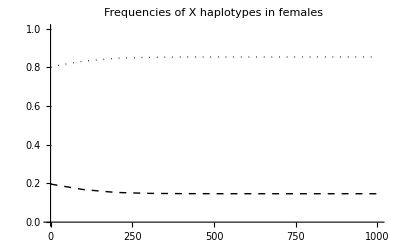

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

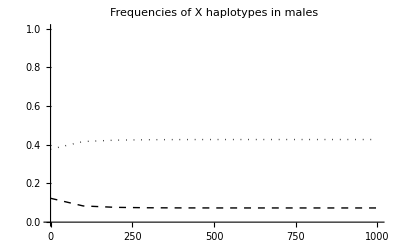

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

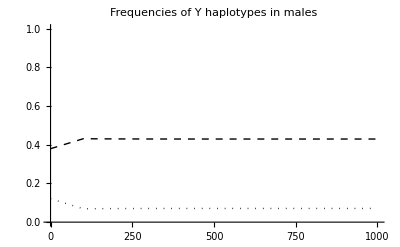

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

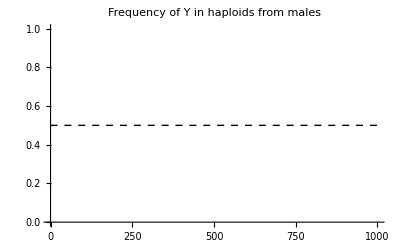

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

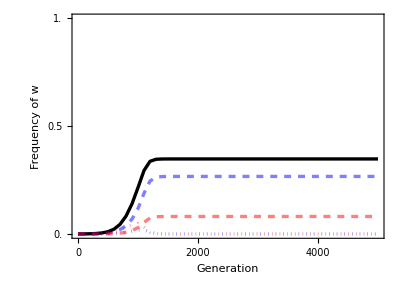

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

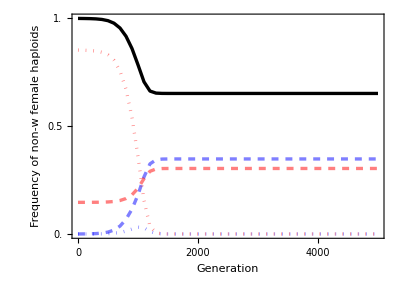

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

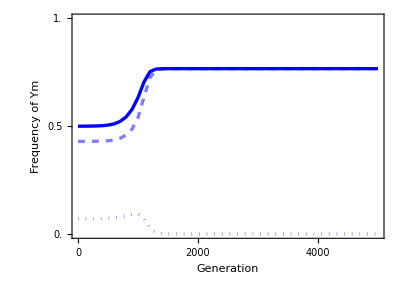

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

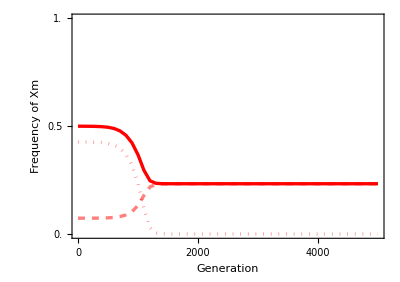

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio at birth

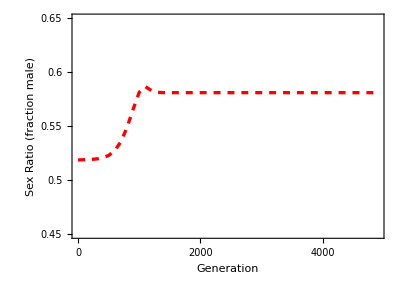

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

#### Mean diploid fitness

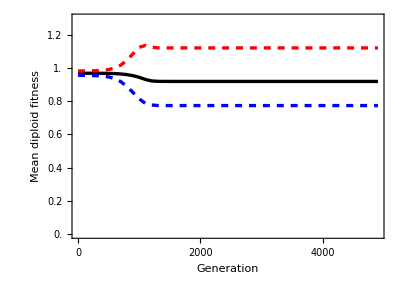

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

#### Mean haploid fitness

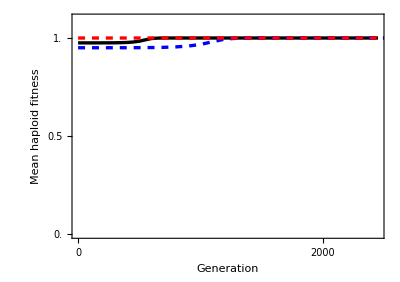

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Example: W invades XY, fixes [R=0.05]

#### Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
```

```mathematica
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.05;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

Should it invade? If the following is positive, yes

```mathematica
-(VA Subscript[sDip, female] (-2 r Subscript[sDip, female]+R Subscript[sDip, female]+2 r R Subscript[sDip, female]-R Subscript[sDip, male]+2 r R Subscript[sDip, male]) Subscript[sHap, male]^2)/(2 r R (Subscript[sDip, female]+Subscript[sDip, male])^2)/.r->tryr/.R->tryR/.Subscript[sDip, female]->trysAf/.Subscript[sDip, male]->trysAm/.Subscript[sHap, male]->tryt
```

0.0725 VA

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.687097

0.312903

0.350371

0.149629

0.0710304

0.42897

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

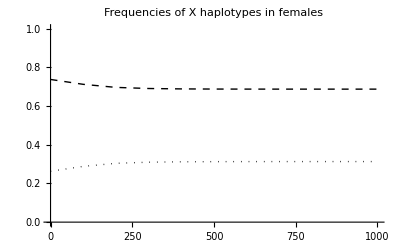

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

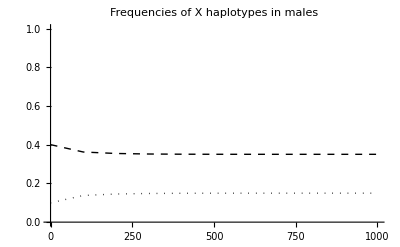

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

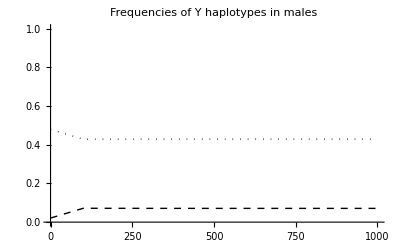

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

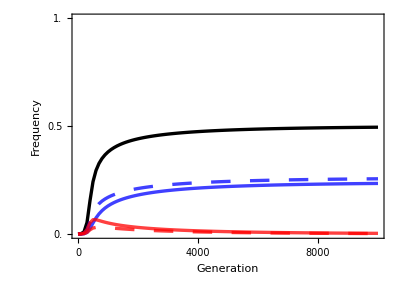

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],(*W*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with YA*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[Large]],(*W with Ya*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with XA*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[Large]]
},(*W with Xa*)
PlotRange->{0,1}]
```

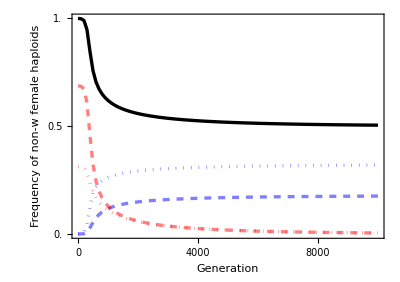

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]], (*X and Y females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],(*YA females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],(*Ya females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],(*XA females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},(*Xa females*)
PlotRange->{0,1}]
```

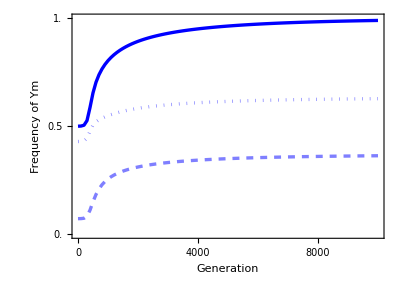

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

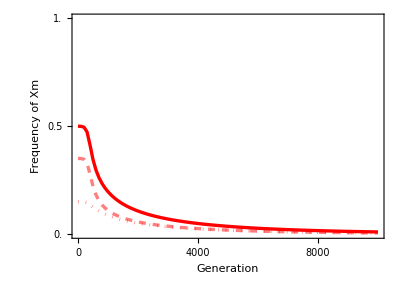

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Turnover (A)

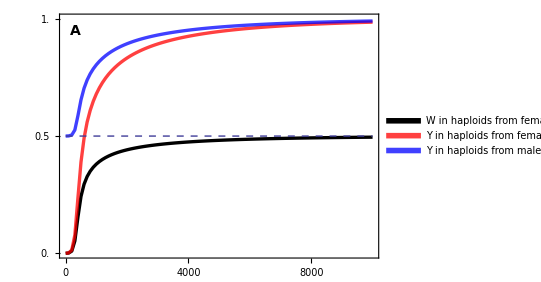

```mathematica
Legended[

Show[

(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*Y frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Frequency",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["W in haploids from females",14],
Style["Y in haploids from females",14],
Style["Y in haploids from males",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.185}
]
]

Export[plotdir<>"FreqWLowR.pdf",%];
```

#### Sex ratio at birth (B)

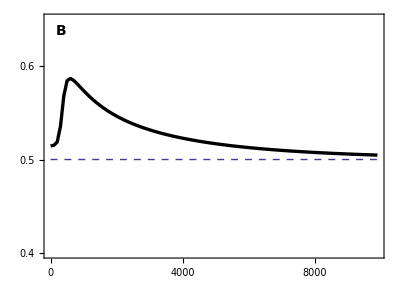

```mathematica
yplotminSexRatio=0.4;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.1;

Show[

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Sex ratio at birth (% male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[plotdir<>"SexRatioLowR.pdf",%];
```

#### Mean diploid viability fitness (C)

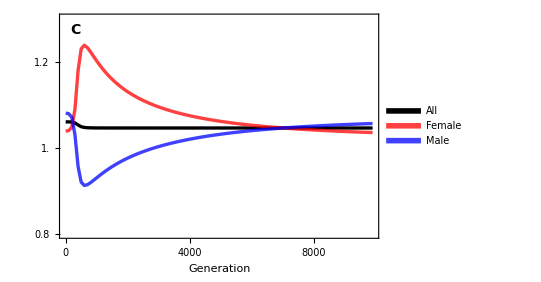

```mathematica
yplotminSexRatio=0.8;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Legended[

Show[

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid viability fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["All",14],
Style["Female",14],
Style["Male",14]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.6,0.125}
]
]

Export[plotdir<>"MeanDipFitLowR.pdf",%];
```

#### Mean haploid viability fitness

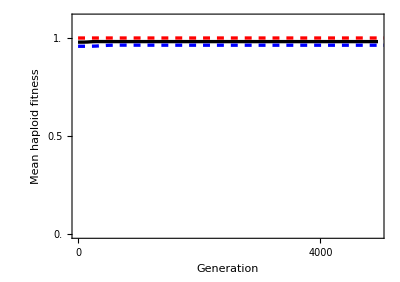

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Example: W invades XY, does not fix [R=0.5]

#### Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
```

```mathematica
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

Should it invade? If the following is positive, yes

```mathematica
-(VA Subscript[sDip, female] (-2 r Subscript[sDip, female]+R Subscript[sDip, female]+2 r R Subscript[sDip, female]-R Subscript[sDip, male]+2 r R Subscript[sDip, male]) Subscript[sHap, male]^2)/(2 r R (Subscript[sDip, female]+Subscript[sDip, male])^2)/.r->tryr/.R->tryR/.Subscript[sDip, female]->trysAf/.Subscript[sDip, male]->trysAm/.Subscript[sHap, male]->tryt
```

0.06125 VA

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.687097

0.312903

0.350371

0.149629

0.0710304

0.42897

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

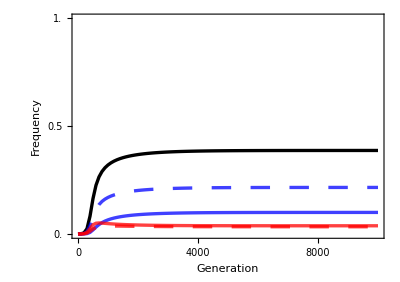

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],(*W*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with YA*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[Large]],(*W with Ya*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with XA*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[Large]]
},(*W with Xa*)
PlotRange->{0,1}]
```

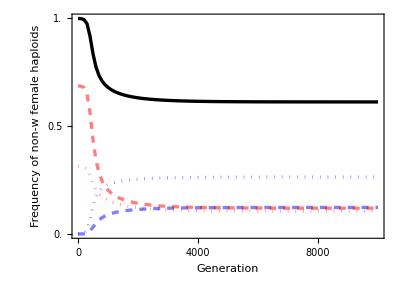

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]], (*X and Y females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],(*YA females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],(*Ya females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],(*XA females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},(*Xa females*)
PlotRange->{0,1}]
```

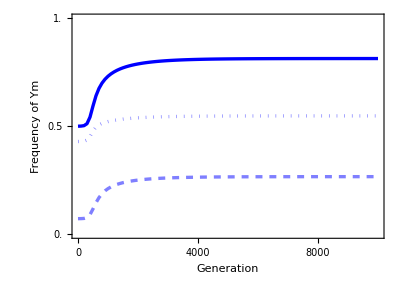

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

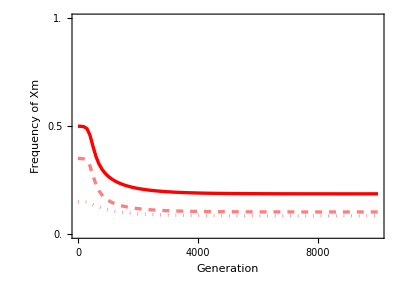

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Turnover (A)

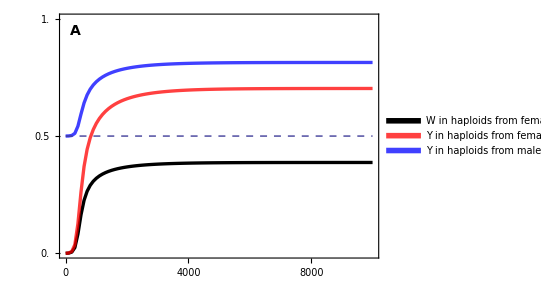

```mathematica
Legended[

Show[

(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*Y frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*Y frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Frequency",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["W in haploids from females",14],
Style["Y in haploids from females",14],
Style["Y in haploids from males",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.185}
]
]

Export[plotdir<>"FreqWHighR.pdf",%];
```

#### Sex ratio at birth (B)

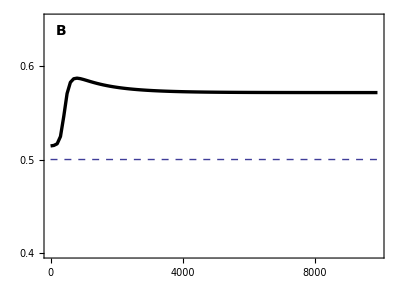

```mathematica
yplotminSexRatio=0.4;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.1;

Show[

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Sex ratio at birth (% male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[plotdir<>"SexRatioHighR.pdf",%];
```

#### Mean diploid viability fitness (C)

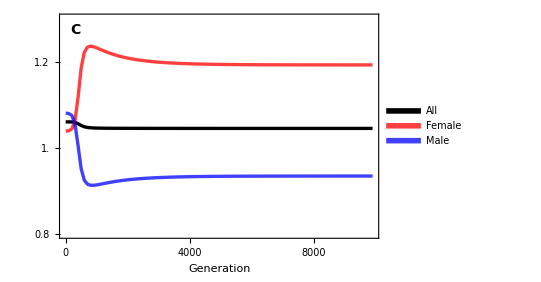

```mathematica
yplotminSexRatio=0.8;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Legended[

Show[

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid viability fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["All",14],
Style["Female",14],
Style["Male",14]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.6,0.125}
]
]

Export[plotdir<>"MeanDipFitHighR.pdf",%];
```

#### Mean haploid viability fitness

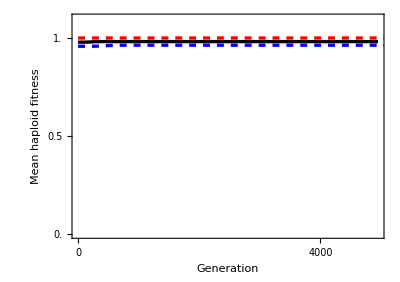

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Kozi example: W invades XY and fixes when Y fully linked with allele driving in males

#### Parameters

```mathematica
tryFAA=1;
tryFAa=1;
tryFaa=1;
tryMAA=1;
tryMAa=1;
tryMaa=1;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0;
tryMdA=0.4;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
(*tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]*)
```

```mathematica
equil[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.,1.,0.,0.5,0.,0.5},{0.,1.,0.,0.6,0.4,0.},{1.,0.,0.4,0.,0.,0.6},{1.,0.,0.5,0.,0.5,0.}}

```mathematica
initialpXAf=1;
initialpXaf=0;
initialpXAm=0.4;
initialpXam=0;
initialYAf=0;
initialYaf=0;
initialpYAm=0;
initialpYam=0.6;
```

#### Interior stability (this is unstable)

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=-0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

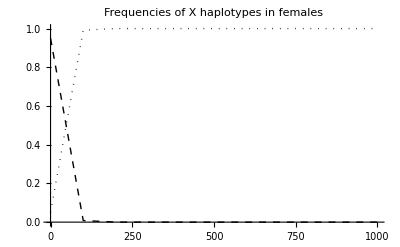

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

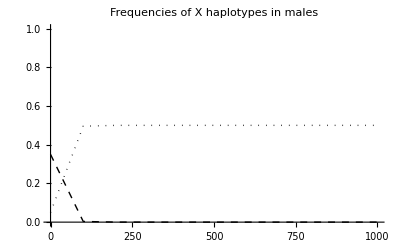

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

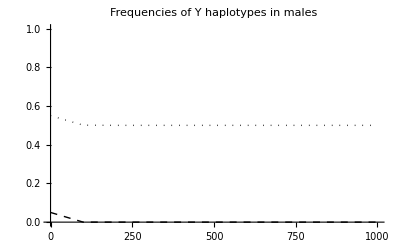

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

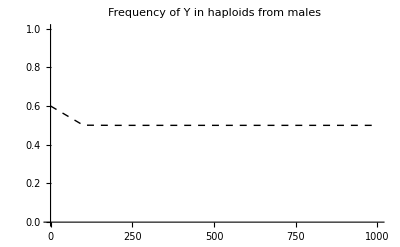

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=200;
tinterval=2;
tplotinterval=50;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

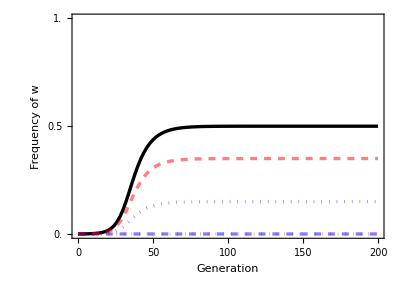

```mathematica
ListPlot[{Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

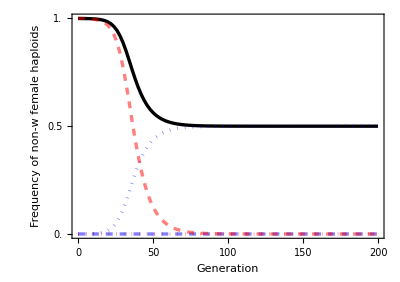

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

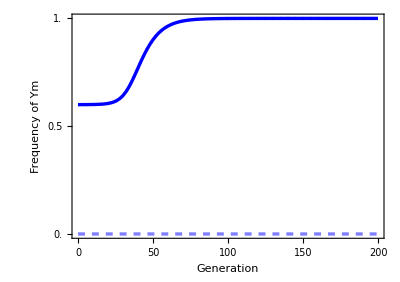

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

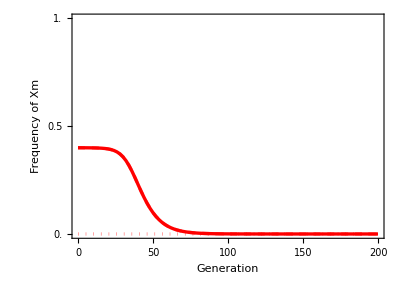

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio at birth

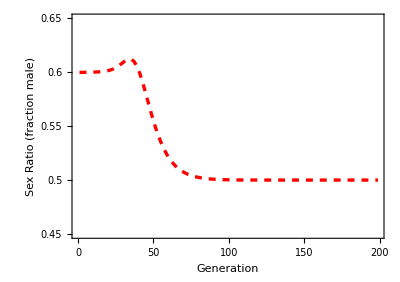

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

#### Mean diploid fitness

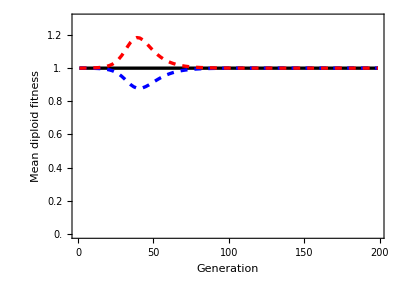

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

#### Mean haploid fitness

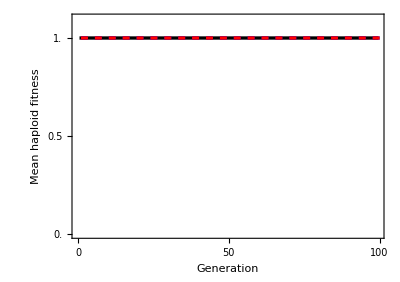

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Kozi counter-example: Y invades ZW and fixes when W fully linked with allele driving in males

Here X is Z, Y is W, males are females, and females are males.

#### Parameters

```mathematica
tryFAA=1;
tryFAa=1;
tryFaa=1;
tryMAA=1;
tryMAa=1;
tryMaa=1;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0;
tryMdA=0.5;
tryFdA=0.4;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0;
```

and tryk (1=neo-Y, 0=neo-W)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
(*tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]*)
```

A fixed on Z and a fixed on W

```mathematica
initialpXAf=1;
initialpXaf=0;
initialpXAm=0.5;
initialpXam=0;
initialYAf=0;
initialYaf=0;
initialpYAm=0;
initialpYam=0.5;
```

#### Interior stability (this is unstable)

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

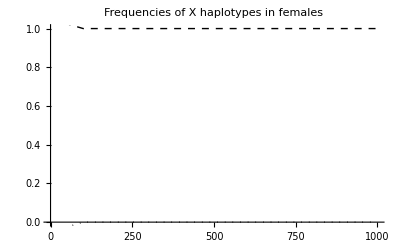

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

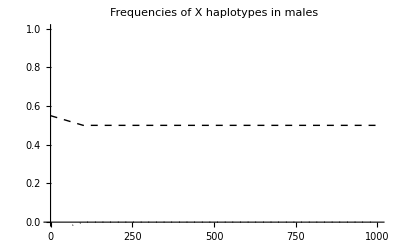

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

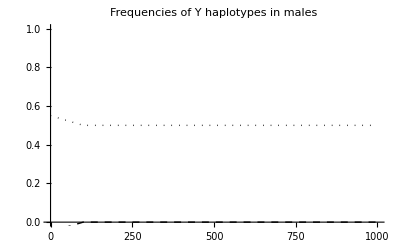

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=400;
tinterval=2;
tplotinterval=100;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

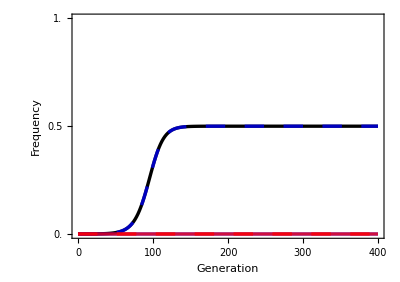

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],(*W*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with YA*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[Large]],(*W with Ya*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with XA*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[Large]]
},(*W with Xa*)
PlotRange->{0,1}]
```

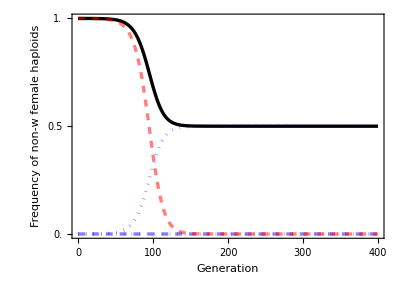

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]], (*X and Y females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],(*YA females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],(*Ya females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],(*XA females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},(*Xa females*)
PlotRange->{0,1}]
```

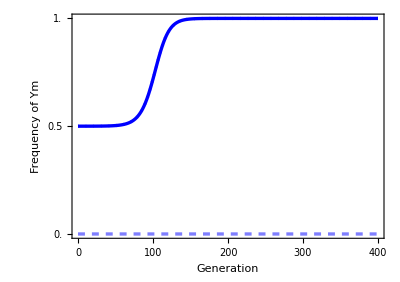

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

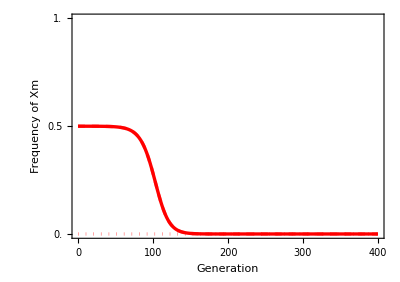

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Turnover (A)

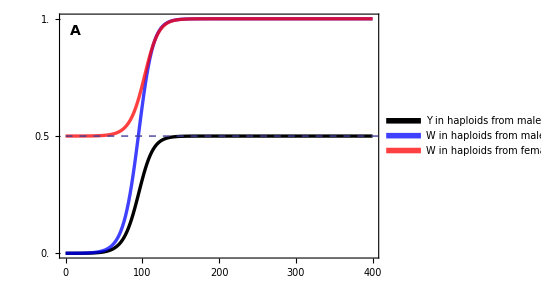

```mathematica
Legended[

Show[

(*Y frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*W frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Frequency",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]]
},
{
Style["Y in haploids from males",14],
Style["W in haploids from males",14],
Style["W in haploids from females",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.2}
]
]

Export[plotdir<>"FreqWCounterKozi.pdf",%];
```

#### Sex ratio at birth (B)

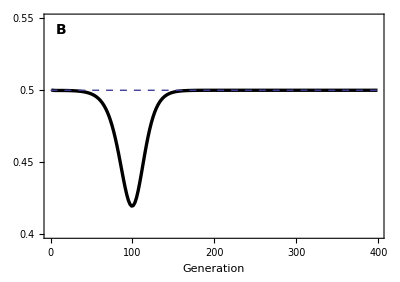

```mathematica
yplotminSexRatio=0.4;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.05;

Show[

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Sex ratio at birth (% male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[plotdir<>"SexRatioCounterKozi.pdf",%];
```

#### Mean diploid viability fitness (C)

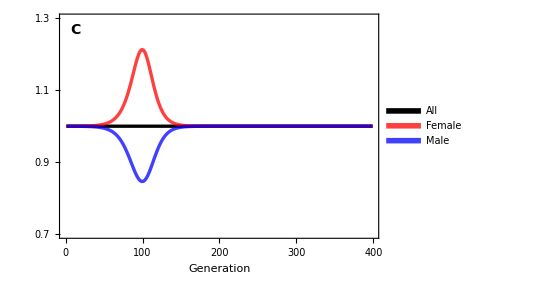

```mathematica
yplotminSexRatio=0.7;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Legended[

Show[

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid viability fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["All",14],
Style["Female",14],
Style["Male",14]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.6,0.125}
]
]

Export[plotdir<>"MeanDipFitCounterKozi.pdf",%];
```

#### Mean haploid viability fitness

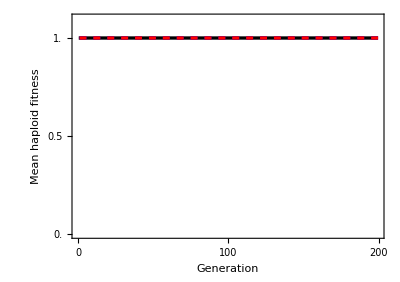

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Kozi counter-example: Y invades ZW and fixes when W fully linked with allele driving in males (R=0.5)

Here X is Z, Y is W, males are females, and females are males.

#### Parameters

```mathematica
tryFAA=1;
tryFAa=1;
tryFaa=1;
tryMAA=1;
tryMAa=1;
tryMaa=1;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0;
tryMdA=0.5;
tryFdA=0.4;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

and tryk (1=neo-Y, 0=neo-W)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
(*tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]*)
```

A fixed on Z and a fixed on W

```mathematica
initialpXAf=1;
initialpXaf=0;
initialpXAm=0.5;
initialpXam=0;
initialYAf=0;
initialYaf=0;
initialpYAm=0;
initialpYam=0.5;
```

#### Interior stability (this is unstable)

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=400;
tinterval=2;
tplotinterval=100;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

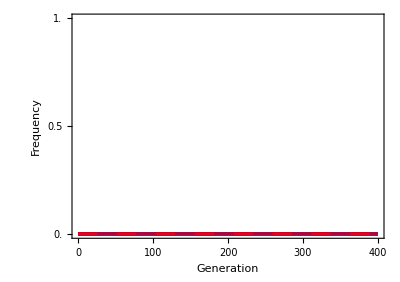

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],(*W*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with YA*)
Directive[Blue,Opacity[0.75],Thickness[lwd],Dashing[Large]],(*W with Ya*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[None]],(*W with XA*)
Directive[Red,Opacity[0.75],Thickness[lwd],Dashing[Large]]
},(*W with Xa*)
PlotRange->{0,1}]
```

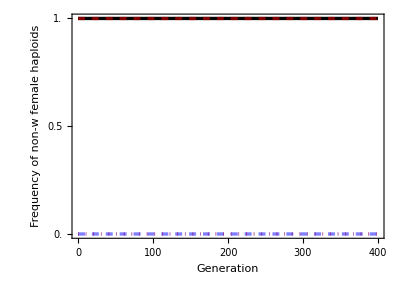

```mathematica
ListPlot[{
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]], (*X and Y females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],(*YA females*)
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],(*Ya females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],(*XA females*)
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},(*Xa females*)
PlotRange->{0,1}]
```

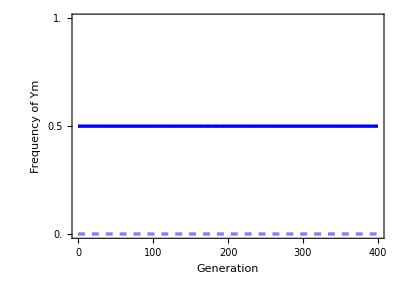

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

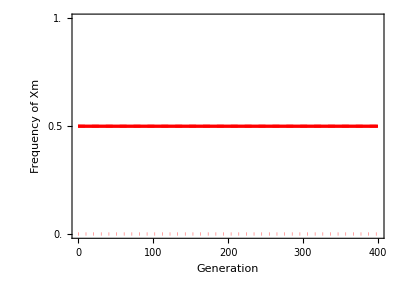

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Turnover (A)

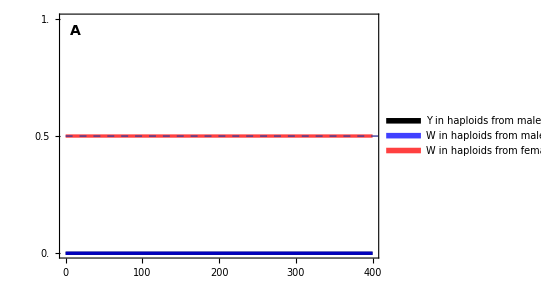

```mathematica
Legended[

Show[

(*Y frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*W frequency in haploids from males*)
ListPlot[
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

(*W frequency in haploids from females*)
ListPlot[
Table[{t,
Total[{nextYAwm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Joined->True,
PlotRange->{0,1},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Frequency",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]]
},
{
Style["Y in haploids from males",14],
Style["W in haploids from males",14],
Style["W in haploids from females",14]
},
LegendFunction->"Frame",
LegendLayout->"Column",
Spacings->{0.5,0.1}
],
{0.65,0.2}
]
]

(*Export[plotdir<>"FreqWCounterKozi.pdf",%];*)
```

#### Sex ratio at birth (B)

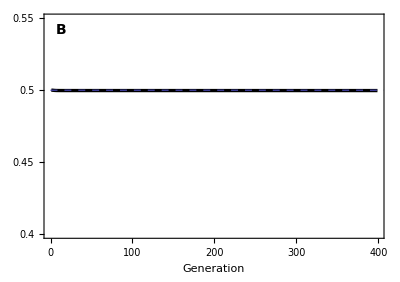

```mathematica
yplotminSexRatio=0.4;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.05;

Show[

(*sex ratio at birth*)
ListPlot[
Table[{t,
Total[{
1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

Plot[0.5,{x,0,10000},PlotStyle->{Dashed}],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style["Sex ratio at birth (% male)",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[plotdir<>"SexRatioCounterKozi.pdf",%];*)
```

#### Mean diploid viability fitness (C)

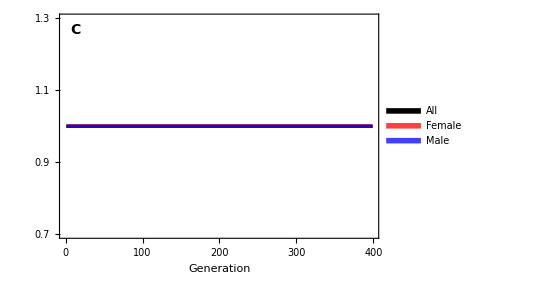

```mathematica
yplotminSexRatio=0.7;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Legended[

Show[

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Black,Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Red,Opacity[0.75],Thickness[lwd]]}
],

(*mean diploid viability fitness*)
ListPlot[
Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}],
Joined->True,
PlotRange->{yplotminSexRatio,yplotmaxSexRatio},
PlotStyle->{Directive[Blue,Opacity[0.75],Thickness[lwd]]}
],

Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Mean diploid viability fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],

Placed[
LineLegend[
{
Directive[Black,Thickness[0.2]],
Directive[Red,Opacity[0.75],Thickness[0.2]],
Directive[Blue,Opacity[0.75],Thickness[0.2]]
},
{
Style["All",14],
Style["Female",14],
Style["Male",14]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.6,0.125}
]
]

(*Export[plotdir<>"MeanDipFitCounterKozi.pdf",%];*)
```

#### Mean haploid viability fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

## Plot of neo-W invasion fitness against chromosomal position of selected locus

Here we want to explore the ability of a neo-W to invade an XY system under all linear arrangements of loci. To do so we need to give the segregation rules for each arrangement separately, and then derive resident equilibrium and invasion fitness for each model. This is done in a separate file (Arrangements.nb) and the resulting functions given below.

### Invasion fitness function for linear arrangement XAM

Resident equilibria

```mathematica
Clear[equilXAM]
equilXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXAM]
sieveXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXAM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotXAM]
invasionplotXAM[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==-Fa FA (-4 Faa FAa Ma^2+4 Faa FAa Ma^2 pXm-2 FAa^2 Ma MA pXm-2 Faa FAA Ma MA pXm-Faa FAa Ma^2 pXm^2+FAa^2 Ma MA pXm^2+Faa FAA Ma MA pXm^2-FAa FAA MA^2 pXm^2+4 Faa FAa Ma^2 pYm-2 FAa^2 Ma MA pYm-2 Faa FAA Ma MA pYm-2 Faa FAa Ma^2 pXm pYm+2 FAa^2 Ma MA pXm pYm+2 Faa FAA Ma MA pXm pYm-2 FAa FAA MA^2 pXm pYm-Faa FAa Ma^2 pYm^2+FAa^2 Ma MA pYm^2+Faa FAA Ma MA pYm^2-FAa FAA MA^2 pYm^2+4 Faa FAa Ma^2 R-4 Faa FAa Ma^2 pXm R+4 FAa^2 Ma MA pXm R+Faa FAa Ma^2 pXm^2 R-2 FAa^2 Ma MA pXm^2 R+FAa FAA MA^2 pXm^2 R-4 Faa FAa Ma^2 pYm R+4 FAa^2 Ma MA pYm R+2 Faa FAa Ma^2 pXm pYm R-4 FAa^2 Ma MA pXm pYm R+2 FAa FAA MA^2 pXm pYm R+Faa FAa Ma^2 pYm^2 R-2 FAa^2 Ma MA pYm^2 R+FAa FAA MA^2 pYm^2 R)+2 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm) (-2 Fa Faa Ma-2 FA FAa Ma+Fa Faa Ma pXm+FA FAa Ma pXm-Fa FAa MA pXm-FA FAA MA pXm+Fa Faa Ma pYm+FA FAa Ma pYm-Fa FAa MA pYm-FA FAA MA pYm+2 FA FAa Ma R-FA FAa Ma pXm R+Fa FAa MA pXm R-FA FAa Ma pYm R+Fa FAa MA pYm R) λ+4 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)^2 λ^2/.subs,λ]]-1
]
```

Or, when including drive:

```mathematica
Clear[invasionplotXAM]
invasionplotXAM[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
r=tryr
},
Max[λ/.NSolve[0==((λ^2 (2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) (-1+r) R (2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 R^2 λ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) (-pXm+freqYm pXm-freqYm pYm r) R^2 λ^2)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma (-freqYm+freqYm pYm-r+freqYm r+pXm r-freqYm pXm r) R (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 R^2 λ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) (-pXm+freqYm pXm-freqYm pYm r) R^2 λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))+(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pYm r+2 FAa MA pYm r-2 FAa FdA MA pYm r+Faa Ma R-Faa Ma pYm R-2 Faa Ma r R+2 Faa Ma pYm r R-2 FAa MA pYm r R+2 FAa FdA MA pYm r R) (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) ((Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+Faa Ma r-Faa freqYm Ma r-Faa Ma pXm r+Faa freqYm Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r-2 FAa freqYm MA pXm r+2 FAa FdA freqYm MA pXm r+Faa Ma R-Faa freqYm Ma R-Faa Ma pXm R+Faa freqYm Ma pXm R+2 FAa MA pXm R-2 FAa FdA MA pXm R-2 FAa freqYm MA pXm R+2 FAa FdA freqYm MA pXm R+2 FAa freqYm MA pYm R-2 FAa FdA freqYm MA pYm R-2 Faa Ma r R+2 Faa freqYm Ma r R+2 Faa Ma pXm r R-2 Faa freqYm Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R+2 FAa freqYm MA pXm r R-2 FAa FdA freqYm MA pXm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2)/.subs),λ]]-1]
```

### invasion function function for linear arrangement XMA

Resident equilibria

```mathematica
Clear[equilXMA]
equilXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)-MA MAa pYm ((-1+freqYm) pXm+MdA (R+χ-2 R χ)))+FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm-2 Ma MAa (-1+pYm) ((-1+freqYm) pXm+MdA (1-χ+R (-1+2 χ)))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)+2 Ma MAa MdA (-1+pYm) (-R-χ+2 R χ))-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)+MA MAa MdA (1-χ+R (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ)))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXMA]
sieveXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXMA[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotXMA]
invasionplotXMA[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-4 FAa^2 Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+2 FAa^2 Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-4 FAa^2 Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+4 FAa^2 Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+2 FAa^2 Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R+2 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm) (-2 Faa Ma-2 FAa Ma+Faa Ma pXm+FAa Ma pXm-FAa MA pXm-FAA MA pXm+Faa Ma pYm+FAa Ma pYm-FAa MA pYm-FAA MA pYm+2 FAa Ma R-FAa Ma pXm R+FAa MA pXm R-FAa Ma pYm R+FAa MA pYm R) λ+4 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm)^2 λ^2/.subs,λ]]-1
]
```

Or, with drive:

```mathematica
Clear[invasionplotXMA]
invasionplotXMA[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==(λ^2 (-2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) R χ (-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ))-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ)+16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma R (-1+pXm-freqYm pXm+freqYm pYm+χ-freqYm χ-pXm χ+freqYm pXm χ) (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ)+16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))-(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pYm-2 FAa MA pYm+2 FAa FdA MA pYm+2 FAa MA pYm R-2 FAa FdA MA pYm R) χ (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ)+16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ+(Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+2 FAa MA pXm R-2 FAa FdA MA pXm R-2 FAa freqYm MA pXm R+2 FAa FdA freqYm MA pXm R+2 FAa freqYm MA pYm R-2 FAa FdA freqYm MA pYm R+Faa Ma χ-Faa freqYm Ma χ-Faa Ma pXm χ+Faa freqYm Ma pXm χ+2 FAa MA pXm χ-2 FAa FdA MA pXm χ-2 FAa freqYm MA pXm χ+2 FAa FdA freqYm MA pXm χ-2 FAa MA pXm R χ+2 FAa FdA MA pXm R χ+2 FAa freqYm MA pXm R χ-2 FAa FdA freqYm MA pXm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ)+16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2)/.subs,λ]]-1]
```

### Invasion fitness function for linear arrangement AXM

Resident equilibria

```mathematica
Clear[equilAXM]
equilAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveAXM]
sieveAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilAXM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotAXM]
invasionplotAXM[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
r=tryr,
χ=tryχ
},
Max[λ/.NSolve[0==((λ^2 (2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) (-1+r) χ (2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma (-r+pXm r-freqYm pXm r+freqYm pYm r-freqYm χ+freqYm pYm χ+r χ+freqYm r χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))-(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pYm-2 FAa MA pYm r+2 FAa FdA MA pYm r) χ (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ+(Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+2 FAa MA pXm r-2 FAa FdA MA pXm r-2 FAa freqYm MA pXm r+2 FAa FdA freqYm MA pXm r+2 FAa freqYm MA pYm r-2 FAa FdA freqYm MA pYm r+Faa Ma χ-Faa freqYm Ma χ-Faa Ma pXm χ+Faa freqYm Ma pXm χ+2 FAa MA pXm χ-2 FAa FdA MA pXm χ-2 FAa freqYm MA pXm χ+2 FAa FdA freqYm MA pXm χ+2 FAa freqYm MA pYm χ-2 FAa FdA freqYm MA pYm χ-2 FAa MA pXm r χ+2 FAa FdA MA pXm r χ+2 FAa freqYm MA pXm r χ-2 FAa FdA freqYm MA pXm r χ-4 FAa freqYm MA pYm r χ+4 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2))/.subs,λ]]-1
]
```

### Mapping functions (Haldane 1919, eq 3)

Mapping functions

```mathematica
setr[x_,a_]:=(1-Exp[-2 √((x-a)^2)])/2
setR[a_,m_]:=(1-Exp[-2 √((a-m)^2)])/2
setχ[x_,m_]:=(1-Exp[-2 √((x-m)^2)])/2
```

### Parameters ( hap competition with sex differences in selection but not sex ant - neo-w always invades )

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

### Plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

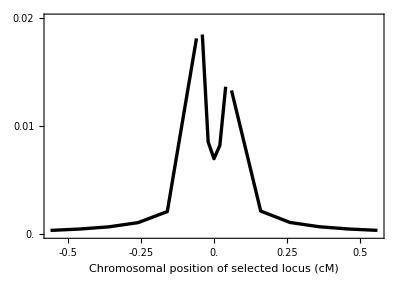

```mathematica
x=-0.05;
m=0.05;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=0;
yplotmax=0.02;
yplotinterval=0.01;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.56,-0.06,0.1}],Joined->True,PlotRange->{0,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.04,0.04,0.02}],Joined->True,PlotRange->{0,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,0.06,0.56,0.1}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

PlotRange->{{-0.56,0.56},{0,0.02}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];*)
```

### Plot (new positions)

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

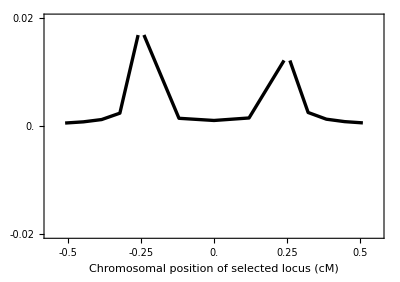

```mathematica
x=-0.25;
m=0.25;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=-0.02;
yplotmax=0.05;
yplotinterval=0.01;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,xplotmin-0.01,x-0.01,((x-0.01)-(xplotmin-0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,x+0.01,m-0.01,((m-0.01)-(x+0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,m+0.01,xplotmax+0.01,((xplotmax+0.01)-(m+0.01))/4}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],Axes->False,

PlotRange->{{-0.56,0.56},{yplotmin,0.02}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];*)
```

### Parameters 2 ( hap competition with sex differences in selection but not sex ant - but in other direction so neo-w only invades if more closely linked to A )

```mathematica
trysAf=0.15;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.05;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

### Plot 2

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

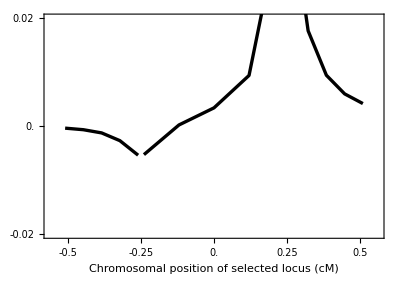

```mathematica
x=-0.25;
m=0.25;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=-0.02;
yplotmax=0.05;
yplotinterval=0.01;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,xplotmin-0.01,x-0.01,((x-0.01)-(xplotmin-0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,x+0.01,m-0.01,((m-0.01)-(x+0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,m+0.01,xplotmax+0.01,((xplotmax+0.01)-(m+0.01))/4}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],Axes->False,

PlotRange->{{-0.56,0.56},{yplotmin,0.02}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];*)
```

### Parameters 3 ( drive with no sex differences in selection and no sex ant - always invades )

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.45;
tryFdA=0.5;
```

### Plot 3

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

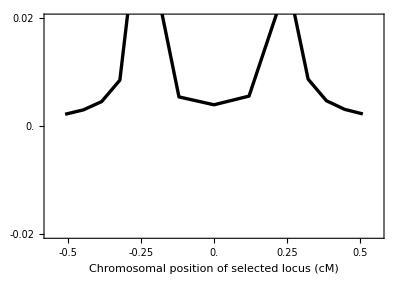

```mathematica
x=-0.25;
m=0.25;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=-0.02;
yplotmax=0.05;
yplotinterval=0.01;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,xplotmin-0.01,x-0.01,((x-0.01)-(xplotmin-0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,x+0.01,m-0.01,((m-0.01)-(x+0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,m+0.01,xplotmax+0.01,((xplotmax+0.01)-(m+0.01))/4}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],Axes->False,

PlotRange->{{-0.56,0.56},{yplotmin,0.02}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];*)
```

### Parameters 4 ( no haploid selection, sex antagonism - neo-w only invades if more closely linked to A: equivalent to van Doorn and Kirkpatrick )

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.3;
trysAm=-0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

### Plot 4

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

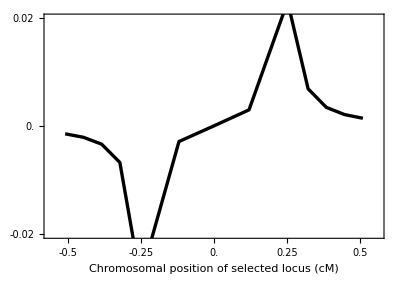

```mathematica
x=-0.25;
m=0.25;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=-0.02;
yplotmax=0.05;
yplotinterval=0.01;
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,xplotmin-0.01,x-0.01,((x-0.01)-(xplotmin-0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,x+0.01,m-0.01,((m-0.01)-(x+0.01))/4}],Joined->True,PlotRange->{yplotmin,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,m+0.01,xplotmax+0.01,((xplotmax+0.01)-(m+0.01))/4}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],Axes->False,

PlotRange->{{-0.56,0.56},{yplotmin,0.02}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];*)
```

# B. Maternal control (no drive) [plots unfinished]

## Life-cycle

### Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{zzPar,{MM,Mm,mm}}];
Subscript[fHapSel, x_,y_,z_,sex_,zzPar_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar]/Subscript[wbarHap, sex]
```

### Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_,zzM_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM]=ParallelSum[Subscript[fHapSel, xM,yM,zM,female,zzM] Subscript[fHapSel, xP,yP,zP,male,zzP],{zzP,{MM,Mm,mm}}]
```

### Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=ParallelSum[Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM] Subscript[psex, xP,zzM,sex],{zzM,{MM,Mm,mm}}]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, xP_,zzM_,male]->1-Subscript[psex, xP,zzM,female];
```

### Ancestal system

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, Y,MM,female]->0,(*always male if mother wildtype at ESD and get Y from father*)
Subscript[psex, X,MM,female]->1,(*always female if mother wildtype at ESD and get X from father*)
Subscript[fHap, Y,y_,z_,female,MM]->0,(*no Y chromosome in eggs if mother was homozygous wildtype at ESD*)
Subscript[psex, xP_,Mm,female]->k,
Subscript[psex, xP_,mm,female]->k(*female with probability k if mother had mutation at the ESD*)
};
```

### Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

### Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_,zzPar_]:=Subscript[fHapNext, x,y,z,sex,zzPar]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z,zzPar],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

### Segregation rules

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,M,x1_,y1_,M,sex_,x1_,y1_,M,MM]->1,
Subscript[pseg, x1_,y1_,m,x1_,y1_,m,sex_,x1_,y1_,m,mm]->1,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x2_,y1_,M,sex_,x2_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y1_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,M,x1_,y2_,M,sex_,x1_,y2_,M,MM]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x2_,y1_,m,sex_,x2_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y1_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,m,x1_,y2_,m,sex_,x1_,y2_,M,mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y1_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y2_,M,MM]->(1-r)/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x2_,y1_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,M,x2_,y2_,M,sex_,x1_,y2_,M,MM]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y1_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y2_,m,mm]->(1-r)/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x2_,y1_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,m,x2_,y2_,m,sex_,x1_,y2_,m,mm]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,Mm]->0,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,Mm]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,Mm]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,Mm]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,Mm]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,Mm]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,Mm]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,Mm]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,Mm]->(1-r)R/2
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,zzM_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex,zzM]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}},{zzM,{MM,Mm,mm}}]//Factor*)
```

## Resident equilibrium (weak selection)

We begin with no mutations at the modifer locus in haploids or mothers

```mathematica
subequil={
Subscript[fHap, X,A,M,female,MM]->pXf,
Subscript[fHap, X,a,M,female,MM]->1-pXf,
Subscript[fHap, X,A,M,male,MM]->(1-α) pXm,
Subscript[fHap, X,a,M,male,MM]->(1-α)(1-pXm),
Subscript[fHap, Y,A,M,male,MM]->α pYm,
Subscript[fHap, Y,a,M,male,MM]->α(1-pYm),
Subscript[fHap, x_,y_,m,sex_,zzM_]->0,
Subscript[fHap, x_,y_,z_,sex_,Mm]->0,
Subscript[fHap, x_,y_,z_,sex_,mm]->0
}/.α->1/2;
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female,MM]-Subscript[fHap, X,A,M,female,MM],
Subscript[fHapNext, X,A,M,male,MM]-Subscript[fHap, X,A,M,male,MM],
Subscript[fHapNext, Y,A,M,male,MM]-Subscript[fHap, Y,A,M,male,MM]
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
Subscript[wHap, A,sex_]->1,
Subscript[wHap, a,sex_]->1+Subscript[sHap, sex] ϵ,
Subscript[wDip, A,A,sex_]->1,
Subscript[wDip, A,a,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,A,sex_]->1+Subscript[h, sex] Subscript[sDip, sex] ϵ,
Subscript[wDip, a,a,sex_]->1+ Subscript[sDip, sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]//Flatten
```

{pYm0→pXf0,pXm0→pXf0}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip_female+4 pA^2 sDip_female-2 pA^3 sDip_female+2 pA h_female sDip_female-6 pA^2 h_female sDip_female+4 pA^3 h_female sDip_female-pA sHap_female+pA^2 sHap_female-pA sHap_male+pA^2 sHap_male),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA sHap_female+pA^2 sHap_female+pA r sHap_female-pA^2 r sHap_female-pA r sHap_male+pA^2 r sHap_male),1/2 ϵ (pXf1 r-pYm1 r-pA sDip_male+2 pA^2 sDip_male-pA^3 sDip_male+pA h_male sDip_male-3 pA^2 h_male sDip_male+2 pA^3 h_male sDip_male-pA r sHap_female+pA^2 r sHap_female-pA sHap_male+pA^2 sHap_male+pA r sHap_male-pA^2 r sHap_male)}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (2 h_female sDip_female sDip_male-2 h_male sDip_female sDip_male-sDip_female sHap_female+2 h_female sDip_female sHap_female+sDip_male sHap_female-2 h_male sDip_male sHap_female-sDip_female sHap_male+2 h_female sDip_female sHap_male+sDip_male sHap_male-2 h_male sDip_male sHap_male))/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3,dpAYmXf→-((-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male) (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male) (h_female sDip_female sDip_male-h_male sDip_female sDip_male-r sDip_female sHap_female+2 r h_female sDip_female sHap_female+sDip_male sHap_female-r sDip_male sHap_female-2 h_male sDip_male sHap_female+2 r h_male sDip_male sHap_female-sDip_female sHap_male+r sDip_female sHap_male+2 h_female sDip_female sHap_male-2 r h_female sDip_female sHap_male+r sDip_male sHap_male-2 r h_male sDip_male sHap_male))/(r (-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)^3),pA→(-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)/(-sDip_female+2 h_female sDip_female-sDip_male+2 h_male sDip_male)}}

## Resident stability (weak selection) [do not need to re-run if unchanged]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[Subscript[fHapNext, X,y,M,female,MM],{y,{A,a}}],Table[Subscript[fHapNext, x,y,M,male,MM],{x,{X,Y}},{y,{A,a}}]//Flatten]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,Subscript[fHap, X,A,M,female,MM]],
D[eqs,Subscript[fHap, X,a,M,female,MM]],
D[eqs,Subscript[fHap, X,A,M,male,MM]],
D[eqs,Subscript[fHap, X,a,M,male,MM]],
D[eqs,Subscript[fHap, Y,A,M,male,MM]],
D[eqs,Subscript[fHap, Y,a,M,male,MM]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h_female sDip_female+h_male sDip_male+sHap_female+sHap_male)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip_female+h_female sDip_female-sDip_male+h_male sDip_male-sHap_female-sHap_male)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## Sex chromosome turnover (weak selection)

### Characteristic polynomial and eigenvalues

Here we are interested in the ability of a rare mutant at the ESD locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is (this takes a minute or two, or ten)

```mathematica
(*eqsmut=Table[Subscript[fHapNext, x,y,m,sex,Mm],{sex,{female,male}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;*)
```

```mathematica
(*matExtFull=Transpose[{
D[eqsmut,Subscript[fHap, X,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,female,Mm]],
D[eqsmut,Subscript[fHap, X,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,A,m,male,Mm]],
D[eqsmut,Subscript[fHap, X,a,m,male,Mm]],
D[eqsmut,Subscript[fHap, Y,a,m,male,Mm]]
}]/.subequil//Factor;*)
```

And the characteristic polynomial

```mathematica
(*charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];*)
```

Solving for the eigenvalues with no selection gives

```mathematica
(*charploy0=Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
charploy0sol=Solve[%==0,λ]//Flatten//Simplify;*)
```

Lets plot these

```mathematica
(*Table[Show[Table[Plot[λ/.charploy0sol[[i]],{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All],{r,{0,0.5}},{R,{0,0.5}}]*)
```

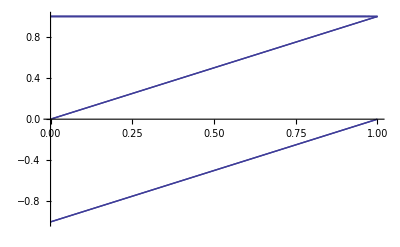
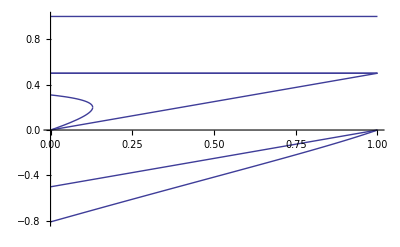
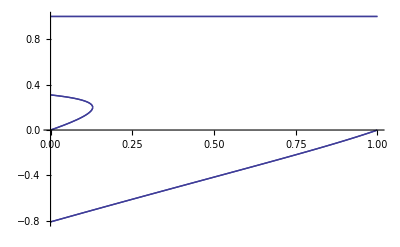
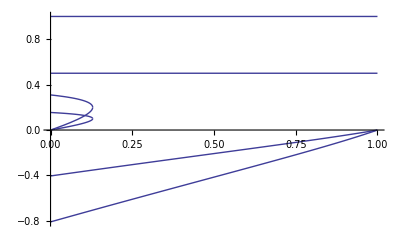
```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}};
```

And so it looks like on this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is zero

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]*)
```

And on the 2nd order (this takes a few minutes)

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify];*)
```

Then we can put in all the differences

```mathematica
(*tester=Collect[lambda2diffs/.realsol[[3]],{dpAXmXf,dpAYmXf},Simplify];*)
```

```mathematica
(*pasted for speed*)
tester={(((-1+Subscript[h, female]) Subscript[sDip, female]+(-1+Subscript[h, male]) Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]) (-(-(Subscript[sDip, female]-Subscript[sDip, male]) (Subscript[sHap, female]+Subscript[sHap, male])-2 Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male])+2 Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male])) ((-2 (1+k (-1+R))^2 R (1+(-1+k) R)+2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-k r^2 (-1+R) (-4+11 R-8 R^2+2 k^2 R (2-6 R+5 R^2)+k (4-21 R+30 R^2-10 R^3))+r (-2 (-1+R)^2+2 k^3 (1-2 R)^2 (-1+R) R+k (4-18 R+25 R^2-11 R^3)+k^2 (-2+16 R-39 R^2+35 R^3-8 R^4))) (Subscript[sHap, female]-Subscript[sHap, male])-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((-1+k) (-2 (1+k (-1+R))^2 R (3-2 R+k (-1+2 R))+2 k^2 r^3 (-1+R)^2 (-1+2 R) (3-2 R+k (-1+2 R))+r (-8+14 R-6 R^2+2 k^3 (-1+R) (-1+2 R)^3+k (17-59 R+65 R^2-22 R^3)+k^2 (-11+58 R-107 R^2+78 R^3-16 R^4))+k r^2 (-14+45 R-46 R^2+16 R^3+k^2 (-4+24 R-54 R^2+54 R^3-20 R^4)+k (17-79 R+132 R^2-90 R^3+20 R^4))) Subscript[sDip, female] (-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]+Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]))-1/r(-r Subscript[sDip, female] Subscript[sHap, female]+Subscript[sDip, male] Subscript[sHap, female]-r Subscript[sDip, male] Subscript[sHap, female]-Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, female] Subscript[sHap, male]+r Subscript[sDip, male] Subscript[sHap, male]-Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+2 Subscript[sHap, female]-2 r Subscript[sHap, female]+2 r Subscript[sHap, male])+Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+2 (r Subscript[sHap, female]+Subscript[sHap, male]-r Subscript[sHap, male]))) (-2 r Subscript[sHap, female]+4 k r Subscript[sHap, female]-2 k^2 r Subscript[sHap, female]-4 k r^2 Subscript[sHap, female]+4 k^2 r^2 Subscript[sHap, female]-2 k^2 r^3 Subscript[sHap, female]+2 r R Subscript[sHap, female]-12 k r R Subscript[sHap, female]+12 k^2 r R Subscript[sHap, female]-2 k^3 r R Subscript[sHap, female]+13 k r^2 R Subscript[sHap, female]-23 k^2 r^2 R Subscript[sHap, female]+4 k^3 r^2 R Subscript[sHap, female]+10 k^2 r^3 R Subscript[sHap, female]-2 k^3 r^3 R Subscript[sHap, female]-4 k R^2 Subscript[sHap, female]+6 k^2 R^2 Subscript[sHap, female]-2 k^3 R^2 Subscript[sHap, female]+13 k r R^2 Subscript[sHap, female]-29 k^2 r R^2 Subscript[sHap, female]+10 k^3 r R^2 Subscript[sHap, female]-13 k r^2 R^2 Subscript[sHap, female]+45 k^2 r^2 R^2 Subscript[sHap, female]-16 k^3 r^2 R^2 Subscript[sHap, female]-18 k^2 r^3 R^2 Subscript[sHap, female]+8 k^3 r^3 R^2 Subscript[sHap, female]+2 k R^3 Subscript[sHap, female]-8 k^2 R^3 Subscript[sHap, female]+4 k^3 R^3 Subscript[sHap, female]-5 k r R^3 Subscript[sHap, female]+29 k^2 r R^3 Subscript[sHap, female]-16 k^3 r R^3 Subscript[sHap, female]+4 k r^2 R^3 Subscript[sHap, female]-36 k^2 r^2 R^3 Subscript[sHap, female]+22 k^3 r^2 R^3 Subscript[sHap, female]+14 k^2 r^3 R^3 Subscript[sHap, female]-10 k^3 r^3 R^3 Subscript[sHap, female]+2 k^2 R^4 Subscript[sHap, female]-2 k^3 R^4 Subscript[sHap, female]-8 k^2 r R^4 Subscript[sHap, female]+8 k^3 r R^4 Subscript[sHap, female]+10 k^2 r^2 R^4 Subscript[sHap, female]-10 k^3 r^2 R^4 Subscript[sHap, female]-4 k^2 r^3 R^4 Subscript[sHap, female]+4 k^3 r^3 R^4 Subscript[sHap, female]+7 r Subscript[sHap, male]-26 k r Subscript[sHap, male]+35 k^2 r Subscript[sHap, male]-20 k^3 r Subscript[sHap, male]+4 k^4 r Subscript[sHap, male]+8 k r^2 Subscript[sHap, male]-28 k^2 r^2 Subscript[sHap, male]+28 k^3 r^2 Subscript[sHap, male]-8 k^4 r^2 Subscript[sHap, male]+2 k^2 r^3 Subscript[sHap, male]-8 k^3 r^3 Subscript[sHap, male]+4 k^4 r^3 Subscript[sHap, male]+4 R Subscript[sHap, male]-18 k R Subscript[sHap, male]+28 k^2 R Subscript[sHap, male]-18 k^3 R Subscript[sHap, male]+4 k^4 R Subscript[sHap, male]-10 r R Subscript[sHap, male]+56 k r R Subscript[sHap, male]-114 k^2 r R Subscript[sHap, male]+92 k^3 r R Subscript[sHap, male]-24 k^4 r R Subscript[sHap, male]-23 k r^2 R Subscript[sHap, male]+95 k^2 r^2 R Subscript[sHap, male]-118 k^3 r^2 R Subscript[sHap, male]+40 k^4 r^2 R Subscript[sHap, male]-10 k^2 r^3 R Subscript[sHap, male]+38 k^3 r^3 R Subscript[sHap, male]-20 k^4 r^3 R Subscript[sHap, male]-2 R^2 Subscript[sHap, male]+18 k R^2 Subscript[sHap, male]-46 k^2 R^2 Subscript[sHap, male]+42 k^3 R^2 Subscript[sHap, male]-12 k^4 R^2 Subscript[sHap, male]+3 r R^2 Subscript[sHap, male]-39 k r R^2 Subscript[sHap, male]+132 k^2 r R^2 Subscript[sHap, male]-154 k^3 r R^2 Subscript[sHap, male]+52 k^4 r R^2 Subscript[sHap, male]+21 k r^2 R^2 Subscript[sHap, male]-113 k^2 r^2 R^2 Subscript[sHap, male]+184 k^3 r^2 R^2 Subscript[sHap, male]-76 k^4 r^2 R^2 Subscript[sHap, male]+18 k^2 r^3 R^2 Subscript[sHap, male]-64 k^3 r^3 R^2 Subscript[sHap, male]+36 k^4 r^3 R^2 Subscript[sHap, male]-4 k R^3 Subscript[sHap, male]+20 k^2 R^3 Subscript[sHap, male]-30 k^3 R^3 Subscript[sHap, male]+12 k^4 R^3 Subscript[sHap, male]+9 k r R^3 Subscript[sHap, male]-59 k^2 r R^3 Subscript[sHap, male]+106 k^3 r R^3 Subscript[sHap, male]-48 k^4 r R^3 Subscript[sHap, male]-6 k r^2 R^3 Subscript[sHap, male]+56 k^2 r^2 R^3 Subscript[sHap, male]-124 k^3 r^2 R^3 Subscript[sHap, male]+64 k^4 r^2 R^3 Subscript[sHap, male]-14 k^2 r^3 R^3 Subscript[sHap, male]+46 k^3 r^3 R^3 Subscript[sHap, male]-28 k^4 r^3 R^3 Subscript[sHap, male]-2 k^2 R^4 Subscript[sHap, male]+6 k^3 R^4 Subscript[sHap, male]-4 k^4 R^4 Subscript[sHap, male]+8 k^2 r R^4 Subscript[sHap, male]-24 k^3 r R^4 Subscript[sHap, male]+16 k^4 r R^4 Subscript[sHap, male]-10 k^2 r^2 R^4 Subscript[sHap, male]+30 k^3 r^2 R^4 Subscript[sHap, male]-20 k^4 r^2 R^4 Subscript[sHap, male]+4 k^2 r^3 R^4 Subscript[sHap, male]-12 k^3 r^3 R^4 Subscript[sHap, male]+8 k^4 r^3 R^4 Subscript[sHap, male]-((-1+k) (2 (-1+k) k^2 r^3 (-1+R)^2 (-1+2 R)-2 (-1+k) R (2+k^2 (-1+R)^2-R-k (3-4 R+R^2))+r (7+2 k^3 (1-2 R)^2 (-1+R)-8 R+3 R^2+k^2 (9-32 R+37 R^2-12 R^3)+k (-14+31 R-22 R^2+4 R^3))+k r^2 (8-19 R+12 R^2-2 R^3-2 k^2 (-2+8 R-11 R^2+5 R^3)+k (-11+35 R-36 R^2+12 R^3))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((2 k^2 r^3 (-1+R)^2 (-1+2 R) (1-2 k (-1+R)+k^2 (-1+2 R))+2 k R (-2+R-k^3 (-1+R)^2 (-1+2 R)+k (5-9 R+3 R^2)+2 k^2 (-2+6 R-5 R^2+R^3))+r (-2+2 k^4 (-1+R) (-1+2 R)^3-k (1-5 R+R^2)+k^2 (10-39 R+44 R^2-14 R^3)+k^3 (-9+48 R-91 R^2+70 R^3-16 R^4))+k r^2 (-4+9 R-4 R^2+k (-5+18 R-20 R^2+6 R^3)+k^3 (-4+24 R-54 R^2+54 R^3-20 R^4)+k^2 (13-63 R+110 R^2-80 R^3+20 R^4))) Subscript[sDip, female] (-Subscript[h, male] Subscript[sDip, male]-Subscript[sHap, female]-Subscript[sHap, male]+Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male]))+(((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2 (-4 r Subscript[sHap, female]^2+8 k r Subscript[sHap, female]^2-4 k^2 r Subscript[sHap, female]^2-8 k r^2 Subscript[sHap, female]^2+8 k^2 r^2 Subscript[sHap, female]^2-4 k^2 r^3 Subscript[sHap, female]^2-4 R Subscript[sHap, female]^2+8 k R Subscript[sHap, female]^2-4 k^2 R Subscript[sHap, female]^2+8 r R Subscript[sHap, female]^2-30 k r R Subscript[sHap, female]^2+22 k^2 r R Subscript[sHap, female]^2+26 k r^2 R Subscript[sHap, female]^2-38 k^2 r^2 R Subscript[sHap, female]^2+20 k^2 r^3 R Subscript[sHap, female]^2+2 R^2 Subscript[sHap, female]^2-10 k R^2 Subscript[sHap, female]^2+8 k^2 R^2 Subscript[sHap, female]^2-6 r R^2 Subscript[sHap, female]^2+40 k r R^2 Subscript[sHap, female]^2-50 k^2 r R^2 Subscript[sHap, female]^2+4 k^3 r R^2 Subscript[sHap, female]^2-32 k r^2 R^2 Subscript[sHap, female]^2+84 k^2 r^2 R^2 Subscript[sHap, female]^2-8 k^3 r^2 R^2 Subscript[sHap, female]^2-40 k^2 r^3 R^2 Subscript[sHap, female]^2+4 k^3 r^3 R^2 Subscript[sHap, female]^2-2 R^3 Subscript[sHap, female]^2+10 k R^3 Subscript[sHap, female]^2-16 k^2 R^3 Subscript[sHap, female]^2+4 k^3 R^3 Subscript[sHap, female]^2+2 r R^3 Subscript[sHap, female]^2-24 k r R^3 Subscript[sHap, female]^2+70 k^2 r R^3 Subscript[sHap, female]^2-20 k^3 r R^3 Subscript[sHap, female]^2+22 k r^2 R^3 Subscript[sHap, female]^2-106 k^2 r^2 R^3 Subscript[sHap, female]^2+32 k^3 r^2 R^3 Subscript[sHap, female]^2+44 k^2 r^3 R^3 Subscript[sHap, female]^2-16 k^3 r^3 R^3 Subscript[sHap, female]^2-4 k R^4 Subscript[sHap, female]^2+16 k^2 R^4 Subscript[sHap, female]^2-8 k^3 R^4 Subscript[sHap, female]^2+10 k r R^4 Subscript[sHap, female]^2-58 k^2 r R^4 Subscript[sHap, female]^2+32 k^3 r R^4 Subscript[sHap, female]^2-8 k r^2 R^4 Subscript[sHap, female]^2+72 k^2 r^2 R^4 Subscript[sHap, female]^2-44 k^3 r^2 R^4 Subscript[sHap, female]^2-28 k^2 r^3 R^4 Subscript[sHap, female]^2+20 k^3 r^3 R^4 Subscript[sHap, female]^2-4 k^2 R^5 Subscript[sHap, female]^2+4 k^3 R^5 Subscript[sHap, female]^2+16 k^2 r R^5 Subscript[sHap, female]^2-16 k^3 r R^5 Subscript[sHap, female]^2-20 k^2 r^2 R^5 Subscript[sHap, female]^2+20 k^3 r^2 R^5 Subscript[sHap, female]^2+8 k^2 r^3 R^5 Subscript[sHap, female]^2-8 k^3 r^3 R^5 Subscript[sHap, female]^2-12 r Subscript[sHap, female] Subscript[sHap, male]+32 k r Subscript[sHap, female] Subscript[sHap, male]-28 k^2 r Subscript[sHap, female] Subscript[sHap, male]+8 k^3 r Subscript[sHap, female] Subscript[sHap, male]-20 k r^2 Subscript[sHap, female] Subscript[sHap, male]+36 k^2 r^2 Subscript[sHap, female] Subscript[sHap, male]-16 k^3 r^2 Subscript[sHap, female] Subscript[sHap, male]-8 k^2 r^3 Subscript[sHap, female] Subscript[sHap, male]+8 k^3 r^3 Subscript[sHap, female] Subscript[sHap, male]-8 R Subscript[sHap, female] Subscript[sHap, male]+24 k R Subscript[sHap, female] Subscript[sHap, male]-24 k^2 R Subscript[sHap, female] Subscript[sHap, male]+8 k^3 R Subscript[sHap, female] Subscript[sHap, male]+11 r R Subscript[sHap, female] Subscript[sHap, male]-64 k r R Subscript[sHap, female] Subscript[sHap, male]+85 k^2 r R Subscript[sHap, female] Subscript[sHap, male]-28 k^3 r R Subscript[sHap, female] Subscript[sHap, male]-4 k^4 r R Subscript[sHap, female] Subscript[sHap, male]+52 k r^2 R Subscript[sHap, female] Subscript[sHap, male]-112 k^2 r^2 R Subscript[sHap, female] Subscript[sHap, male]+52 k^3 r^2 R Subscript[sHap, female] Subscript[sHap, male]+8 k^4 r^2 R Subscript[sHap, female] Subscript[sHap, male]+32 k^2 r^3 R Subscript[sHap, female] Subscript[sHap, male]-32 k^3 r^3 R Subscript[sHap, female] Subscript[sHap, male]-4 k^4 r^3 R Subscript[sHap, female] Subscript[sHap, male]-16 k R^2 Subscript[sHap, female] Subscript[sHap, male]+26 k^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-6 k^3 R^2 Subscript[sHap, female] Subscript[sHap, male]-4 k^4 R^2 Subscript[sHap, female] Subscript[sHap, male]+8 r R^2 Subscript[sHap, female] Subscript[sHap, male]+18 k r R^2 Subscript[sHap, female] Subscript[sHap, male]-56 k^2 r R^2 Subscript[sHap, female] Subscript[sHap, male]+6 k^3 r R^2 Subscript[sHap, female] Subscript[sHap, male]+24 k^4 r R^2 Subscript[sHap, female] Subscript[sHap, male]-22 k r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]+72 k^2 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-22 k^3 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-40 k^4 r^2 R^2 Subscript[sHap, female] Subscript[sHap, male]-32 k^2 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+28 k^3 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+20 k^4 r^3 R^2 Subscript[sHap, female] Subscript[sHap, male]+6 R^3 Subscript[sHap, female] Subscript[sHap, male]-22 k R^3 Subscript[sHap, female] Subscript[sHap, male]+28 k^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-24 k^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+12 k^4 R^3 Subscript[sHap, female] Subscript[sHap, male]-7 r R^3 Subscript[sHap, female] Subscript[sHap, male]+44 k r R^3 Subscript[sHap, female] Subscript[sHap, male]-85 k^2 r R^3 Subscript[sHap, female] Subscript[sHap, male]+88 k^3 r R^3 Subscript[sHap, female] Subscript[sHap, male]-52 k^4 r R^3 Subscript[sHap, female] Subscript[sHap, male]-32 k r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]+92 k^2 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-104 k^3 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]+76 k^4 r^2 R^3 Subscript[sHap, female] Subscript[sHap, male]-16 k^2 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+32 k^3 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]-36 k^4 r^3 R^3 Subscript[sHap, female] Subscript[sHap, male]+12 k R^4 Subscript[sHap, female] Subscript[sHap, male]-38 k^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+34 k^3 R^4 Subscript[sHap, female] Subscript[sHap, male]-12 k^4 R^4 Subscript[sHap, female] Subscript[sHap, male]-30 k r R^4 Subscript[sHap, female] Subscript[sHap, male]+120 k^2 r R^4 Subscript[sHap, female] Subscript[sHap, male]-122 k^3 r R^4 Subscript[sHap, female] Subscript[sHap, male]+48 k^4 r R^4 Subscript[sHap, female] Subscript[sHap, male]+22 k r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]-128 k^2 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+150 k^3 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]-64 k^4 r^2 R^4 Subscript[sHap, female] Subscript[sHap, male]+40 k^2 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]-60 k^3 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]+28 k^4 r^3 R^4 Subscript[sHap, female] Subscript[sHap, male]+8 k^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-12 k^3 R^5 Subscript[sHap, female] Subscript[sHap, male]+4 k^4 R^5 Subscript[sHap, female] Subscript[sHap, male]-32 k^2 r R^5 Subscript[sHap, female] Subscript[sHap, male]+48 k^3 r R^5 Subscript[sHap, female] Subscript[sHap, male]-16 k^4 r R^5 Subscript[sHap, female] Subscript[sHap, male]+40 k^2 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-60 k^3 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]+20 k^4 r^2 R^5 Subscript[sHap, female] Subscript[sHap, male]-16 k^2 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]+24 k^3 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]-8 k^4 r^3 R^5 Subscript[sHap, female] Subscript[sHap, male]-9 r Subscript[sHap, male]^2+30 k r Subscript[sHap, male]^2-37 k^2 r Subscript[sHap, male]^2+20 k^3 r Subscript[sHap, male]^2-4 k^4 r Subscript[sHap, male]^2-12 k r^2 Subscript[sHap, male]^2+32 k^2 r^2 Subscript[sHap, male]^2-28 k^3 r^2 Subscript[sHap, male]^2+8 k^4 r^2 Subscript[sHap, male]^2-4 k^2 r^3 Subscript[sHap, male]^2+8 k^3 r^3 Subscript[sHap, male]^2-4 k^4 r^3 Subscript[sHap, male]^2-8 R Subscript[sHap, male]^2+26 k R Subscript[sHap, male]^2-32 k^2 R Subscript[sHap, male]^2+18 k^3 R Subscript[sHap, male]^2-4 k^4 R Subscript[sHap, male]^2+21 r R Subscript[sHap, male]^2-98 k r R Subscript[sHap, male]^2+159 k^2 r R Subscript[sHap, male]^2-110 k^3 r R Subscript[sHap, male]^2+28 k^4 r R Subscript[sHap, male]^2+44 k r^2 R Subscript[sHap, male]^2-138 k^2 r^2 R Subscript[sHap, male]^2+142 k^3 r^2 R Subscript[sHap, male]^2-48 k^4 r^2 R Subscript[sHap, male]^2+20 k^2 r^3 R Subscript[sHap, male]^2-44 k^3 r^3 R Subscript[sHap, male]^2+24 k^4 r^3 R Subscript[sHap, male]^2+8 R^2 Subscript[sHap, male]^2-44 k R^2 Subscript[sHap, male]^2+78 k^2 R^2 Subscript[sHap, male]^2-58 k^3 R^2 Subscript[sHap, male]^2+16 k^4 R^2 Subscript[sHap, male]^2-17 r R^2 Subscript[sHap, male]^2+120 k r R^2 Subscript[sHap, male]^2-265 k^2 r R^2 Subscript[sHap, male]^2+238 k^3 r R^2 Subscript[sHap, male]^2-76 k^4 r R^2 Subscript[sHap, male]^2-62 k r^2 R^2 Subscript[sHap, male]^2+236 k^2 r^2 R^2 Subscript[sHap, male]^2-290 k^3 r^2 R^2 Subscript[sHap, male]^2+116 k^4 r^2 R^2 Subscript[sHap, male]^2-40 k^2 r^3 R^2 Subscript[sHap, male]^2+96 k^3 r^3 R^2 Subscript[sHap, male]^2-56 k^4 r^3 R^2 Subscript[sHap, male]^2-4 R^3 Subscript[sHap, male]^2+30 k R^3 Subscript[sHap, male]^2-72 k^2 R^3 Subscript[sHap, male]^2+70 k^3 R^3 Subscript[sHap, male]^2-24 k^4 R^3 Subscript[sHap, male]^2+5 r R^3 Subscript[sHap, male]^2-68 k r R^3 Subscript[sHap, male]^2+217 k^2 r R^3 Subscript[sHap, male]^2-254 k^3 r R^3 Subscript[sHap, male]^2+100 k^4 r R^3 Subscript[sHap, male]^2+44 k r^2 R^3 Subscript[sHap, male]^2-206 k^2 r^2 R^3 Subscript[sHap, male]^2+302 k^3 r^2 R^3 Subscript[sHap, male]^2-140 k^4 r^2 R^3 Subscript[sHap, male]^2+44 k^2 r^3 R^3 Subscript[sHap, male]^2-108 k^3 r^3 R^3 Subscript[sHap, male]^2+64 k^4 r^3 R^3 Subscript[sHap, male]^2-8 k R^4 Subscript[sHap, male]^2+30 k^2 R^4 Subscript[sHap, male]^2-38 k^3 R^4 Subscript[sHap, male]^2+16 k^4 R^4 Subscript[sHap, male]^2+20 k r R^4 Subscript[sHap, male]^2-94 k^2 r R^4 Subscript[sHap, male]^2+138 k^3 r R^4 Subscript[sHap, male]^2-64 k^4 r R^4 Subscript[sHap, male]^2-14 k r^2 R^4 Subscript[sHap, male]^2+96 k^2 r^2 R^4 Subscript[sHap, male]^2-166 k^3 r^2 R^4 Subscript[sHap, male]^2+84 k^4 r^2 R^4 Subscript[sHap, male]^2-28 k^2 r^3 R^4 Subscript[sHap, male]^2+64 k^3 r^3 R^4 Subscript[sHap, male]^2-36 k^4 r^3 R^4 Subscript[sHap, male]^2-4 k^2 R^5 Subscript[sHap, male]^2+8 k^3 R^5 Subscript[sHap, male]^2-4 k^4 R^5 Subscript[sHap, male]^2+16 k^2 r R^5 Subscript[sHap, male]^2-32 k^3 r R^5 Subscript[sHap, male]^2+16 k^4 r R^5 Subscript[sHap, male]^2-20 k^2 r^2 R^5 Subscript[sHap, male]^2+40 k^3 r^2 R^5 Subscript[sHap, male]^2-20 k^4 r^2 R^5 Subscript[sHap, male]^2+8 k^2 r^3 R^5 Subscript[sHap, male]^2-16 k^3 r^3 R^5 Subscript[sHap, male]^2+8 k^4 r^3 R^5 Subscript[sHap, male]^2+((-1+k) Subscript[sDip, male] ((4 k^2 r^3 (-1+R)^2 (-1+2 R) (-2+2 R+(-1+k) R^2)-2 k r^2 (-1+R) (10-24 R+19 R^2-7 R^3+2 k^2 R^2 (2-6 R+5 R^2)+k (-8+31 R-51 R^2+39 R^3-10 R^4))+2 R (4-3 R+R^2-2 k^3 (-1+R)^2 R^2+k (-8+15 R-12 R^2+3 R^3)+k^2 (4-11 R+16 R^2-11 R^3+2 R^4))+r (12-19 R+12 R^2+4 k^3 (1-2 R)^2 (-1+R) R^2-3 R^3+k (-20+71 R-108 R^2+71 R^3-18 R^4)-2 k^2 (-4+23 R-55 R^2+67 R^3-41 R^4+8 R^5))) Subscript[sHap, female]+(-4 k^2 r^3 (-1+R)^2 (-1+2 R) (2-R^2+k (-2+2 R+R^2))+2 R (8-3 R-R^2+k (-18+22 R+R^2-3 R^3)+k^2 (14-29 R+10 R^2+7 R^3-2 R^4)+2 k^3 (-2+6 R-5 R^2+R^4))+2 k r^2 (-1+R) (-12+22 R-R^2-7 R^3+k (20-55 R+31 R^2+19 R^3-10 R^4)+2 k^2 (-4+16 R-20 R^2+4 R^3+5 R^4))+r (18-29 R+6 R^2+3 R^3-4 k^3 (1-2 R)^2 (2-4 R+R^2+R^3)+k (-42+119 R-86 R^2-13 R^3+18 R^4)+2 k^2 (16-67 R+89 R^2-23 R^3-25 R^4+8 R^5))) Subscript[sHap, male]) (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])-((-1+k) (4 (-1+k) k^2 r^3 (-1+R)^3 (-1+2 R)-2 R (4+2 k^3 (-1+R)^3-3 R-k^2 (-1+R)^2 (-7+2 R)+k (-9+14 R-5 R^2))-2 (-1+k) k r^2 (-1+R)^2 (-6+9 R+2 k (2-6 R+5 R^2))+r (-1+R) (9+4 k^3 (1-2 R)^2 (-1+R)-9 R+k (-21+45 R-26 R^2)-2 k^2 (-8+27 R-29 R^2+8 R^3))) Subscript[sDip, male]^2 (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male])))^2)/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2+(2 (2 k^2 r^3 (-1+R)^2 (-1+2 R) (1+(-1+k) R)-2 k r^2 (-1+R) (-2+5 R-3 R^2+k^2 R (2-6 R+5 R^2)+k (2-10 R+14 R^2-5 R^3))+R (2 (-1+R)-2 k^3 (-1+R)^2 R+k (4-9 R+3 R^2)+k^2 (-2+9 R-9 R^2+2 R^3))+r (-2+5 R+2 k^3 (1-2 R)^2 (-1+R) R-3 R^2+k (4-19 R+23 R^2-8 R^3)-2 k^2 (1-8 R+18 R^2-16 R^3+4 R^4))) Subscript[sDip, female]^2 (Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male])))^2)/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2-(2 Subscript[sDip, female] (Subscript[h, male] Subscript[sDip, male]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, female] (Subscript[sDip, male]+2 (Subscript[sHap, female]+Subscript[sHap, male]))) (4 r Subscript[sHap, female]-8 k r Subscript[sHap, female]+4 k^2 r Subscript[sHap, female]+8 k r^2 Subscript[sHap, female]-8 k^2 r^2 Subscript[sHap, female]+4 k^2 r^3 Subscript[sHap, female]+4 R Subscript[sHap, female]-8 k R Subscript[sHap, female]+4 k^2 R Subscript[sHap, female]-4 r R Subscript[sHap, female]+17 k r R Subscript[sHap, female]-6 k^2 r R Subscript[sHap, female]-9 k^3 r R Subscript[sHap, female]+2 k^4 r R Subscript[sHap, female]-18 k r^2 R Subscript[sHap, female]+21 k^2 r^2 R Subscript[sHap, female]+13 k^3 r^2 R Subscript[sHap, female]-4 k^4 r^2 R Subscript[sHap, female]-16 k^2 r^3 R Subscript[sHap, female]-4 k^3 r^3 R Subscript[sHap, female]+2 k^4 r^3 R Subscript[sHap, female]+R^2 Subscript[sHap, female]+5 k^2 R^2 Subscript[sHap, female]-8 k^3 R^2 Subscript[sHap, female]+2 k^4 R^2 Subscript[sHap, female]-4 r R^2 Subscript[sHap, female]+11 k r R^2 Subscript[sHap, female]-31 k^2 r R^2 Subscript[sHap, female]+50 k^3 r R^2 Subscript[sHap, female]-14 k^4 r R^2 Subscript[sHap, female]+5 k^2 r^2 R^2 Subscript[sHap, female]-67 k^3 r^2 R^2 Subscript[sHap, female]+24 k^4 r^2 R^2 Subscript[sHap, female]+18 k^2 r^3 R^2 Subscript[sHap, female]+22 k^3 r^3 R^2 Subscript[sHap, female]-12 k^4 r^3 R^2 Subscript[sHap, female]-2 R^3 Subscript[sHap, female]+14 k R^3 Subscript[sHap, female]-26 k^2 R^3 Subscript[sHap, female]+26 k^3 R^3 Subscript[sHap, female]-8 k^4 R^3 Subscript[sHap, female]+3 r R^3 Subscript[sHap, female]-35 k r R^3 Subscript[sHap, female]+75 k^2 r R^3 Subscript[sHap, female]-101 k^3 r R^3 Subscript[sHap, female]+36 k^4 r R^3 Subscript[sHap, female]+20 k r^2 R^3 Subscript[sHap, female]-56 k^2 r^2 R^3 Subscript[sHap, female]+126 k^3 r^2 R^3 Subscript[sHap, female]-54 k^4 r^2 R^3 Subscript[sHap, female]-44 k^3 r^3 R^3 Subscript[sHap, female]+26 k^4 r^3 R^3 Subscript[sHap, female]-5 k R^4 Subscript[sHap, female]+17 k^2 R^4 Subscript[sHap, female]-24 k^3 R^4 Subscript[sHap, female]+10 k^4 R^4 Subscript[sHap, female]+14 k r R^4 Subscript[sHap, female]-52 k^2 r R^4 Subscript[sHap, female]+86 k^3 r R^4 Subscript[sHap, female]-40 k^4 r R^4 Subscript[sHap, female]-10 k r^2 R^4 Subscript[sHap, female]+48 k^2 r^2 R^4 Subscript[sHap, female]-102 k^3 r^2 R^4 Subscript[sHap, female]+54 k^4 r^2 R^4 Subscript[sHap, female]-10 k^2 r^3 R^4 Subscript[sHap, female]+38 k^3 r^3 R^4 Subscript[sHap, female]-24 k^4 r^3 R^4 Subscript[sHap, female]-2 k^2 R^5 Subscript[sHap, female]+6 k^3 R^5 Subscript[sHap, female]-4 k^4 R^5 Subscript[sHap, female]+8 k^2 r R^5 Subscript[sHap, female]-24 k^3 r R^5 Subscript[sHap, female]+16 k^4 r R^5 Subscript[sHap, female]-10 k^2 r^2 R^5 Subscript[sHap, female]+30 k^3 r^2 R^5 Subscript[sHap, female]-20 k^4 r^2 R^5 Subscript[sHap, female]+4 k^2 r^3 R^5 Subscript[sHap, female]-12 k^3 r^3 R^5 Subscript[sHap, female]+8 k^4 r^3 R^5 Subscript[sHap, female]+6 r Subscript[sHap, male]-16 k r Subscript[sHap, male]+14 k^2 r Subscript[sHap, male]-4 k^3 r Subscript[sHap, male]+10 k r^2 Subscript[sHap, male]-18 k^2 r^2 Subscript[sHap, male]+8 k^3 r^2 Subscript[sHap, male]+4 k^2 r^3 Subscript[sHap, male]-4 k^3 r^3 Subscript[sHap, male]+4 R Subscript[sHap, male]-12 k R Subscript[sHap, male]+12 k^2 R Subscript[sHap, male]-4 k^3 R Subscript[sHap, male]-12 r R Subscript[sHap, male]+56 k r R Subscript[sHap, male]-75 k^2 r R Subscript[sHap, male]+33 k^3 r R Subscript[sHap, male]-2 k^4 r R Subscript[sHap, male]-36 k r^2 R Subscript[sHap, male]+85 k^2 r^2 R Subscript[sHap, male]-53 k^3 r^2 R Subscript[sHap, male]+4 k^4 r^2 R Subscript[sHap, male]-20 k^2 r^3 R Subscript[sHap, male]+24 k^3 r^3 R Subscript[sHap, male]-2 k^4 r^3 R Subscript[sHap, male]-5 R^2 Subscript[sHap, male]+27 k R^2 Subscript[sHap, male]-40 k^2 R^2 Subscript[sHap, male]+20 k^3 R^2 Subscript[sHap, male]-2 k^4 R^2 Subscript[sHap, male]+10 r R^2 Subscript[sHap, male]-83 k r R^2 Subscript[sHap, male]+161 k^2 r R^2 Subscript[sHap, male]-102 k^3 r R^2 Subscript[sHap, male]+14 k^4 r R^2 Subscript[sHap, male]+50 k r^2 R^2 Subscript[sHap, male]-163 k^2 r^2 R^2 Subscript[sHap, male]+143 k^3 r^2 R^2 Subscript[sHap, male]-24 k^4 r^2 R^2 Subscript[sHap, male]+38 k^2 r^3 R^2 Subscript[sHap, male]-58 k^3 r^3 R^2 Subscript[sHap, male]+12 k^4 r^3 R^2 Subscript[sHap, male]+2 R^3 Subscript[sHap, male]-21 k R^3 Subscript[sHap, male]+49 k^2 R^3 Subscript[sHap, male]-38 k^3 R^3 Subscript[sHap, male]+8 k^4 R^3 Subscript[sHap, male]-3 r R^3 Subscript[sHap, male]+54 k r R^3 Subscript[sHap, male]-158 k^2 r R^3 Subscript[sHap, male]+149 k^3 r R^3 Subscript[sHap, male]-36 k^4 r R^3 Subscript[sHap, male]-34 k r^2 R^3 Subscript[sHap, male]+154 k^2 r^2 R^3 Subscript[sHap, male]-190 k^3 r^2 R^3 Subscript[sHap, male]+54 k^4 r^2 R^3 Subscript[sHap, male]-36 k^2 r^3 R^3 Subscript[sHap, male]+72 k^3 r^3 R^3 Subscript[sHap, male]-26 k^4 r^3 R^3 Subscript[sHap, male]+5 k R^4 Subscript[sHap, male]-21 k^2 R^4 Subscript[sHap, male]+28 k^3 R^4 Subscript[sHap, male]-10 k^4 R^4 Subscript[sHap, male]-14 k r R^4 Subscript[sHap, male]+68 k^2 r R^4 Subscript[sHap, male]-102 k^3 r R^4 Subscript[sHap, male]+40 k^4 r R^4 Subscript[sHap, male]+10 k r^2 R^4 Subscript[sHap, male]-68 k^2 r^2 R^4 Subscript[sHap, male]+122 k^3 r^2 R^4 Subscript[sHap, male]-54 k^4 r^2 R^4 Subscript[sHap, male]+18 k^2 r^3 R^4 Subscript[sHap, male]-46 k^3 r^3 R^4 Subscript[sHap, male]+24 k^4 r^3 R^4 Subscript[sHap, male]+2 k^2 R^5 Subscript[sHap, male]-6 k^3 R^5 Subscript[sHap, male]+4 k^4 R^5 Subscript[sHap, male]-8 k^2 r R^5 Subscript[sHap, male]+24 k^3 r R^5 Subscript[sHap, male]-16 k^4 r R^5 Subscript[sHap, male]+10 k^2 r^2 R^5 Subscript[sHap, male]-30 k^3 r^2 R^5 Subscript[sHap, male]+20 k^4 r^2 R^5 Subscript[sHap, male]-4 k^2 r^3 R^5 Subscript[sHap, male]+12 k^3 r^3 R^5 Subscript[sHap, male]-8 k^4 r^3 R^5 Subscript[sHap, male]+((-1+k) (4 k^2 r^3 (-1+R)^2 (-1+2 R)+R (-4-4 k^2 (-1+R)^2+k (8-9 R+R^2))-2 k r^2 (-1+R) (-5+8 R-R^2+2 k (2-6 R+5 R^2))+r (6 (-1+R)+4 k^2 (1-2 R)^2 (-1+R)+k (10-29 R+26 R^2-3 R^3))) Subscript[sDip, male] (Subscript[h, female] Subscript[sDip, female]+Subscript[sHap, female]+Subscript[sHap, male]-Subscript[h, male] (Subscript[sDip, female]+2 (Subscript[sHap, female]+Subscript[sHap, male]))))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])))/((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])))/(R ((1-2 Subscript[h, female]) Subscript[sDip, female]+(1-2 Subscript[h, male]) Subscript[sDip, male]))))/((4 (-2+k) k^2 r^3 (2+k (-1+R)-R) (-1+R)^2 (-1+2 R)-2 R (5 (-2+R)+2 k^4 (-1+R)^3-k^3 (-1+R)^2 (-13+6 R)+k (29-35 R+9 R^2)+k^2 (-30+56 R-30 R^2+4 R^3))-2 k r^2 (-1+R) (20-41 R+17 R^2+k^2 (22-75 R+85 R^2-30 R^3)+2 k^3 (-2+8 R-11 R^2+5 R^3)+2 k (-19+53 R-45 R^2+10 R^3))+r (4 k^4 (1-3 R+2 R^2)^2+5 (5-8 R+3 R^2)+2 k (-35+96 R-89 R^2+24 R^3)-2 k^3 (14-69 R+124 R^2-93 R^3+24 R^4)+k^2 (69-266 R+371 R^2-202 R^3+32 R^4))) ((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^3)};
```

And define

```mathematica
sterm=(Subscript[sDip, male] Subscript[sHap, female]-Subscript[h, male] Subscript[sDip, male] (Subscript[sDip, female]+2 Subscript[sHap, female])-Subscript[sDip, female] Subscript[sHap, male]+Subscript[h, female] Subscript[sDip, female] (Subscript[sDip, male]+2 Subscript[sHap, male]))/(r R((-1+2 Subscript[h, female]) Subscript[sDip, female]+(-1+2 Subscript[h, male]) Subscript[sDip, male])^2);
```

```mathematica
sterm/.Subscript[h, sex_]->h//Simplify
```

(-sDip_male sHap_female+sDip_female sHap_male)/((-1+2 h) r R (sDip_female+sDip_male)^2)

### Dominant masculinizer (k=0)

#### Invading an XY system

Maternal controlled masculinizer (k=0) into ancestral XY

```mathematica
D0termXY=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.k->0;
tester/(D0termXY/D0XY)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.k->0
```

{D0XY SA VA}

where the term of greatest interest is D0XY

```mathematica
D0termXY//Simplify
```

{1/(5 (-2 (-2+R) R+r (5-8 R+3 R^2)))(-8 r^2 R sDip_female sHap_female-6 r R^2 sDip_female sHap_female+24 r^2 R^2 sDip_female sHap_female+12 r R^3 sDip_female sHap_female-16 r^2 R^3 sDip_female sHap_female+r^2 sDip_male sHap_female-5 r R sDip_male sHap_female+8 r^2 R sDip_male sHap_female-4 R^2 sDip_male sHap_female+16 r R^2 sDip_male sHap_female-17 r^2 R^2 sDip_male sHap_female+2 R^3 sDip_male sHap_female-7 r R^3 sDip_male sHap_female+8 r^2 R^3 sDip_male sHap_female-r^2 sDip_female sHap_male+5 r R sDip_female sHap_male-8 r^2 R sDip_female sHap_male+4 R^2 sDip_female sHap_male-16 r R^2 sDip_female sHap_male+17 r^2 R^2 sDip_female sHap_male-2 R^3 sDip_female sHap_male+7 r R^3 sDip_female sHap_male-8 r^2 R^3 sDip_female sHap_male+8 r^2 R sDip_male sHap_male+6 r R^2 sDip_male sHap_male-24 r^2 R^2 sDip_male sHap_male-12 r R^3 sDip_male sHap_male+16 r^2 R^3 sDip_male sHap_male-h_male sDip_male ((2 (-2+R) R^2+r R (-5+22 R-19 R^2)+r^2 (1+16 R-41 R^2+24 R^3)) sDip_female+2 ((2 (-2+R) R^2+r R (-5+16 R-7 R^2)+r^2 (1+8 R-17 R^2+8 R^3)) sHap_female+2 r (4 r (-1+R)-3 R) R (-1+2 R) sHap_male))+h_female sDip_female ((2 (-2+R) R^2+r R (-5+22 R-19 R^2)+r^2 (1+16 R-41 R^2+24 R^3)) sDip_male+2 (2 r (4 r (-1+R)-3 R) R (-1+2 R) sHap_female+(2 (-2+R) R^2+r R (-5+16 R-7 R^2)+r^2 (1+8 R-17 R^2+8 R^3)) sHap_male)))}

#### Invading a ZW system

Maternal controlled masculinizer (k=0) into ancestral ZW

```mathematica
testerZW=tester/.female->temp/.male->female/.temp->male;
stermZW=sterm/.female->temp/.male->female/.temp->male;
realsolZW=realsol/.female->temp/.male->female/.temp->male;
```

```mathematica
D0termZW=testerZW/((pA(1-pA)))/(stermZW)/.realsolZW[[3]]/.k->0;
testerZW/(D0termZW/D0ZW)/((pA(1-pA))/VA)/(stermZW/SA)/.realsolZW[[3]]/.k->0//Simplify
```

{D0ZW SA VA}

where the term of greatest interest is D0

```mathematica
D0termZW//Simplify
```

{1/(5 (-2 (-2+R) R+r (5-8 R+3 R^2)))(8 r^2 R sDip_female sHap_female+6 r R^2 sDip_female sHap_female-24 r^2 R^2 sDip_female sHap_female-12 r R^3 sDip_female sHap_female+16 r^2 R^3 sDip_female sHap_female-r^2 sDip_male sHap_female+5 r R sDip_male sHap_female-8 r^2 R sDip_male sHap_female+4 R^2 sDip_male sHap_female-16 r R^2 sDip_male sHap_female+17 r^2 R^2 sDip_male sHap_female-2 R^3 sDip_male sHap_female+7 r R^3 sDip_male sHap_female-8 r^2 R^3 sDip_male sHap_female+r^2 sDip_female sHap_male-5 r R sDip_female sHap_male+8 r^2 R sDip_female sHap_male-4 R^2 sDip_female sHap_male+16 r R^2 sDip_female sHap_male-17 r^2 R^2 sDip_female sHap_male+2 R^3 sDip_female sHap_male-7 r R^3 sDip_female sHap_male+8 r^2 R^3 sDip_female sHap_male-8 r^2 R sDip_male sHap_male-6 r R^2 sDip_male sHap_male+24 r^2 R^2 sDip_male sHap_male+12 r R^3 sDip_male sHap_male-16 r^2 R^3 sDip_male sHap_male+h_male sDip_male ((2 (-2+R) R^2+r R (-5+22 R-19 R^2)+r^2 (1+16 R-41 R^2+24 R^3)) sDip_female+2 ((2 (-2+R) R^2+r R (-5+16 R-7 R^2)+r^2 (1+8 R-17 R^2+8 R^3)) sHap_female+2 r (4 r (-1+R)-3 R) R (-1+2 R) sHap_male))-h_female sDip_female ((2 (-2+R) R^2+r R (-5+22 R-19 R^2)+r^2 (1+16 R-41 R^2+24 R^3)) sDip_male+2 (2 r (4 r (-1+R)-3 R) R (-1+2 R) sHap_female+(2 (-2+R) R^2+r R (-5+16 R-7 R^2)+r^2 (1+8 R-17 R^2+8 R^3)) sHap_male)))}

Notice that invasion into XY is the same as invasion into ZW

```mathematica
VA stermZW D0termZW==VA sterm D0termXY//Simplify
```

True

### Dominant feminizer (k=1)

#### Invading an XY system

Maternal controlled feminizer (k=1) into ancestral XY

```mathematica
D1termXY=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.k->1;
tester/(D1termXY/D1XY)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.k->1
```

{D1XY SA VA}

where the term of greatest interest is D1XY

```mathematica
D1termXY//Simplify
```

{h_female sDip_female ((r-R) sDip_male+(-1+2 r) R sHap_female-(2 r (-1+R)+R) sHap_male)+1/2 (-sDip_male ((2 r (-1+R)+R) sHap_female+(1-2 r) R sHap_male)+2 h_male sDip_male ((-r+R) sDip_female+(2 r (-1+R)+R) sHap_female+(1-2 r) R sHap_male)+sDip_female ((R-2 r R) sHap_female+(2 r (-1+R)+R) sHap_male))}

#### Invading a ZW system

Maternal controlled feminizer (k=1) into ancestral ZW

```mathematica
testerZW=tester/.female->temp/.male->female/.temp->male;
stermZW=sterm/.female->temp/.male->female/.temp->male;
realsolZW=realsol/.female->temp/.male->female/.temp->male;
```

```mathematica
D1termZW=testerZW/((pA(1-pA)))/(stermZW)/.realsolZW[[3]]/.k->1;
testerZW/(D1termZW/D1ZW)/((pA(1-pA))/VA)/(stermZW/SA)/.realsolZW[[3]]/.k->1//Simplify
```

{D1ZW SA VA}

where the term of greatest interest is D1ZW

```mathematica
D1termZW//Simplify
```

{h_female sDip_female ((-r+R) sDip_male+(R-2 r R) sHap_female+(2 r (-1+R)+R) sHap_male)+1/2 (sDip_male ((2 r (-1+R)+R) sHap_female+(1-2 r) R sHap_male)-2 h_male sDip_male ((-r+R) sDip_female+(2 r (-1+R)+R) sHap_female+(1-2 r) R sHap_male)+sDip_female ((-1+2 r) R sHap_female-(2 r (-1+R)+R) sHap_male))}

Notice that invasion into XY is the same as invasion into ZW

```mathematica
VA stermZW D1termZW==VA sterm D1termXY//Simplify
```

True

### Dominant perfect ESD (k=1/2)

#### Invading an XY system

Maternal controlled perfect ESD (k=1/2) into ancestral XY

```mathematica
D12termXY=tester/((pA(1-pA)))/(sterm)/.realsol[[3]]/.k->1/2;
tester/(D12termXY/D12XY)/((pA(1-pA))/VA)/(sterm/SA)/.realsol[[3]]/.k->1/2
```

{D12XY SA VA}

#### Invading a ZW system

Maternal controlled perfect ESD (k=1/2) into ancestral ZW

```mathematica
testerZW=tester/.female->temp/.male->female/.temp->male;
stermZW=sterm/.female->temp/.male->female/.temp->male;
realsolZW=realsol/.female->temp/.male->female/.temp->male;
```

```mathematica
D12termZW=testerZW/((pA(1-pA)))/(stermZW)/.realsolZW[[3]]/.k->1/2;
testerZW/(D12termZW/D12ZW)/((pA(1-pA))/VA)/(stermZW/SA)/.realsolZW[[3]]/.k->1/2//Simplify
```

{D12ZW SA VA}

Notice that invasion into XY is the same as invasion into ZW

```mathematica
VA stermZW D12termZW==VA sterm D12termXY//Simplify
```

True

## Sex chromosome turnover (selection not assumed to be weak)

### neo-W

When the maternal ESD is a feminizer the result is the same as in the offspring controlled k=1 case (neo-W).

Characteristic polynomial

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

where one solution has coefficients

```mathematica
charpolyα1=Collect[charpolyk1[[4]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ];
ccoef1=charpolyα1-acoef1 λ^2-bcoef1 λ;
```

Mean resident female fitness

```mathematica
femaleMeanFit=
(1-pXf)Subscript[wHap, a,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, a,a,female]+
pXf Subscript[wHap, A,female] (1-pXm) Subscript[wHap, a,male] Subscript[wDip, A,a,female]+
(1-pXf)Subscript[wHap, a,female] pXm Subscript[wHap, A,male] Subscript[wDip, a,A,female] +
pXf Subscript[wHap, A,female] pXm Subscript[wHap, A,male] Subscript[wDip, A,A,female];
```

Coefficient a

```mathematica
acoef1/(femaleMeanFit/meanF)^2//Simplify
```

4 meanF^2

Coefficient b

```mathematica
bcoef1/(femaleMeanFit/meanF)//Simplify
```

2 meanF (wHap_(a,female) ((-2+pXm+pYm) wHap_(a,male) wDip_(a,a,female)+(pXm+pYm) (-1+R) wHap_(A,male) wDip_(a,A,female))-wHap_(A,female) ((-2+pXm+pYm) (-1+R) wHap_(a,male) wDip_(A,a,female)+(pXm+pYm) wHap_(A,male) wDip_(A,A,female)))

Coefficient c

```mathematica
ccoef1//Simplify
```

-wHap_(a,female) wHap_(A,female) ((-2+pXm+pYm)^2 (-1+R) wHap_(a,male)^2 wDip_(a,a,female) wDip_(A,a,female)+(pXm+pYm)^2 (-1+R) wHap_(A,male)^2 wDip_(a,A,female) wDip_(A,A,female)-(pXm^2+2 pXm (-1+pYm)+(-2+pYm) pYm) wHap_(a,male) wHap_(A,male) ((-1+2 R) wDip_(a,A,female) wDip_(A,a,female)-wDip_(a,a,female) wDip_(A,A,female)))

When there is no recombination between the VS and modifier locus we have a perfect square and eigenvalues

```mathematica
noreceigens1=(λ/.Solve[0==charpolyk1[[4]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->2pAveM-pYm//Simplify
```

{-(wHap_(a,female) ((-1+pAveM) wHap_(a,male) wDip_(a,a,female)-pAveM wHap_(A,male) wDip_(a,A,female)))/meanF,-(wHap_(A,female) ((-1+pAveM) wHap_(a,male) wDip_(A,a,female)-pAveM wHap_(A,male) wDip_(A,A,female)))/meanF}

The growth rate of the haplotypes without recombination can be used to simplify our expressions. To make use of them we will first solve for unique elements in each and then use these substitutions later.

```mathematica
gasubR0=Solve[noreceigens1[[1]]-1==gaR0,Subscript[wDip, a,a,female]]//Flatten;
gAsubR0=Solve[noreceigens1[[2]]-1==gAR0,Subscript[wDip, A,A,female]]//Simplify//Flatten;
```

Our 2a+b<0 condition is then

```mathematica
Simplify[(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))<0/.pXm->-pYm+2pAveM/.gAsubR0/.gasubR0,meanF>0]
```

(gaR0+gAR0) meanF+(-1+pAveM) R wHap_(a,male) wHap_(A,female) wDip_(A,a,female)>pAveM R wHap_(a,female) wHap_(A,male) wDip_(a,A,female)

and when the fitness of diploids does not depend from which parent the A and a alleles come from, and there is no competition among eggs, we have

```mathematica
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.Subscript[wHap, y_,female]->1//FullSimplify
```

(gaR0+gAR0) meanF+R ((-1+pAveM) wHap_(a,male)-pAveM wHap_(A,male)) wDip_(A,a,female)>0

n.b., if you instead look at the growth rates of the haplotypes with recombination (where double heterozygotes are sometimes lost through recombination; we don’t have many triple heterozygotes in females when the neo-W is rare because all are XX) this condition becomes

```mathematica
gasub=Solve[ga==noreceigens1[[1]]-1/. Subscript[wDip, a,A,female]->(1-R) Subscript[wDip, a,A,female],Subscript[wDip, a,a,female]]//Simplify//Flatten;
gAsub=Solve[gA==noreceigens1[[2]]-1/. Subscript[wDip, A,a,female]->(1-R) Subscript[wDip, A,a,female],Subscript[wDip, A,A,female]]//Simplify//Flatten;
(2acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF))/meanF^2<0/.pXm->-pYm+2pAveM/.gAsub/.gasub//Simplify;
%/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]/.ga->-gA+2gmean//FullSimplify
```

gmean>0

which only requires that the mean haplotype growth rate is greater than 0.

Using the no recombination growth rate definitions, our final condition is

```mathematica
Collect[(acoef1/(femaleMeanFit/meanF)^2+bcoef1/(femaleMeanFit/meanF)+ccoef1)/meanF<0/.pXm->-pYm+2pAveM/.gasubR0/.gAsubR0/.Subscript[wDip, a,A,female]->Subscript[wDip, A,a,female]//Simplify,{meanF,R,Subscript[wDip, A,a,female]}]
```

gaR0 gAR0 meanF+R (gaR0 (-1+pAveM) wHap_(a,male) wHap_(A,female)-gAR0 pAveM wHap_(a,female) wHap_(A,male)) wDip_(A,a,female)<0

We can rearrange this into

```mathematica
R ((1-pAveM) gaR0 Subscript[wHap, a,male] Subscript[wHap, A,female]+pAveM gAR0 Subscript[wHap, a,female] Subscript[wHap, A,male]) Subscript[wDip, A,a,female]>meanF gaR0 gAR0;
```

If both gA>0 and gA>0 then 2a+b>0 and the modifier invades. If both gAR0<0 and gaR0<0 then a+b+c<0 is never true and the modifier will not invade. So the interesting part is when one gR0 is positive and one negative. If we assume, without loss of generality, that gAR0>0 and gaR0<0, the product gAR0 gaR0 is negative. Dividing through and flipping the inequality:

```mathematica
R (((1-pAveM)  Subscript[wHap, a,male] Subscript[wHap, A,female])/gAR0+(pAveM Subscript[wHap, a,female] Subscript[wHap, A,male])/gaR0) Subscript[wDip, A,a,female]< meanF;
```

## Plots of temporal dynamics [unfinished]

### Recursions

#### Find equilibrium frequencies of genotypes in each sex

```mathematica
freqsub={
Subscript[fHap, X,A,M,female,MM]->XAf,Subscript[fHap, X,a,M,female,MM]->Xaf,Subscript[fHap, X,A,m,female,MM]->XAwf,Subscript[fHap, X,a,m,female,MM]->Xawf,
Subscript[fHap, Y,A,M,female,MM]->YAf,Subscript[fHap, Y,a,M,female,MM]->Yaf,Subscript[fHap, Y,A,m,female,MM]->YAwf,Subscript[fHap, Y,a,m,female,MM]->Yawf,
Subscript[fHap, X,A,M,male,MM]->XAm,Subscript[fHap, X,a,M,male,MM]->Xam,Subscript[fHap, X,A,m,male,MM]->XAwm,Subscript[fHap, X,a,m,male,MM]->Xawm,
Subscript[fHap, Y,A,M,male,MM]->YAm,Subscript[fHap, Y,a,M,male,MM]->Yam,Subscript[fHap, Y,A,m,male,MM]->YAwm,Subscript[fHap, Y,a,m,male,MM]->Yawm,

Subscript[fHap, X,A,M,female,Mm]->MmXAf,Subscript[fHap, X,a,M,female,Mm]->MmXaf,Subscript[fHap, X,A,m,female,Mm]->MmXAwf,Subscript[fHap, X,a,m,female,Mm]->MmXawf,
Subscript[fHap, Y,A,M,female,Mm]->MmYAf,Subscript[fHap, Y,a,M,female,Mm]->MmYaf,Subscript[fHap, Y,A,m,female,Mm]->MmYAwf,Subscript[fHap, Y,a,m,female,Mm]->MmYawf,
Subscript[fHap, X,A,M,male,Mm]->MmXAm,Subscript[fHap, X,a,M,male,Mm]->MmXam,Subscript[fHap, X,A,m,male,Mm]->MmXAwm,Subscript[fHap, X,a,m,male,Mm]->MmXawm,
Subscript[fHap, Y,A,M,male,Mm]->MmYAm,Subscript[fHap, Y,a,M,male,Mm]->MmYam,Subscript[fHap, Y,A,m,male,Mm]->MmYAwm,Subscript[fHap, Y,a,m,male,Mm]->MmYawm,

Subscript[fHap, X,A,M,female,mm]->mmXAf,Subscript[fHap, X,a,M,female,mm]->mmXaf,Subscript[fHap, X,A,m,female,mm]->mmXAwf,Subscript[fHap, X,a,m,female,mm]->mmXawf,
Subscript[fHap, Y,A,M,female,mm]->mmYAf,Subscript[fHap, Y,a,M,female,mm]->mmYaf,Subscript[fHap, Y,A,m,female,mm]->mmYAwf,Subscript[fHap, Y,a,m,female,mm]->mmYawf,
Subscript[fHap, X,A,M,male,mm]->mmXAm,Subscript[fHap, X,a,M,male,mm]->mmXam,Subscript[fHap, X,A,m,male,mm]->mmXAwm,Subscript[fHap, X,a,m,male,mm]->mmXawm,
Subscript[fHap, Y,A,M,male,mm]->mmYAm,Subscript[fHap, Y,a,M,male,mm]->mmYam,Subscript[fHap, Y,A,m,male,mm]->mmYAwm,Subscript[fHap, Y,a,m,male,mm]->mmYawm
};
```

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
```

```mathematica
(*differenceEqs={
Subscript[fHapNext, X,A,M,female,MM]-Subscript[fHap, X,A,M,female,MM],
Subscript[fHapNext, X,a,M,female,MM]-Subscript[fHap, X,a,M,female,MM],
Subscript[fHapNext, X,A,M,male,MM]-Subscript[fHap, X,A,M,male,MM],
Subscript[fHapNext, X,a,M,male,MM]-Subscript[fHap, X,a,M,male,MM],
Subscript[fHapNext, Y,A,M,male,MM]-Subscript[fHap, Y,A,M,male,MM],
Subscript[fHapNext, Y,a,M,male,MM]-Subscript[fHap, Y,a,M,male,MM]
}/.Subscript[fHap, x_,y_,m,sex_,zzM_]->0/.Subscript[fHap, x_,y_,z_,sex_,Mm]->0/.Subscript[fHap, x_,y_,z_,sex_,mm]->0/.Subscript[fHap, Y,y_,z_,female,zMM_]->0/.freqsub/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub//Simplify*)
```

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:={XAf,Xaf,XAm,Xam,YAm,Yam}/.NSolve[{(Fa Xaf (-2 Faa Ma XAf Xam+FAa MA (1-2 XAf) XAm)+FA XAf (FAa Ma (1-2 XAf) Xam-2 FAA MA (-1+XAf) XAm))/(2 (Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm))),(Fa Xaf (-2 Faa Ma (-1+Xaf) Xam+FAa MA (1-2 Xaf) XAm)+FA XAf (FAa Ma (1-2 Xaf) Xam-2 FAA MA Xaf XAm))/(2 (Fa Xaf (Faa Ma Xam+FAa MA XAm)+FA XAf (FAa Ma Xam+FAA MA XAm))),(FA XAf (-Ma MAa (-1+r+2 XAm) Yam+MA MAA (1-2 XAm) YAm)+Fa Xaf (-2 Ma Maa XAm Yam+MA MAa (r-2 XAm) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(FA XAf (Ma MAa (r-2 Xam) Yam-2 MA MAA Xam YAm)+Fa Xaf (Ma Maa (1-2 Xam) Yam-MA MAa (-1+r+2 Xam) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(FA XAf (Ma MAa Yam (r-2 YAm)+MA MAA (1-2 YAm) YAm)-Fa Xaf YAm (2 Ma Maa Yam+MA MAa (-1+r+2 YAm)))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm))),(-FA XAf Yam (Ma MAa (-1+r+2 Yam)+2 MA MAA YAm)+Fa Xaf (Ma Maa (1-2 Yam) Yam+MA MAa (r-2 Yam) YAm))/(2 (Fa Xaf (Ma Maa Yam+MA MAa YAm)+FA XAf (Ma MAa Yam+MA MAA YAm)))}=={0,0,0,0,0,0},{XAf,Xaf,XAm,Xam,YAm,Yam}]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]
```

{{0.,1.,0.,0.5,0.,0.5},{1.,0.,0.5,0.,0.5,0.},{0.181818,0.818182,0.0909091,0.409091,0.0909091,0.409091}}

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,MdA_,FdA_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,MdA,FdA])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==6,write=Append[write,eq[[i]]]]];
Sort[write]]
```

For example,

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1,1,1/2,1/2,1/2]]
```

{0.181818,0.818182,0.0909091,0.409091,0.0909091,0.409091}

#### Next female X genotypes

The the recursions we are interested in here (X haplotypes in females) are (copy and paste below)

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,female,MM](*,
Subscript[fHapNext, X,a,M,female,MM],
Subscript[fHapNext, X,A,m,female,MM],
Subscript[fHapNext, X,a,m,female,MM],
Subscript[fHapNext, X,A,M,female,Mm],
Subscript[fHapNext, X,a,M,female,Mm],
Subscript[fHapNext, X,A,m,female,Mm],
Subscript[fHapNext, X,a,m,female,Mm],
Subscript[fHapNext, X,A,M,female,mm],
Subscript[fHapNext, X,a,M,female,mm],
Subscript[fHapNext, X,A,m,female,mm],
Subscript[fHapNext, X,a,m,female,mm]*)
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(Fa FAa MA (Xaf (mmXAm+MmXAm+XAm)+k (-(mmYaf+MmYaf) (-1+r) (mmXAm+MmXAm+XAm)+mmXaf (mmXAm+MmXAm+mmYAm r+MmYAm r+XAm+r YAm)+MmXaf (mmXAm+MmXAm+mmYAm r+MmYAm r+XAm+r YAm)))+FA (FAa Ma (XAf (mmXam+MmXam+Xam)+k ((mmYAf+MmYAf) r (mmXam+MmXam+Xam)+mmXAf (mmXam+MmXam+mmYam+MmYam-mmYam r-MmYam r+Xam+Yam-r Yam)+MmXAf (mmXam+MmXam+mmYam+MmYam-mmYam r-MmYam r+Xam+Yam-r Yam)))+FAA MA (2 XAf (mmXAm+MmXAm+XAm)+k ((mmYAf+MmYAf) (mmXAm+MmXAm+XAm)+mmXAf (2 mmXAm+2 MmXAm+mmYAm+MmYAm+2 XAm+YAm)+MmXAf (2 mmXAm+2 MmXAm+mmYAm+MmYAm+2 XAm+YAm)))))/(2 (Fa (Faa Ma ((Xaf+Xawf) (mmXam+MmXam+mmXawm+MmXawm+Xam+Xawm)+k (mmXaf+MmXaf+mmXawf+MmXawf+mmYaf+MmYaf+mmYawf+MmYawf) (mmXam+MmXam+mmXawm+MmXawm+mmYam+MmYam+mmYawm+MmYawm+Xam+Xawm+Yam+Yawm))+FAa MA ((Xaf+Xawf) (mmXAm+MmXAm+mmXAwm+MmXAwm+XAm+XAwm)+k (mmXaf+MmXaf+mmXawf+MmXawf+mmYaf+MmYaf+mmYawf+MmYawf) (mmXAm+MmXAm+mmXAwm+MmXAwm+mmYAm+MmYAm+mmYAwm+MmYAwm+XAm+XAwm+YAm+YAwm)))+FA (FAa Ma ((XAf+XAwf) (mmXam+MmXam+mmXawm+MmXawm+Xam+Xawm)+k (mmXAf+MmXAf+mmXAwf+MmXAwf+mmYAf+MmYAf+mmYAwf+MmYAwf) (mmXam+MmXam+mmXawm+MmXawm+mmYam+MmYam+mmYawm+MmYawm+Xam+Xawm+Yam+Yawm))+FAA MA ((XAf+XAwf) (mmXAm+MmXAm+mmXAwm+MmXAwm+XAm+XAwm)+k (mmXAf+MmXAf+mmXAwf+MmXAwf+mmYAf+MmYAf+mmYAwf+MmYAwf) (mmXAm+MmXAm+mmXAwm+MmXAwm+mmYAm+MmYAm+mmYAwm+MmYAwm+XAm+XAwm+YAm+YAwm)))))}

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

Make functions to get frequencies of each Xf genotype in generation t. This depends on what the frequencies of all other genotypes were at time t (inside the blocks).

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
(* These are the frequencies of all genotypes at the previous timestep *)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(2 Fa FAa FdA MA (-(-1+r) XAm Yaf+k (r Xawf YAm-R ((-1+r) XAwm Yaf+r Xawf YAm)-(-1+R) XAm (Xawf+Yawf-r Yawf))+Xaf (XAm+k R (XAwm+r YAwm)))+FA (2 FAa FdA Ma (r Xam YAf+k (r Xawm YAf+R (XAwf Yam-r (Xawm YAf+XAwf Yam)+Xam (XAwf+r YAwf)))+XAf (Xam-k (-1+R) (Xawm+Yawm-r Yawm)))+FAA MA (XAm YAf+k (-(-r-R+2 r R) (XAwm YAf+XAwf YAm)+XAm (XAwf+YAwf-r YAwf-R YAwf+2 r R YAwf))+XAf (2 XAm+k (XAwm+YAwm-r YAwm-R YAwm+2 r R YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(-2 FA FAa (-1+FdA) Ma (-(-1+r) Xam YAf+k (r XAwf Yam-R ((-1+r) Xawm YAf+r XAwf Yam)-(-1+R) Xam (XAwf+YAwf-r YAwf))+XAf (Xam+k R (Xawm+r Yawm)))+Fa (Faa Ma (Xam Yaf+k (-(-r-R+2 r R) (Xawm Yaf+Xawf Yam)+Xam (Xawf+Yawf-r Yawf-R Yawf+2 r R Yawf))+Xaf (2 Xam+k (Xawm+Yawm-r Yawm-R Yawm+2 r R Yawm)))-2 FAa (-1+FdA) MA (r XAm Yaf+k (r XAwm Yaf+R (Xawf YAm-r (XAwm Yaf+Xawf YAm)+XAm (Xawf+r Yawf)))+Xaf (XAm-k (-1+R) (XAwm+YAwm-r YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(k (2 Fa FAa FdA MA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 FAa FdA Ma (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+FAA MA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(k (-2 FA FAa (-1+FdA) Ma (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Faa Ma (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 FAa (-1+FdA) MA (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next male X genotypes

The recursions we are interested in here (X haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, X,A,M,male],
Subscript[fHapNext, X,a,M,male],
Subscript[fHapNext, X,A,m,male],
Subscript[fHapNext, X,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(-2 Fa MA MAa MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+(-1+k) XAm (XAwf+(1-R+r (-1+2 R)) YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(2 FA Ma MAa (-1+MdA) (r (XAf+XAwf-k XAwf) Yam+(-1+k) (-1+R) Xam (XAwf+YAwf-r YAwf)+(-1+k) R ((-1+r) Xawm YAf+r XAwf Yam-XAf (Xawm+r Yawm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+(-1+k) Xam (Xawf+(1-R+r (-1+2 R)) Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))+(-1+k) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),((-1+k) (2 Fa MA MAa MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+MA MAA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),((-1+k) (-2 FA Ma MAa (-1+MdA) (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Ma Maa (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 MA MAa (-1+MdA) (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))}

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=(-2 Fa MA MAa MdA (r (Xaf+Xawf-k Xawf) YAm+(-1+k) (-1+R) XAm (Xawf+Yawf-r Yawf)+(-1+k) R ((-1+r) XAwm Yaf+r Xawf YAm-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA ((-1+k) r Xawm YAf+XAf ((-1+k) Xawm+(-1+r) (Yam+Yawm-k Yawm))+(-1+k) R (-r Xawm YAf+XAwf Yam-r XAwf Yam+Xam (XAwf+r YAwf)-XAf (Xawm+Yawm-r Yawm)))+MA MAA (-(-1+k) (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm)+(-1+k) XAm (XAwf+(1-R+r (-1+2 R)) YAwf)+XAf ((-1+k) XAwm-YAm+(-1+k) (1-r-R+2 r R) YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=(2 FA Ma MAa (-1+MdA) (r (XAf+XAwf-k XAwf) Yam+(-1+k) (-1+R) Xam (XAwf+YAwf-r YAwf)+(-1+k) R ((-1+r) Xawm YAf+r XAwf Yam-XAf (Xawm+r Yawm)))+Fa (Ma Maa (-(-1+k) (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam)+(-1+k) Xam (Xawf+(1-R+r (-1+2 R)) Yawf)+Xaf ((-1+k) Xawm-Yam+(-1+k) (1-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) r XAwm Yaf+Xaf ((-1+k) XAwm+(-1+r) (YAm+YAwm-k YAwm))+(-1+k) R (-r XAwm Yaf+Xawf YAm-r Xawf YAm+XAm (Xawf+r Yawf)-Xaf (XAwm+YAwm-r YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=((-1+k) (2 Fa MA MAa MdA (Xaf XAwm+Xawf XAwm+XAwm Yaf-r XAwm Yaf+XAwm Yawf-r XAwm Yawf+r Xaf YAwm+r Xawf YAwm+R (-XAwm Yaf+r XAwm Yaf+r Xawf YAm+XAm (Xawf+Yawf-r Yawf)-Xaf (XAwm+r YAwm)))+FA (2 Ma MAa MdA (XAwf Xawm+XAwf Yam-r XAwf Yam+r Xawm YAwf-(-1+R) Xam (XAwf+r YAwf)+XAwf Yawm-r XAwf Yawm+R (r Xawm YAf-XAwf Yam+r XAwf Yam+XAf (Xawm+Yawm-r Yawm)))+MA MAA (2 XAwf XAwm+XAwm YAf-r XAwm YAf-R XAwm YAf+2 r R XAwm YAf+XAwf YAm-r XAwf YAm-R XAwf YAm+2 r R XAwf YAm+XAwm YAwf+XAm (XAwf+(r+R-2 r R) YAwf)+XAwf YAwm+XAf (XAwm+(r+R-2 r R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=((-1+k) (-2 FA Ma MAa (-1+MdA) (XAf Xawm+XAwf Xawm+Xawm YAf-r Xawm YAf+Xawm YAwf-r Xawm YAwf+r XAf Yawm+r XAwf Yawm+R (-Xawm YAf+r Xawm YAf+r XAwf Yam+Xam (XAwf+YAwf-r YAwf)-XAf (Xawm+r Yawm)))+Fa (Ma Maa (2 Xawf Xawm+Xawm Yaf-r Xawm Yaf-R Xawm Yaf+2 r R Xawm Yaf+Xawf Yam-r Xawf Yam-R Xawf Yam+2 r R Xawf Yam+Xawm Yawf+Xam (Xawf+(r+R-2 r R) Yawf)+Xawf Yawm+Xaf (Xawm+(r+R-2 r R) Yawm))+2 MA MAa (-1+MdA) (-Xawf XAwm-Xawf YAm+r Xawf YAm-r XAwm Yawf+(-1+R) XAm (Xawf+r Yawf)-Xawf YAwm+r Xawf YAwm-R (r XAwm Yaf-Xawf YAm+r Xawf YAm+Xaf (XAwm+YAwm-r YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next female Y genotypes

The recursions we are interested in here (Y haplotypes in females) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,female],
Subscript[fHapNext, Y,a,M,female],
Subscript[fHapNext, Y,A,m,female],
Subscript[fHapNext, Y,a,m,female]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(FA (-2 FAa FdA Ma ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+FAA MA (XAm (YAf+k (r+R-2 r R) YAwf)+k ((1-R+r (-1+2 R)) XAwm YAf+(1-r-R+2 r R) XAwf YAm+YAm YAwf+r XAf YAwm+R XAf YAwm-2 r R XAf YAwm+YAf YAwm)))+2 Fa FAa FdA MA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))),(-2 FA FAa (-1+FdA) Ma (k (XAwf (Yam-R Yam)+Yam (YAwf-R YAwf)+R (XAf+YAf) Yawm)+r (Xam (YAf-k (-1+R) YAwf)+k (-XAwf Yam+R (Xawm YAf+XAwf Yam-XAf Yawm))))+Fa (Faa Ma (Xam (Yaf+k (r+R-2 r R) Yawf)+k ((1-R+r (-1+2 R)) Xawm Yaf+(1-r-R+2 r R) Xawf Yam+Yam Yawf+r Xaf Yawm+R Xaf Yawm-2 r R Xaf Yawm+Yaf Yawm))+2 FAa (-1+FdA) MA ((-1+r) XAm (Yaf+k R Yawf)-k ((-1+r) (-1+R) XAwm Yaf+r R Xawf YAm+R YAm Yawf+r Xaf YAwm-r R Xaf YAwm+Yaf YAwm-R Yaf YAwm))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))),(k (-2 Fa FAa FdA MA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (-2 FAa FdA Ma (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+FAA MA (XAm YAwf+XAwm YAwf+YAm YAwf+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))),(k (2 FA FAa (-1+FdA) Ma (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Faa Ma (Xam Yawf+Xawm Yawf+Yam Yawf+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 FAa (-1+FdA) MA (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))}

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FA (-2 FAa FdA Ma ((-1+r) Xam (YAf+k R YAwf)-k ((-1+r) (-1+R) Xawm YAf+r R XAwf Yam+R Yam YAwf+r XAf Yawm-r R XAf Yawm+YAf Yawm-R YAf Yawm))+FAA MA (XAm (YAf+k (r+R-2 r R) YAwf)+k ((1-R+r (-1+2 R)) XAwm YAf+(1-r-R+2 r R) XAwf YAm+YAm YAwf+r XAf YAwm+R XAf YAwm-2 r R XAf YAwm+YAf YAwm)))+2 Fa FAa FdA MA (k (Xawf (YAm-R YAm)+YAm (Yawf-R Yawf)+R (Xaf+Yaf) YAwm)+r (XAm (Yaf-k (-1+R) Yawf)+k (-Xawf YAm+R (XAwm Yaf+Xawf YAm-Xaf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(-2 FA FAa (-1+FdA) Ma (k (XAwf (Yam-R Yam)+Yam (YAwf-R YAwf)+R (XAf+YAf) Yawm)+r (Xam (YAf-k (-1+R) YAwf)+k (-XAwf Yam+R (Xawm YAf+XAwf Yam-XAf Yawm))))+Fa (Faa Ma (Xam (Yaf+k (r+R-2 r R) Yawf)+k ((1-R+r (-1+2 R)) Xawm Yaf+(1-r-R+2 r R) Xawf Yam+Yam Yawf+r Xaf Yawm+R Xaf Yawm-2 r R Xaf Yawm+Yaf Yawm))+2 FAa (-1+FdA) MA ((-1+r) XAm (Yaf+k R Yawf)-k ((-1+r) (-1+R) XAwm Yaf+r R Xawf YAm+R YAm Yawf+r Xaf YAwm-r R Xaf YAwm+Yaf YAwm-R Yaf YAwm))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(k (-2 Fa FAa FdA MA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (-2 FAa FdA Ma (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+FAA MA (XAm YAwf+XAwm YAwf+YAm YAwf+XAf YAwm+XAwf YAwm+YAf YAwm+2 YAwf YAwm+R (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)-r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(k (2 FA FAa (-1+FdA) Ma (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Faa Ma (Xam Yawf+Xawm Yawf+Yam Yawf+Xaf Yawm+Xawf Yawm+Yaf Yawm+2 Yawf Yawm+R (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)-r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm))+2 FAa (-1+FdA) MA (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm))))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next male Y genotypes

The recursions we are interested in here (Y haplotypes in males) are

```mathematica
Simplify[{
Subscript[fHapNext, Y,A,M,male],
Subscript[fHapNext, Y,a,M,male],
Subscript[fHapNext, Y,A,m,male],
Subscript[fHapNext, Y,a,m,male]
}/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.varsub/.freqsub]
```

{(FA (2 Ma MAa MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm)))+MA MAA ((-1+k) (1-R+r (-1+2 R)) XAwm YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm-2 YAf YAm-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf-YAf YAwm+k YAf YAwm-XAf (YAm+(-1+k) (-r-R+2 r R) YAwm)))+2 Fa MA MAa MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),(-2 FA Ma MAa (-1+MdA) (-XAf Yam-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam-YAf Yam-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf-R XAf Yawm+k R XAf Yawm-R YAf Yawm+k R YAf Yawm+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa ((-1+k) (1-R+r (-1+2 R)) Xawm Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam-2 Yaf Yam-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf-Yaf Yawm+k Yaf Yawm-Xaf (Yam+(-1+k) (-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) (-1+r) (-1+R) XAwm Yaf-Yaf YAm-R XAm Yawf+k R XAm Yawf-R YAm Yawf+k R YAm Yawf-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-r (-(-1+k) R (Xawf YAm-XAm Yawf)+Xaf (YAm+(-1+k) (-1+R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),-((-1+k) (2 Fa MA MAa MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (2 Ma MAa MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+MA MAA (-XAm YAwf-XAwm YAwf-YAm YAwf-XAf YAwm-XAwf YAwm-YAf YAwm-2 YAwf YAwm+r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)+R (-XAwm YAf-XAwf YAm+XAm YAwf+XAf YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm))))),-((-1+k) (-2 FA Ma MAa (-1+MdA) (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa (-Xam Yawf-Xawm Yawf-Yam Yawf-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm))-2 MA MAa (-1+MdA) (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))}

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(FA (2 Ma MAa MdA ((-1+k) (-1+r) (-1+R) Xawm YAf-YAf Yam-R Xam YAwf+k R Xam YAwf-R Yam YAwf+k R Yam YAwf-YAf Yawm+k YAf Yawm+R YAf Yawm-k R YAf Yawm-r (-(-1+k) R (XAwf Yam-Xam YAwf)+XAf (Yam+(-1+k) (-1+R) Yawm)))+MA MAA ((-1+k) (1-R+r (-1+2 R)) XAwm YAf-XAwf YAm+k XAwf YAm+r XAwf YAm-k r XAwf YAm+R XAwf YAm-k R XAwf YAm-2 r R XAwf YAm+2 k r R XAwf YAm-2 YAf YAm-r XAm YAwf+k r XAm YAwf-R XAm YAwf+k R XAm YAwf+2 r R XAm YAwf-2 k r R XAm YAwf-YAm YAwf+k YAm YAwf-YAf YAwm+k YAf YAwm-XAf (YAm+(-1+k) (-r-R+2 r R) YAwm)))+2 Fa MA MAa MdA (-Xaf YAm-Xawf YAm+k Xawf YAm+R Xawf YAm-k R Xawf YAm-Yaf YAm-YAm Yawf+k YAm Yawf+R YAm Yawf-k R YAm Yawf-R Xaf YAwm+k R Xaf YAwm-R Yaf YAwm+k R Yaf YAwm+r (Xaf YAm-(-1+k) (Xawf YAm-XAm Yawf)+(-1+k) R (XAwm Yaf+Xawf YAm-XAm Yawf-Xaf YAwm))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(-2 FA Ma MAa (-1+MdA) (-XAf Yam-XAwf Yam+k XAwf Yam+R XAwf Yam-k R XAwf Yam-YAf Yam-Yam YAwf+k Yam YAwf+R Yam YAwf-k R Yam YAwf-R XAf Yawm+k R XAf Yawm-R YAf Yawm+k R YAf Yawm+r (XAf Yam-(-1+k) (XAwf Yam-Xam YAwf)+(-1+k) R (Xawm YAf+XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa ((-1+k) (1-R+r (-1+2 R)) Xawm Yaf-Xawf Yam+k Xawf Yam+r Xawf Yam-k r Xawf Yam+R Xawf Yam-k R Xawf Yam-2 r R Xawf Yam+2 k r R Xawf Yam-2 Yaf Yam-r Xam Yawf+k r Xam Yawf-R Xam Yawf+k R Xam Yawf+2 r R Xam Yawf-2 k r R Xam Yawf-Yam Yawf+k Yam Yawf-Yaf Yawm+k Yaf Yawm-Xaf (Yam+(-1+k) (-r-R+2 r R) Yawm))-2 MA MAa (-1+MdA) ((-1+k) (-1+r) (-1+R) XAwm Yaf-Yaf YAm-R XAm Yawf+k R XAm Yawf-R YAm Yawf+k R YAm Yawf-Yaf YAwm+k Yaf YAwm+R Yaf YAwm-k R Yaf YAwm-r (-(-1+k) R (Xawf YAm-XAm Yawf)+Xaf (YAm+(-1+k) (-1+R) YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=-((-1+k) (2 Fa MA MAa MdA (-(Xaf+Xawf+Yaf+Yawf) YAwm+R (-Xawf YAm-YAm Yawf+(Xaf+Yaf) YAwm)+r (XAwm ((-1+R) Yaf-Yawf)+(Xaf+Xawf) YAwm+R (Xawf YAm-XAm Yawf-Xaf YAwm)))+FA (2 Ma MAa MdA (-YAwf (Xam+Xawm+Yam+Yawm)+R ((-1+r) Xawm YAf+r XAwf Yam+Xam YAwf-r Xam YAwf+Yam YAwf-r XAf Yawm-YAf Yawm)+r ((Xam+Xawm) YAwf-XAwf (Yam+Yawm)))+MA MAA (-XAm YAwf-XAwm YAwf-YAm YAwf-XAf YAwm-XAwf YAwm-YAf YAwm-2 YAwf YAwm+r (-1+2 R) (XAwm YAf+XAwf YAm-XAm YAwf-XAf YAwm)+R (-XAwm YAf-XAwf YAm+XAm YAwf+XAf YAwm)))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=-((-1+k) (-2 FA Ma MAa (-1+MdA) (-(XAf+XAwf+YAf+YAwf) Yawm+R (-XAwf Yam-Yam YAwf+(XAf+YAf) Yawm)+r (Xawm ((-1+R) YAf-YAwf)+(XAf+XAwf) Yawm+R (XAwf Yam-Xam YAwf-XAf Yawm)))+Fa (Ma Maa (-Xam Yawf-Xawm Yawf-Yam Yawf-Xaf Yawm-Xawf Yawm-Yaf Yawm-2 Yawf Yawm+r (-1+2 R) (Xawm Yaf+Xawf Yam-Xam Yawf-Xaf Yawm)+R (-Xawm Yaf-Xawf Yam+Xam Yawf+Xaf Yawm))-2 MA MAa (-1+MdA) (-Yawf (XAm+XAwm+YAm+YAwm)+R ((-1+r) XAwm Yaf+r Xawf YAm+XAm Yawf-r XAm Yawf+YAm Yawf-r Xaf YAwm-Yaf YAwm)+r ((XAm+XAwm) Yawf-Xawf (YAm+YAwm))))))/(2 (Fa (Ma Maa (-Xawf Xawm+k Xawf Xawm-Xawm Yaf+k Xawm Yaf-Xawf Yam+k Xawf Yam-Yaf Yam-Xawm Yawf+k Xawm Yawf-Yam Yawf+k Yam Yawf+(-1+k) Xam (Xawf+Yawf)-Xawf Yawm+k Xawf Yawm-Yaf Yawm+k Yaf Yawm-Yawf Yawm+k Yawf Yawm+Xaf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAa (-Xawf XAwm+k Xawf XAwm-XAwm Yaf+k XAwm Yaf-Xawf YAm+k Xawf YAm-Yaf YAm-XAwm Yawf+k XAwm Yawf-YAm Yawf+k YAm Yawf+(-1+k) XAm (Xawf+Yawf)-Xawf YAwm+k Xawf YAwm-Yaf YAwm+k Yaf YAwm-Yawf YAwm+k Yawf YAwm+Xaf ((-1+k) XAwm-YAm+(-1+k) YAwm)))+FA (Ma MAa (-XAwf Xawm+k XAwf Xawm-Xawm YAf+k Xawm YAf-XAwf Yam+k XAwf Yam-YAf Yam-Xawm YAwf+k Xawm YAwf-Yam YAwf+k Yam YAwf+(-1+k) Xam (XAwf+YAwf)-XAwf Yawm+k XAwf Yawm-YAf Yawm+k YAf Yawm-YAwf Yawm+k YAwf Yawm+XAf ((-1+k) Xawm-Yam+(-1+k) Yawm))+MA MAA (-XAwf XAwm+k XAwf XAwm-XAwm YAf+k XAwm YAf-XAwf YAm+k XAwf YAm-YAf YAm-XAwm YAwf+k XAwm YAwf-YAm YAwf+k YAm YAwf+(-1+k) XAm (XAwf+YAwf)-XAwf YAwm+k XAwf YAwm-YAf YAwm+k YAf YAwm-YAwf YAwm+k YAwf YAwm+XAf ((-1+k) XAwm-YAm+(-1+k) YAwm)))))},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio at birth

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Ma Fa Xam Yaf+MA Fa XAm Yaf+Ma FA Xam YAf+MA FA XAm YAf+Ma Fa Xaf Yam+Ma FA XAf Yam+Ma Fa Yaf Yam+Ma FA YAf Yam+MA Fa Xaf YAm+MA FA XAf YAm+MA Fa Yaf YAm+MA FA YAf YAm)/((Fa Xaf+FA XAf+Fa Xawf+FA XAwf+Fa Yaf+FA YAf+Fa Yawf+FA YAwf) (Ma Xam+MA XAm+Ma Xawm+MA XAwm+Ma Yam+MA YAm+Ma Yawm+MA YAwm))
]
```

#### Mean diploid viability fitness

```mathematica
ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}},{sex,{male,female}}]/.sumsex/.invXY/.varsub/.freqsub//Simplify
```

(Fa (Ma Maa Xam Xawf-k Ma Maa Xam Xawf+MA MAa XAm Xawf-k MA MAa XAm Xawf+Ma Maa Xaf Xawm-k Ma Maa Xaf Xawm+Ma Maa Xawf Xawm-k Ma Maa Xawf Xawm+MA MAa Xaf XAwm-k MA MAa Xaf XAwm+MA MAa Xawf XAwm-k MA MAa Xawf XAwm+Ma Maa Xawm Yaf-k Ma Maa Xawm Yaf+MA MAa XAwm Yaf-k MA MAa XAwm Yaf+Ma Maa Xaf Yam+Ma Maa Xawf Yam-k Ma Maa Xawf Yam+Ma Maa Yaf Yam+MA MAa Xaf YAm+MA MAa Xawf YAm-k MA MAa Xawf YAm+MA MAa Yaf YAm+Ma Maa Xam Yawf-k Ma Maa Xam Yawf+MA MAa XAm Yawf-k MA MAa XAm Yawf+Ma Maa Xawm Yawf-k Ma Maa Xawm Yawf+MA MAa XAwm Yawf-k MA MAa XAwm Yawf+Ma Maa Yam Yawf-k Ma Maa Yam Yawf+MA MAa YAm Yawf-k MA MAa YAm Yawf+Ma Maa Xaf Yawm-k Ma Maa Xaf Yawm+Ma Maa Xawf Yawm-k Ma Maa Xawf Yawm+Ma Maa Yaf Yawm-k Ma Maa Yaf Yawm+Ma Maa Yawf Yawm-k Ma Maa Yawf Yawm+Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+MA MAa Xaf YAwm-k MA MAa Xaf YAwm+MA MAa Xawf YAwm-k MA MAa Xawf YAwm+MA MAa Yaf YAwm-k MA MAa Yaf YAwm+MA MAa Yawf YAwm-k MA MAa Yawf YAwm+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (Ma MAa Xam XAwf-k Ma MAa Xam XAwf+MA MAA XAm XAwf-k MA MAA XAm XAwf+Ma MAa XAf Xawm-k Ma MAa XAf Xawm+Ma MAa XAwf Xawm-k Ma MAa XAwf Xawm+MA MAA XAf XAwm-k MA MAA XAf XAwm+MA MAA XAwf XAwm-k MA MAA XAwf XAwm+Ma MAa Xawm YAf-k Ma MAa Xawm YAf+MA MAA XAwm YAf-k MA MAA XAwm YAf+Ma MAa XAf Yam+Ma MAa XAwf Yam-k Ma MAa XAwf Yam+Ma MAa YAf Yam+MA MAA XAf YAm+MA MAA XAwf YAm-k MA MAA XAwf YAm+MA MAA YAf YAm+Ma MAa Xam YAwf-k Ma MAa Xam YAwf+MA MAA XAm YAwf-k MA MAA XAm YAwf+Ma MAa Xawm YAwf-k Ma MAa Xawm YAwf+MA MAA XAwm YAwf-k MA MAA XAwm YAwf+Ma MAa Yam YAwf-k Ma MAa Yam YAwf+MA MAA YAm YAwf-k MA MAA YAm YAwf+Ma MAa XAf Yawm-k Ma MAa XAf Yawm+Ma MAa XAwf Yawm-k Ma MAa XAwf Yawm+Ma MAa YAf Yawm-k Ma MAa YAf Yawm+Ma MAa YAwf Yawm-k Ma MAa YAwf Yawm+FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+MA MAA XAf YAwm-k MA MAA XAf YAwm+MA MAA XAwf YAwm-k MA MAA XAwf YAwm+MA MAA YAf YAwm-k MA MAA YAf YAwm+MA MAA YAwf YAwm-k MA MAA YAwf YAwm+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))

```mathematica
Clear[meanDiploidFitness]

meanDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa Xam Xawf-k Ma Maa Xam Xawf+MA MAa XAm Xawf-k MA MAa XAm Xawf+Ma Maa Xaf Xawm-k Ma Maa Xaf Xawm+Ma Maa Xawf Xawm-k Ma Maa Xawf Xawm+MA MAa Xaf XAwm-k MA MAa Xaf XAwm+MA MAa Xawf XAwm-k MA MAa Xawf XAwm+Ma Maa Xawm Yaf-k Ma Maa Xawm Yaf+MA MAa XAwm Yaf-k MA MAa XAwm Yaf+Ma Maa Xaf Yam+Ma Maa Xawf Yam-k Ma Maa Xawf Yam+Ma Maa Yaf Yam+MA MAa Xaf YAm+MA MAa Xawf YAm-k MA MAa Xawf YAm+MA MAa Yaf YAm+Ma Maa Xam Yawf-k Ma Maa Xam Yawf+MA MAa XAm Yawf-k MA MAa XAm Yawf+Ma Maa Xawm Yawf-k Ma Maa Xawm Yawf+MA MAa XAwm Yawf-k MA MAa XAwm Yawf+Ma Maa Yam Yawf-k Ma Maa Yam Yawf+MA MAa YAm Yawf-k MA MAa YAm Yawf+Ma Maa Xaf Yawm-k Ma Maa Xaf Yawm+Ma Maa Xawf Yawm-k Ma Maa Xawf Yawm+Ma Maa Yaf Yawm-k Ma Maa Yaf Yawm+Ma Maa Yawf Yawm-k Ma Maa Yawf Yawm+Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+MA MAa Xaf YAwm-k MA MAa Xaf YAwm+MA MAa Xawf YAwm-k MA MAa Xawf YAwm+MA MAa Yaf YAwm-k MA MAa Yaf YAwm+MA MAa Yawf YAwm-k MA MAa Yawf YAwm+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (Ma MAa Xam XAwf-k Ma MAa Xam XAwf+MA MAA XAm XAwf-k MA MAA XAm XAwf+Ma MAa XAf Xawm-k Ma MAa XAf Xawm+Ma MAa XAwf Xawm-k Ma MAa XAwf Xawm+MA MAA XAf XAwm-k MA MAA XAf XAwm+MA MAA XAwf XAwm-k MA MAA XAwf XAwm+Ma MAa Xawm YAf-k Ma MAa Xawm YAf+MA MAA XAwm YAf-k MA MAA XAwm YAf+Ma MAa XAf Yam+Ma MAa XAwf Yam-k Ma MAa XAwf Yam+Ma MAa YAf Yam+MA MAA XAf YAm+MA MAA XAwf YAm-k MA MAA XAwf YAm+MA MAA YAf YAm+Ma MAa Xam YAwf-k Ma MAa Xam YAwf+MA MAA XAm YAwf-k MA MAA XAm YAwf+Ma MAa Xawm YAwf-k Ma MAa Xawm YAwf+MA MAA XAwm YAwf-k MA MAA XAwm YAwf+Ma MAa Yam YAwf-k Ma MAa Yam YAwf+MA MAA YAm YAwf-k MA MAA YAm YAwf+Ma MAa XAf Yawm-k Ma MAa XAf Yawm+Ma MAa XAwf Yawm-k Ma MAa XAwf Yawm+Ma MAa YAf Yawm-k Ma MAa YAf Yawm+Ma MAa YAwf Yawm-k Ma MAa YAwf Yawm+FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+MA MAA XAf YAwm-k MA MAA XAf YAwm+MA MAA XAwf YAwm-k MA MAA XAwf YAwm+MA MAA YAf YAwm-k MA MAA YAf YAwm+MA MAA YAwf YAwm-k MA MAA YAwf YAwm+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))

]
```

```mathematica
Clear[meanMaleDiploidFitness]

meanMaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanMaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Ma Maa (Xawf Xawm-k Xawf Xawm+Xawm Yaf-k Xawm Yaf+Xawf Yam-k Xawf Yam+Yaf Yam+Xawm Yawf-k Xawm Yawf+Yam Yawf-k Yam Yawf-(-1+k) Xam (Xawf+Yawf)+Xawf Yawm-k Xawf Yawm+Yaf Yawm-k Yaf Yawm+Yawf Yawm-k Yawf Yawm+Xaf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAa (Xawf XAwm-k Xawf XAwm+XAwm Yaf-k XAwm Yaf+Xawf YAm-k Xawf YAm+Yaf YAm+XAwm Yawf-k XAwm Yawf+YAm Yawf-k YAm Yawf-(-1+k) XAm (Xawf+Yawf)+Xawf YAwm-k Xawf YAwm+Yaf YAwm-k Yaf YAwm+Yawf YAwm-k Yawf YAwm+Xaf (XAwm-k XAwm+YAm+YAwm-k YAwm)))+FA (Ma MAa (XAwf Xawm-k XAwf Xawm+Xawm YAf-k Xawm YAf+XAwf Yam-k XAwf Yam+YAf Yam+Xawm YAwf-k Xawm YAwf+Yam YAwf-k Yam YAwf-(-1+k) Xam (XAwf+YAwf)+XAwf Yawm-k XAwf Yawm+YAf Yawm-k YAf Yawm+YAwf Yawm-k YAwf Yawm+XAf (Xawm-k Xawm+Yam+Yawm-k Yawm))+MA MAA (XAwf XAwm-k XAwf XAwm+XAwm YAf-k XAwm YAf+XAwf YAm-k XAwf YAm+YAf YAm+XAwm YAwf-k XAwm YAwf+YAm YAwf-k YAm YAwf-(-1+k) XAm (XAwf+YAwf)+XAwf YAwm-k XAwf YAwm+YAf YAwm-k YAf YAwm+YAwf YAwm-k YAwf YAwm+XAf (XAwm-k XAwm+YAm+YAwm-k YAwm))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

```mathematica
Clear[meanFemaleDiploidFitness]

meanFemaleDiploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanFemaleDiploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

(Fa (Faa Ma (Xam Yaf+Xaf (Xam+k (Xawm+Yawm))+k (Xawm Yaf+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Yaf Yawm+Yawf Yawm+Xawf (Xawm+Yam+Yawm)))+FAa MA (XAm Yaf+Xaf (XAm+k (XAwm+YAwm))+k (XAwm Yaf+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Yaf YAwm+Yawf YAwm+Xawf (XAwm+YAm+YAwm))))+FA (FAa Ma (Xam YAf+XAf (Xam+k (Xawm+Yawm))+k (Xawm YAf+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+YAf Yawm+YAwf Yawm+XAwf (Xawm+Yam+Yawm)))+FAA MA (XAm YAf+XAf (XAm+k (XAwm+YAwm))+k (XAwm YAf+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+YAf YAwm+YAwf YAwm+XAwf (XAwm+YAm+YAwm)))))/((Fa (Xaf+Xawf+Yaf+Yawf)+FA (XAf+XAwf+YAf+YAwf)) (Ma (Xam+Xawm+Yam+Yawm)+MA (XAm+XAwm+YAm+YAwm)))
]
```

#### Mean haploid viability fitness

```mathematica
ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]/.freqsub/.varsub
```

Fa Xaf+FA XAf+Ma Xam+MA XAm+Fa Xawf+FA XAwf+Ma Xawm+MA XAwm+Fa Yaf+FA YAf+Ma Yam+MA YAm+Fa Yawf+FA YAwf+Ma Yawm+MA YAwm

```mathematica
Clear[meanHaploidFitness]

meanHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Fa Xaf+FA XAf+Ma Xam+MA XAm+Fa Xawf+FA XAwf+Ma Xawm+MA XAwm+Fa Yaf+FA YAf+Ma Yam+MA YAm+Fa Yawf+FA YAwf+Ma Yawm+MA YAwm

]
```

```mathematica
Clear[meanMaleHaploidFitness]

meanMaleHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanMaleHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Ma Xam+MA XAm+Ma Xawm+MA XAwm+Ma Yam+MA YAm+Ma Yawm+MA YAwm

]
```

```mathematica
Clear[meanFemaleHaploidFitness]

meanFemaleHaploidFitness[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,r_,R_,MdA_,FdA_,k_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=meanFemaleHaploidFitness[t,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,r,R,MdA,FdA,k,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},

Fa Xaf+FA XAf+Fa Xawf+FA XAwf+Fa Yaf+FA YAf+Fa Yawf+FA YAwf

]
```

### Example: W invades XY, does not fix because variation at A locus lost

#### Parameters

```mathematica
tryFAA=0.94;
tryFAa=0.94;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
tryMA=1;
tryMa=0.9;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

and tryk (0=neo-W, 1=neo-Y)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.146706

0.853294

0.0732302

0.42677

0.429328

0.070672

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio at birth

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

-Graphics-

#### Mean diploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

#### Mean haploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

### Example: W invades XY, does not fix despite variation at A locus maintained [large R]

#### Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
```

```mathematica
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

Should it invade? If the following is positive, yes

```mathematica
-(VA Subscript[sDip, female] (-2 r Subscript[sDip, female]+R Subscript[sDip, female]+2 r R Subscript[sDip, female]-R Subscript[sDip, male]+2 r R Subscript[sDip, male]) Subscript[sHap, male]^2)/(2 r R (Subscript[sDip, female]+Subscript[sDip, male])^2)/.r->tryr/.R->tryR/.Subscript[sDip, female]->trysAf/.Subscript[sDip, male]->trysAm/.Subscript[sHap, male]->tryt
```

0.06125 VA

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.687097

0.312903

0.350371

0.149629

0.0710304

0.42897

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

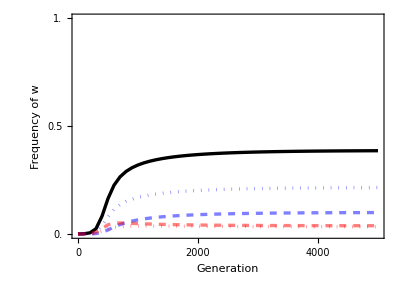

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

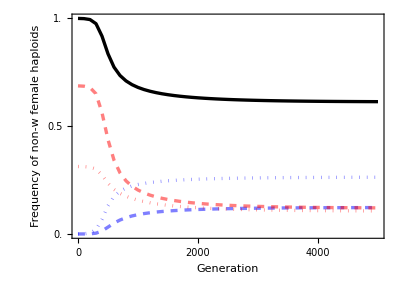

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

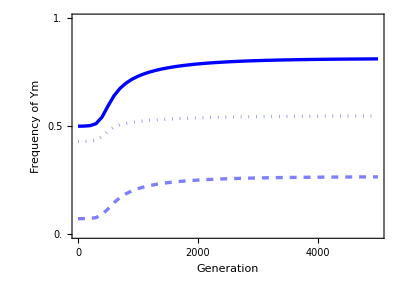

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

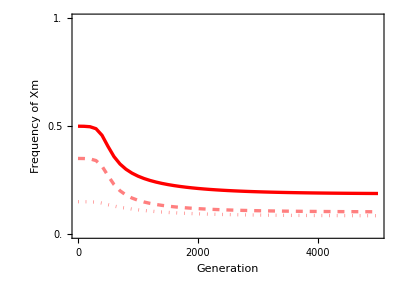

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio at birth

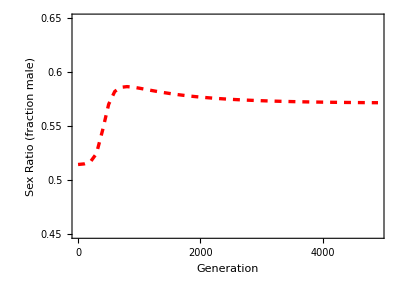

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

#### Mean diploid fitness

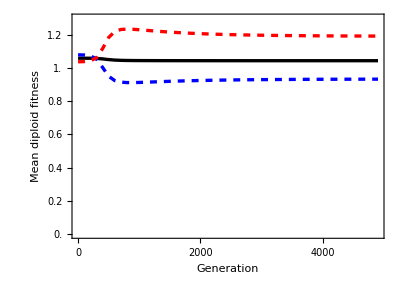

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

#### Mean haploid fitness

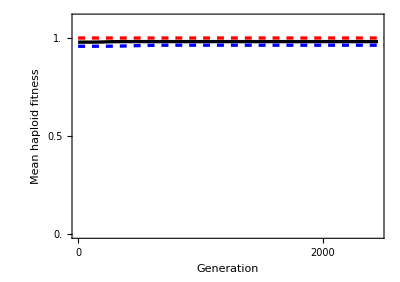

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Example: W invades XY, and fixes [small R]

#### Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
```

```mathematica
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0.01;
tryMdA=0.5;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.01;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

Should it invade? If the following is positive, yes

```mathematica
-(VA Subscript[sDip, female] (-2 r Subscript[sDip, female]+R Subscript[sDip, female]+2 r R Subscript[sDip, female]-R Subscript[sDip, male]+2 r R Subscript[sDip, male]) Subscript[sHap, male]^2)/(2 r R (Subscript[sDip, female]+Subscript[sDip, male])^2)/.r->tryr/.R->tryR/.Subscript[sDip, female]->trysAf/.Subscript[sDip, male]->trysAm/.Subscript[sHap, male]->tryt
```

0.1225 VA

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]
```

0.687097

0.312903

0.350371

0.149629

0.0710304

0.42897

#### Interior stability

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=0.05;
devXm=0.05;
devYm=-0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

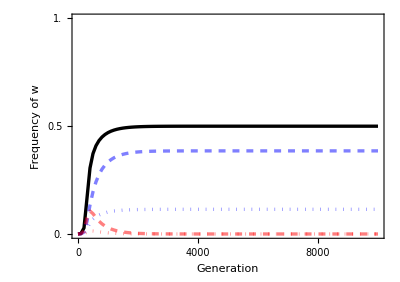

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

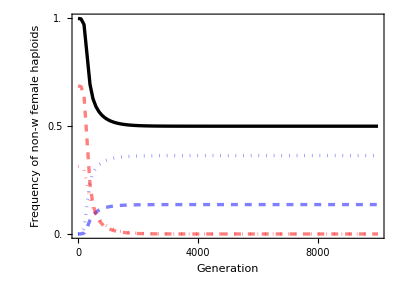

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

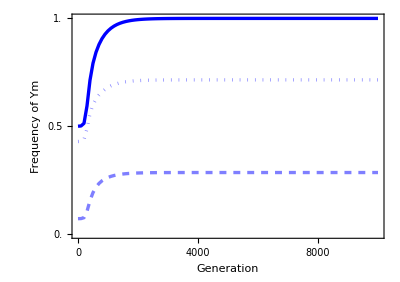

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

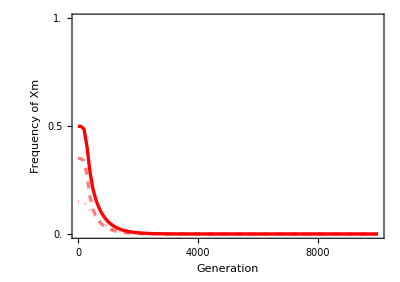

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio at birth

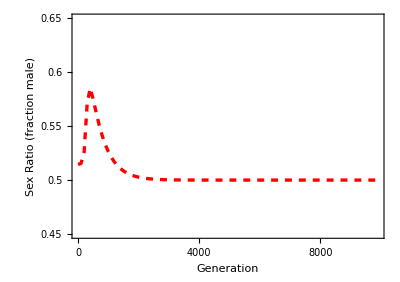

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

#### Mean diploid fitness

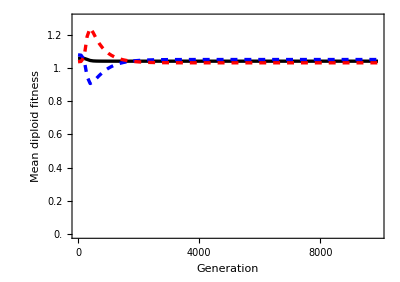

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

#### Mean haploid fitness

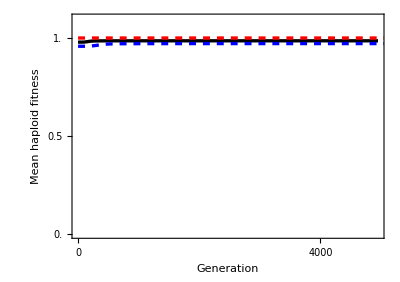

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

### Kozi example: W invades XY and fixes when Y fully linked with allele driving in males

#### Parameters

```mathematica
tryFAA=1;
tryFAa=1;
tryFaa=1;
tryMAA=1;
tryMAa=1;
tryMaa=1;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0;
tryMdA=0.4;
tryFdA=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0;
```

and tryk (0=neo-Y, 1=neo-W)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
(*tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]*)
```

```mathematica
equil[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.,1.,0.,0.5,0.,0.5},{0.,1.,0.,0.6,0.4,0.},{1.,0.,0.4,0.,0.,0.6},{1.,0.,0.5,0.,0.5,0.}}

```mathematica
initialpXAf=1;
initialpXaf=0;
initialpXAm=0.4;
initialpXam=0;
initialYAf=0;
initialYaf=0;
initialpYAm=0;
initialpYam=0.6;
```

#### Interior stability (this is unstable)

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=-0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in females"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of X haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Y haplotypes in males"]
```

-Graphics-

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of Y in haploids from males"]
```

-Graphics-

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=200;
tinterval=2;
tplotinterval=50;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio at birth

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

-Graphics-

#### Mean diploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

#### Mean haploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

### Kozi counter-example: Y invades ZW and fixes when W fully linked with allele driving in males

Here X is Z, Y is W, males are females, and females are males.

#### Parameters

```mathematica
tryFAA=1;
tryFAa=1;
tryFaa=1;
tryMAA=1;
tryMAa=1;
tryMaa=1;
tryMA=1;
tryMa=1;
tryFA=1;
tryFa=1;
tryr=0;
tryMdA=0.5;
tryFdA=0.4;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0;
```

and tryk (1=neo-Y, 0=neo-W)

```mathematica
tryk=1;
```

#### Find equilibrium

Frequency of each haplotype in each sex (sums to one in males and sums to one in females)

```mathematica
(*tempeq=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryMdA,tryFdA]];
initialpXAf=tempeq[[1]]
initialpXaf=tempeq[[2]]
initialpXAm=tempeq[[3]]
initialpXam=tempeq[[4]]
initialYAf=0;
initialYaf=0;
initialpYAm=tempeq[[5]]
initialpYam=tempeq[[6]]*)
```

A fixed on Z and a fixed on W

```mathematica
initialpXAf=1;
initialpXaf=0;
initialpXAm=0.5;
initialpXam=0;
initialYAf=0;
initialYaf=0;
initialpYAm=0;
initialpYam=0.5;
```

#### Interior stability (this is unstable)

We check stability by perturbing the system slightly and checking that allele frequencies return. Parameter dev gives the initial deviations of the frequency of A on each background in each sex:

```mathematica
devXf=-0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=100;
```

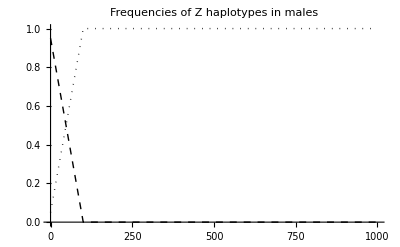

```mathematica
Show[
ListPlot[
Table[
{t,nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Z haplotypes in males"]
```

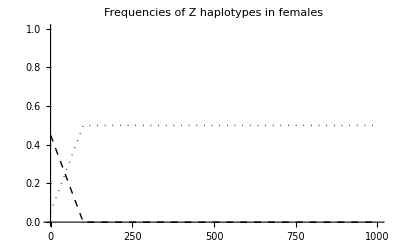

```mathematica
Show[
ListPlot[
Table[
{t,nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of Z haplotypes in females"]
```

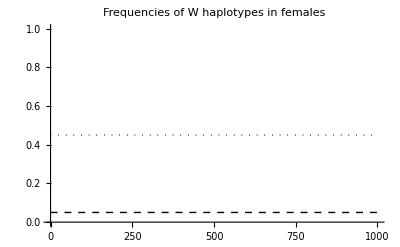

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
{t,nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies of W haplotypes in females"]
```

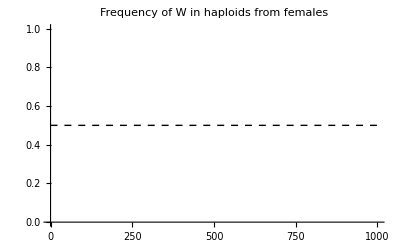

```mathematica
Show[
ListPlot[
Table[
{t,nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]+nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,initialpXAf+devXf,initialpXaf-devXf,trypMXAf,trypMXaf,initialpXAm+devXm,initialpXam-devXm,trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,initialpYAm+devYm,initialpYam-devYm,trypMYAm,trypMYam]},
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
PlotLabel->"Frequency of W in haploids from females"]
```

#### External stability

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequency on all backgrounds

```mathematica
pM=0.0001;

trypMXAf=pM initialpXAf;
trypMXaf=pM initialpXaf;
trypMXAm=pM initialpXAm;
trypMXam=pM initialpXam;
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM initialpYAm;
trypMYam=pM initialpYam;
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=200;
tinterval=2;
tplotinterval=50;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

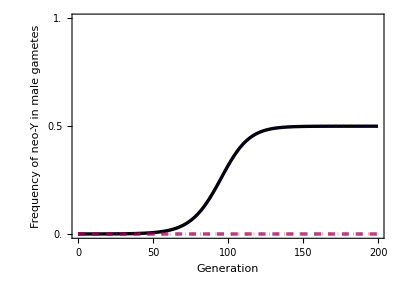

```mathematica
ListPlot[{Table[{t,
Total[{
nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of neo-Y in male gametes"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-y male haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of W in female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Z in female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio at birth

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.65;
yplotintervalSexRatio=0.025;

ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (fraction female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

-Graphics-

#### Mean diploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.3;
yplotintervalSexRatio=0.2;

Show[
ListPlot[{Table[{t,
Total[{
meanDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean diploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleDiploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]/(1-sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam])
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-

#### Mean haploid fitness

```mathematica
yplotminSexRatio=0;
yplotmaxSexRatio=1.1;
yplotintervalSexRatio=0.5;

Show[
ListPlot[{Table[{t,
Total[{
meanHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]/2},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Mean haploid fitness"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}],
ListPlot[{Table[{t,
Total[{
meanMaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},Joined->True],
ListPlot[{Table[{t,
Total[{
meanFemaleHaploidFitness[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryr,tryR,tryMdA,tryFdA,tryk,(1-pM)initialpXAf,(1-pM)initialpXaf,trypMXAf,trypMXaf,(1-pM)initialpXAm,(1-pM)initialpXam,trypMXAm,trypMXam,(1-pM)initialYAf,(1-pM)initialYaf,trypMYAf,trypMYaf,(1-pM)initialpYAm,(1-pM)initialpYam,trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]},PlotStyle->{Directive[Blue,Thickness[lwd],Dashed]},Joined->True]
]
```

-Graphics-